```mathematica
(*Function to compute the Liouville operator for XX-YY coupling*)liouv2qXXYY[x0_]:=Module[{v},v=ConstantArray[0,4^2];
v[[FromDigits[Mod[x0+{1,1,0,0},2],2]+1]]-=I;
v[[FromDigits[Mod[x0+{0,0,1,1},2],2]+1]]+=I;
v[[FromDigits[Mod[x0+{1,1,0,0},2],2]+1]]+=(-1)^(Mod[x0[[1]]+x0[[2]]+1,2]);
v[[FromDigits[Mod[x0+{0,0,1,1},2],2]+1]]+=(-1)^(Mod[x0[[3]]+x0[[4]]+1,2]);
v]
```

```mathematica
(*Function to compute the dissipation operator*)
Diss2qTLC[x0_]:=Module[{v},v=ConstantArray[0,4^2];
v[[FromDigits[x0,2]+1]]-=2;
(*for X rho X*)v[[FromDigits[Mod[x0+{0,1,0,1},2],2]+1]]+=1;
(*for Y rho Y*)v[[FromDigits[Mod[x0+{0,1,0,1},2],2]+1]]+=(-1)^(x0[[2]]+x0[[4]]);
(*for Z rho Z*)v[[FromDigits[x0,2]+1]]+=((-1)^(x0[[2]]+x0[[4]])-1);
v]
```

```mathematica
(*Function to compute the superoperator*)
Superop6[x0_,alpha_,gamma_]:=alpha*liouv2qXXYY[x0]+gamma*Diss2qTLC[x0]

(*Function to compute the matrix representation of the superoperator*)
MatrSuperOp6[alpha_,gamma_]:=Module[{mat},mat=ConstantArray[0,{4^2,4^2}];
Do[mat[[All,i+1]]=Superop6[IntegerDigits[i,2,4],alpha,gamma],{i,0,4^2-1}];
Transpose[mat]]
```

```mathematica
(*Example usage*)
MatrSuperOp6[α,γ]//MatrixForm

NullSpace[MatrSuperOp6[α,γ]]
```

(-2 γ | 0 | 0 | (-1+ⅈ) α | 0 | 2 γ | 0 | 0 | 0 | 0 | 0 | 0 | (-1-ⅈ) α | 0 | 0 | 0
0 | -4 γ | (1+ⅈ) α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1-ⅈ) α | 0 | 0
0 | (1+ⅈ) α | -2 γ | 0 | 0 | 0 | 0 | 2 γ | 0 | 0 | 0 | 0 | 0 | 0 | (-1-ⅈ) α | 0
(-1+ⅈ) α | 0 | 0 | -4 γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1-ⅈ) α
0 | 0 | 0 | 0 | -4 γ | 0 | 0 | (-1+ⅈ) α | (1-ⅈ) α | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 γ | 0 | 0 | 0 | 0 | -2 γ | (1+ⅈ) α | 0 | 0 | (1-ⅈ) α | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (1+ⅈ) α | -4 γ | 0 | 0 | 0 | (1-ⅈ) α | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 γ | 0 | (-1+ⅈ) α | 0 | 0 | -2 γ | 0 | 0 | 0 | (1-ⅈ) α | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (1-ⅈ) α | 0 | 0 | 0 | -2 γ | 0 | 0 | (-1+ⅈ) α | 0 | 2 γ | 0 | 0
0 | 0 | 0 | 0 | 0 | (1-ⅈ) α | 0 | 0 | 0 | -4 γ | (1+ⅈ) α | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (1-ⅈ) α | 0 | 0 | (1+ⅈ) α | -2 γ | 0 | 0 | 0 | 0 | 2 γ
0 | 0 | 0 | 0 | 0 | 0 | 0 | (1-ⅈ) α | (-1+ⅈ) α | 0 | 0 | -4 γ | 0 | 0 | 0 | 0
(-1-ⅈ) α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 γ | 0 | 0 | (-1+ⅈ) α
0 | (-1-ⅈ) α | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ | 0 | 0 | 0 | 0 | -2 γ | (1+ⅈ) α | 0
0 | 0 | (-1-ⅈ) α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (1+ⅈ) α | -4 γ | 0
0 | 0 | 0 | (-1-ⅈ) α | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ | 0 | (-1+ⅈ) α | 0 | 0 | -2 γ)

{{0,0,1,0,0,0,0,1,1,0,0,0,0,1,0,0}}

```mathematica
Eigenvalues[MatrSuperOp6[α,γ]]
```

{0,2 (α-2 γ),-2 ⅈ (α-2 ⅈ γ),2 ⅈ (α+2 ⅈ γ),-4 γ,-4 γ,-4 γ,-2 (α+2 γ),(1+ⅈ) ((-1+ⅈ) γ-√2 √(-ⅈ α^2-ⅈ γ^2)),(1+ⅈ) ((-1+ⅈ) γ+√2 √(-ⅈ α^2-ⅈ γ^2)),(1+ⅈ) ((-1+ⅈ) γ-√2 √(ⅈ α^2-ⅈ γ^2)),(1+ⅈ) ((-1+ⅈ) γ+√2 √(ⅈ α^2-ⅈ γ^2)),(1+ⅈ) Root[-16 α^4-(16+16 ⅈ) γ^3 #1-24 ⅈ γ^2 #1^2+(6-6 ⅈ) γ #1^3+#1^4&,1],(1+ⅈ) Root[-16 α^4-(16+16 ⅈ) γ^3 #1-24 ⅈ γ^2 #1^2+(6-6 ⅈ) γ #1^3+#1^4&,2],(1+ⅈ) Root[-16 α^4-(16+16 ⅈ) γ^3 #1-24 ⅈ γ^2 #1^2+(6-6 ⅈ) γ #1^3+#1^4&,3],(1+ⅈ) Root[-16 α^4-(16+16 ⅈ) γ^3 #1-24 ⅈ γ^2 #1^2+(6-6 ⅈ) γ #1^3+#1^4&,4]}

```mathematica
FromDigits[Mod[{0,1,0,1},2],2]
```

5

## TCL reinvented

First let' s going to create the code for commutator and anticommutator. 
[A,B]=AB-BA      {A,B}=AB+BA
As an example [X,X]=0 and [X,Y]=2iZ

```mathematica
Commut[A_,B_]:=A.B-B.A
Anticommut[A_,B_]:=A.B+B.A
Commut[PauliMatrix[1],PauliMatrix[1]]
Commut[PauliMatrix[1],PauliMatrix[2]]
```

{{0,0},{0,0}}

{{2 ⅈ,0},{0,-2 ⅈ}}

In general for a 2x2 matrix

```mathematica
Commut[{{a,b},{c,d}},{{α,β},{γ,δ}}]
Anticommut[{{a,b},{c,d}},{{α,β},{γ,δ}}]
```

{{-c β+b γ,-b α+a β-d β+b δ},{c α-a γ+d γ-c δ,c β-b γ}}

{{2 a α+c β+b γ,b α+a β+d β+b δ},{c α+a γ+d γ+c δ,c β+b γ+2 d δ}}

Here we construct S(t)=ⅇ^(ⅈ t Ω)σ+  + ⅇ^(-ⅈ t Ω) σ-

```mathematica
St[plus_,minus_]:={{0,minus},{plus, 0}}
St[Exp[I c t],Exp[-I d t]]//MatrixForm
Clear[SΩt,rho,ρ11,ρ01,ρ10,t0]
SΩt[t_]:=St[Exp[I Ω t],Exp[-I Ω t]]
rho={{1-ρ11,ρ01},{ρ10,ρ11}};
SΩt[t0]//MatrixForm
```

(0 | ⅇ^(-ⅈ d t)
ⅇ^(ⅈ c t) | 0)

(0 | ⅇ^(-ⅈ t0 Ω)
ⅇ^(ⅈ t0 Ω) | 0)

### For TCL2

For K2 we have ν [0,[1,ρ]] + iη[0,{1,ρ}]

```mathematica
Clear[t0,t1,ν,η]
```

```mathematica
FullSimplify[ν Commut[SΩt[t0],Commut[SΩt[t1],rho]]+I η Commut[SΩt[t0],Anticommut[SΩt[t1],rho]]]//MatrixForm
```

(2 ν (1-2 ρ11) Cos[(t0-t1) Ω]+2 η Sin[(t0-t1) Ω] | 2 ⅇ^(-ⅈ (t0+t1) Ω) ν (ⅇ^(2 ⅈ t1 Ω) ρ01-ρ10)
-2 ⅇ^(ⅈ (t0-t1) Ω) ν (ⅇ^(2 ⅈ t1 Ω) ρ01-ρ10) | 2 ν (-1+2 ρ11) Cos[(t0-t1) Ω]-2 η Sin[(t0-t1) Ω])

```mathematica
rho
```

{{1-ρ11,ρ01},{ρ10,ρ11}}

Now lets apply it to the bath spectral density of Drude Lorentz to compare it with the python notebook

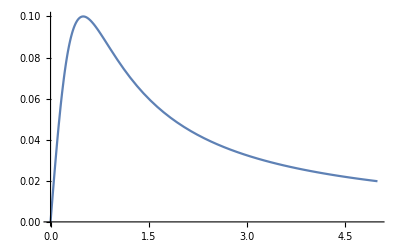

```mathematica
JDLnew[ω_, λ_,γ_]:=((2ω γ λ)/(ω^2+γ^2))
γp=0.5; (*γ is like a cutoof frequency*)
λp=0.1; (* λ is the coupling constant*)
Tp=1;(*temperature*)
Plot[JDLnew[ω, λp,γp],{ω,0,5}]
```

The Markov decay rate is simply 2πJ(Ω)Coth[βΩ/2]. Check there is a factor of 1/π in the J(ω) spectral density

```mathematica
γMarkovDL[α_,β_,λ_,γ_]:=2π( JDLnew[α, λ,γ]/π)Coth[β α/2]
```

According to the TCL2 expression D[ρ11,t]=γ+(t)-γ(t)ρ11 where 
ν[τ]=∫_0^Infty ⅆω J[ω]Coth[βω/2]Cos[ω τ]
η[τ]=-∫_0^Infty ⅆω J[ω]Sin[ω τ]
γ(t)=4∫_0^t ⅆτ ν[τ]Cos[Ωτ]= 2∫_0^Infty ⅆω J[ω]Coth[βω/2](Sin[(ω+Ω)t]/(ω+Ω)+Sin[(-ω+Ω)t]/(-ω+Ω))
=2∫_-Infty^Infty ⅆω J[ω]Coth[βω/2](Sin[(ω+Ω)t]/(ω+Ω))

```mathematica
Integrate[Cos[a t]Cos[b t],{t,0,t}]
Integrate[Sin[a t]Sin[b t],{t,0,t}]
```

(a Cos[b t] Sin[a t]-b Cos[a t] Sin[b t])/(a^2-b^2)

(b Cos[b t] Sin[a t]-a Cos[a t] Sin[b t])/(a^2-b^2)

```mathematica
γBRDL[t_,β_,λ_,γ_]:=2 NIntegrate[JDLnew[u, λ,γ]/π Coth[β u/2](Sin[(u+1)t]/(u+1)+Sin[(1-u)t]/(1-u)),{u,0,Infinity}]
γBRDLComplete[t_,β_,λ_,γ_]:=2 NIntegrate[JDLnew[u, λ,γ]/π Coth[β u/2](Sin[(u+1)t]/(u+1)),{u,-Infinity,Infinity}]
γBRDLInComplete[t_,β_,λ_,γ_]:=4 NIntegrate[JDLnew[u, λ,γ]/π Coth[β u/2](Sin[(u+1)t]/(u+1)),{u,0,Infinity}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 0.000341373 and 8.61907×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {-4.81037×10^7}. NIntegrate obtained 0.000341373 and 8.61907×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 0.000170682 and 4.30787×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

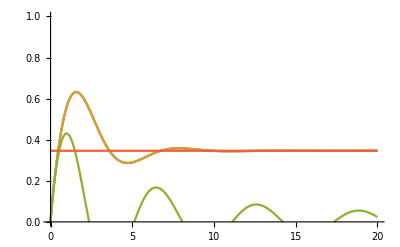

```mathematica
Plot[{γBRDL[t,1/Tp,λp,γp],γBRDLComplete[t,1/Tp,λp,γp],γBRDLInComplete[t,1/Tp,λp,γp],γMarkovDL[1,1/Tp,λp,γp]},{t,0,20},PlotRange->{0,1}]
```

```mathematica
AbsoluteTiming[γBRDL[0.2,1/Tp,λp,γp]]
AbsoluteTiming[γBRDLComplete[0.2,1/Tp,λp,γp]]
AbsoluteTiming[2γBRDLInComplete[0.2,1/Tp,λp,γp]]
```

{0.03531,0.175212}

{0.030548,0.175212}

{0.011707,0.170796}

Now lets find γPlus 
ν[τ]=∫_0^Infty ⅆω J[ω]Coth[βω/2]Cos[ω τ]
η[τ]= -∫_0^Infty ⅆω J[ω]Sin[ω τ]
γ+(t)=4∫_0^t ⅆτ (ν[τ]Cos[Ωτ]+η[τ]Sin[Ωτ])= 2∫_0^Infty ⅆω J[ω](2/(Exp[βω]-1)Sin[(-ω+Ω)t]/(-ω+Ω)+2/(1-Exp[-βω])Sin[(ω+Ω)t]/(ω+Ω))=2∫_0^Infty ⅆω J[ω](2/(1-Exp[-βω])Sin[(ω+Ω)t]/(ω+Ω))

0.0857405

0.0857405

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 0.000170682 and 4.30787×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 0.000170682 and 4.87139×10^-8 for the integral and error estimates.

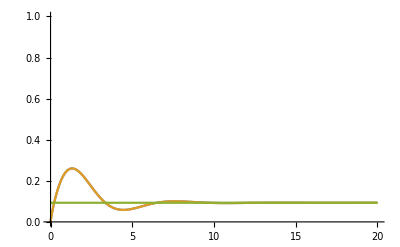

```mathematica
γPlusMarkovDL[α_,β_,λ_,γ_]:=2π( JDLnew[α, λ,γ]/π)Exp[-β α]/(1-Exp[-β α])
γPlusBRDL[t_,β_,λ_,γ_]:=2 NIntegrate[JDLnew[u, λ,γ]/π 1/(1-Exp[-β u])(Sin[(u+1)t]/(u+1)+Sin[(1-u)t]/(1-u)Exp[-β u]),{u,0,Infinity}]
γPlusBRDLComplete[t_,β_,λ_,γ_]:=2 NIntegrate[JDLnew[u, λ,γ]/π 1/(1-Exp[-β u])Sin[(u+1)t]/(u+1),{u,-Infinity,Infinity}]
γPlusBRDL[0.2,1/Tp,λp,γp]
γPlusBRDLComplete[0.2,1/Tp,λp,γp]
Plot[{γPlusBRDL[t,1/Tp,λp,γp],γPlusBRDLComplete[t,1/Tp,λp,γp],γPlusMarkovDL[1,1/Tp,λp,γp]},{t,0,20},PlotRange->{0,1}]
```

Check the timing to get faster restult

```mathematica
AbsoluteTiming[γPlusBRDL[0.2,1/Tp,λp,γp]]
AbsoluteTiming[γPlusBRDLComplete[0.2,1/Tp,λp,γp]]
```

{0.030415,0.0857405}

{0.022904,0.0857405}

Now we are solving the complete solution for ρ11 :  ρ11 Exp[-]

```mathematica
Clear[int1,int2,int2BRDL]
int1[tp_?NumericQ,β_,λ_,γ_]:=int1[tp,β,λ,γ]=NIntegrate[γBRDLComplete[tpp,β,λ,γ],{tpp,0,tp}]

int2[t_?NumericQ,β_,λ_,γ_]:=int2[t,β,λ,γ]=NIntegrate[γPlusBRDLComplete[tp,β,λ,γ]Exp[int1[tp,β,λ,γ]],{tp,0.05,t}]
(*NIntegrate[γPlusBRDL[tp,β,λ,γ]Exp[int1BRDL[tp,β,λ,γ]]*)
ρ11TCL2DL[t_,ρ0_,β_,λ_,γ_]:=Exp[-int1[t,β,λ,γ]](ρ0+int2[t,β,λ,γ])
```

```mathematica
ρ11TCL2DL[1,0,βp,λp,γp]
```

0.132447

NIntegrate::inumr: The integrand (0.031831 u Sin[tp (1+u)])/((1-ⅇ^-u) (1+u) (0.25+u^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0.04,1.00024},{0.54,0.947833},{1.04,0.860651},{1.54,0.78654},{2.04,0.740766},{2.54,0.720012},{3.04,0.716148},{3.54,0.721777},{4.04,0.731226},{4.54,0.740435}}

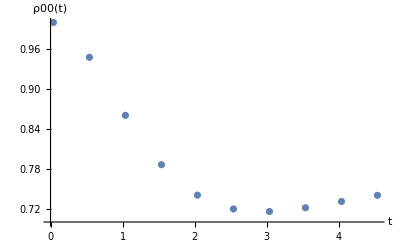

```mathematica
ρ0p=0;
βp=1/Tp;
γp=0.5;
λp=0.1;

TABLEρ00BRDL=Table[{t,1-ρ11TCL2DL[t,ρ0p,βp,λp,γp]},{t,0.04,5,0.5}]
ListPlot[TABLEρ00BRDL,AxesLabel->{"t","ρ00(t)"}]
```

```mathematica
TABLEρ00BRDL
```

{{0.04,1.00024},{0.54,0.947833},{1.04,0.860651},{1.54,0.78654},{2.04,0.740766},{2.54,0.720012},{3.04,0.716148},{3.54,0.721777},{4.04,0.731226},{4.54,0.740435}}

### For TCL4

For K4 we have 

ν02 ν13 [0, [[1,2],[3, ρ]]]+I ν02 η13  [0, [[1, 2], {3, ρ}]]
 [0, [[1,2],[3, ρ]]]

```mathematica
FullSimplify[Commut[SΩt[t],Commut[Commut[SΩt[t1],SΩt[t2]],Commut[SΩt[t3],rho]]]]//MatrixForm
```

(8 (1-2 ρ11) Sin[(t1-t2) Ω] Sin[(t-t3) Ω] | 0
0 | 8 (-1+2 ρ11) Sin[(t1-t2) Ω] Sin[(t-t3) Ω])

[0, [[1, 2], {3, ρ}]]

```mathematica
FullSimplify[Commut[SΩt[t],Commut[Commut[SΩt[t1],SΩt[t2]],Anticommut[SΩt[t3],rho]]]]//MatrixForm
```

(8 ⅈ Cos[(t-t3) Ω] Sin[(t1-t2) Ω] | 0
0 | -8 ⅈ Cos[(t-t3) Ω] Sin[(t1-t2) Ω])

I η02 ν13 [0, {[1, 2], [3, ρ]}] - η02 η13 [0, {[1, 2], {3, ρ}}]
 [0, {[1, 2], [3, ρ]}]

```mathematica
FullSimplify[Commut[SΩt[t],Anticommut[Commut[SΩt[t1],SΩt[t2]],Commut[SΩt[t3],rho]]]]
```

{{0,0},{0,0}}

[0, {[1, 2], {3, ρ}}]

```mathematica
FullSimplify[Commut[SΩt[t],Anticommut[Commut[SΩt[t1],SΩt[t2]],Anticommut[SΩt[t3],rho]]]]//MatrixForm
```

(0 | 4 ⅇ^(-ⅈ (t+t1+t2+t3) Ω) (ⅇ^(2 ⅈ t1 Ω)-ⅇ^(2 ⅈ t2 Ω)) (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10)
4 ⅇ^(ⅈ (t-t1-t2-t3) Ω) (-ⅇ^(2 ⅈ t1 Ω)+ⅇ^(2 ⅈ t2 Ω)) (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10) | 0)

ν03 ν12  [0, [[1,3],[2,ρ]]] + I ν03 η12 [0, [[1, 3], {2, ρ} ]]
 [0, [[1,3],[2,ρ]]]

```mathematica
FullSimplify[Commut[SΩt[t],Commut[Commut[SΩt[t1],SΩt[t3]],Commut[SΩt[t2],rho]]]]//MatrixForm
```

(8 (1-2 ρ11) Sin[(t-t2) Ω] Sin[(t1-t3) Ω] | 0
0 | 8 (-1+2 ρ11) Sin[(t-t2) Ω] Sin[(t1-t3) Ω])

[0, [[1, 3], {2, ρ} ]]

```mathematica
FullSimplify[Commut[SΩt[t],Commut[Commut[SΩt[t1],SΩt[t3]],Anticommut[SΩt[t2],rho]]]]//MatrixForm
```

(8 ⅈ Cos[(t-t2) Ω] Sin[(t1-t3) Ω] | 0
0 | -8 ⅈ Cos[(t-t2) Ω] Sin[(t1-t3) Ω])

Iη03 ν12 [0, {[1, 3], [2, ρ]}]- η03 η12 [0, {[1, 3], {2, ρ}}]
 [0, {[1, 3], [2, ρ]}]

```mathematica
FullSimplify[Commut[SΩt[t],Anticommut[Commut[SΩt[t1],SΩt[t3]],Commut[SΩt[t2],rho]]]]
```

{{0,0},{0,0}}

[0, {[1, 3], {2, ρ}}]

```mathematica
FullSimplify[Commut[SΩt[t],Anticommut[Commut[SΩt[t1],SΩt[t3]],Anticommut[SΩt[t2],rho]]]]//MatrixForm
```

(0 | 4 ⅇ^(-ⅈ (t+t1+t2+t3) Ω) (ⅇ^(2 ⅈ t1 Ω)-ⅇ^(2 ⅈ t3 Ω)) (ⅇ^(2 ⅈ t2 Ω) ρ01+ρ10)
4 ⅇ^(ⅈ (t-t1-t2-t3) Ω) (-ⅇ^(2 ⅈ t1 Ω)+ⅇ^(2 ⅈ t3 Ω)) (ⅇ^(2 ⅈ t2 Ω) ρ01+ρ10) | 0)

[0, [1, [[2,3] ρ]]]

```mathematica
FullSimplify[Commut[SΩt[t],Commut[SΩt[t1],Commut[Commut[SΩt[t2],SΩt[t3]],rho]]]]//MatrixForm
```

(0 | 4 ⅇ^(-ⅈ (t+t1+t2+t3) Ω) (-ⅇ^(2 ⅈ t2 Ω)+ⅇ^(2 ⅈ t3 Ω)) (ⅇ^(2 ⅈ t1 Ω) ρ01+ρ10)
4 ⅇ^(ⅈ (t-t1-t2-t3) Ω) (ⅇ^(2 ⅈ t2 Ω)-ⅇ^(2 ⅈ t3 Ω)) (ⅇ^(2 ⅈ t1 Ω) ρ01+ρ10) | 0)

[0, [1, {[2, 3] ,ρ}]]

```mathematica
FullSimplify[Commut[SΩt[t],Commut[SΩt[t1],Anticommut[Commut[SΩt[t2],SΩt[t3]],rho]]]]//MatrixForm
```

(-8 ⅈ Cos[(t-t1) Ω] Sin[(t2-t3) Ω] | 0
0 | 8 ⅈ Cos[(t-t1) Ω] Sin[(t2-t3) Ω])

#### Let’s going to analize

γ4 = 16(ν02 ν13 s12 s03 + ν03 ν12 s13 s02)

```mathematica
Integrate[Cos[ω(t1-t3)]Sin[ω(t-t3)],{t3,0,t}]
```

(Cos[(-t+t1) ω]-Cos[(t+t1) ω]+2 t ω Sin[(t-t1) ω])/(4 ω)

```mathematica
FullSimplify[Integrate[Cos[ω(t1-t3)]Sin[Ω(t-t3)],{t3,0,t2}]]
```

(Cos[t1 ω-t Ω]-Cos[t1 ω-t2 ω-t Ω+t2 Ω])/(2 ω-2 Ω)+(Sin[1/2 t2 (ω+Ω)] Sin[t1 ω+t Ω-1/2 t2 (ω+Ω)])/(ω+Ω)

```mathematica
FullSimplify[Integrate[Sin[ω(t1-t3)]Cos[(t-t3)],{t3,0,t2}]]
```

-(Sin[1/2 t2 (-1+ω)] Sin[t+1/2 t2 (-1+ω)-t1 ω])/(-1+ω)+(Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)

```mathematica
FullSimplify[Integrate[Integrate[Cos[ωp(t-t2)]Sin[Ω(t1-t2)]Integrate[Cos[ω(t1-t3)]Sin[Ω(t-t3)],{t3,0,t2}],{t2,0,t1}],{t1,0,t}]]
```

$Aborted

```mathematica
FullSimplify[Integrate[Cos[ω(t1-t3)]Sin[Ω(t-t3)],{t3,0,t2}]]
```

(Cos[t1 ω-t Ω]-Cos[t1 ω-t2 ω-t Ω+t2 Ω])/(2 ω-2 Ω)+(Sin[1/2 t2 (ω+Ω)] Sin[t1 ω+t Ω-1/2 t2 (ω+Ω)])/(ω+Ω)

```mathematica
FullSimplify[Integrate[Cos[ω(t1-t3)]Sin[(t-t3)],{t3,0,t2}]]
```

(Sin[1/2 t2 (-1+ω)] Sin[t+1/2 t2 (-1+ω)-t1 ω])/(-1+ω)+(Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)

```mathematica
FullSimplify[Integrate[Cos[ω(t-t3)]Sin[(t1-t3)],{t3,0,t2}]]
```

(Sin[1/2 t2 (-1+ω)] Sin[t1+1/2 t2 (-1+ω)-t ω])/(-1+ω)+(Sin[1/2 t2 (1+ω)] Sin[t1+t ω-1/2 t2 (1+ω)])/(1+ω)

Checking that integrating over positive frequencies is equivalent to integrate over all possible frequencies.

```mathematica
JDLnew[ω_, λ_,γ_]:=((2ω γ λ)/(ω^2+γ^2))
gamma4approx[t_,t1_,t2_,β_, λ_,γ_]:=NIntegrate[JDLnew[ω, λ,γ]/π Coth[β ω/2]((Sin[1/2 t2 (-1+ω)] Sin[t+1/2 t2 (-1+ω)-t1 ω])/(-1+ω)+(Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)),{ω,0,Infinity}]
gamma4approxmitad[t_,t1_,t2_,β_, λ_,γ_]:= NIntegrate[JDLnew[ω, λ,γ]/π Coth[β ω/2]((Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)),{ω,-Infinity,Infinity}]
gamma4approx[1,2,1,1/Tp, λp,γp]
gamma4approxmitad[1,2,1,1/Tp, λp,γp]
```

0.0396322

0.0396322

g1=@(t,t1,t2, beta, lambda, gamma,Msup) integral(@(u) (JDLnew(u, lambda, gamma) ./ pi) .* coth(beta * u/ 2) .* integrand1(u, t,t1,t2) ,-Msup,Msup,’ArrayValued’,true, ‘RelTol’, 1e-1, ‘AbsTol’, 1e-1)

nu02 = @(t, t2, beta, lambda, gamma, Msup) integral (@(omega) (JDLnew (omega, lambda, gamma) ./pi) .*coth (beta*omega/2) .*cos (omega .*(t - t2)), 0, Msup, ' ArrayValued', true, ' RelTol', 1 e - 1, ' AbsTol', 1 e - 1)
%alpha1 = @(t,beta, lambda, gamma,Msup) integral(@(t1) integral(@(t2) nu02(t,t2, beta, lambda, gamma,Msup).*sin(t1-t2).*g1(t,t1,t2, beta, lambda, gamma,Msup) ,0,t1,’ArrayValued’,true,’RelTol’, 1e-1, ‘AbsTol’, 1e-1),0,t,’ArrayValued’,true, ‘AbsTol’, 1e-1)

```mathematica
Msup=3
g1f[t_,t1_,t2_,β_, λ_,γ_]:= NIntegrate[JDLnew[ω, λ,γ]/π Coth[β ω/2]((Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)),{ω,-Msup,Msup}]
ντ[t_,β_, λ_,γ_]:=NIntegrate[JDLnew[ω, λ,γ]/π Coth[β ω/2]Cos[ω t],{ω,0,Msup}]

alpha1integral1[t_?NumericQ,t1_?NumericQ,β_?NumericQ, λ_?NumericQ,γ_?NumericQ]:=NIntegrate[g1f[t,t1,t2,β, λ,γ]*ντ[t-t2,β, λ,γ]*Sin[t1-t2],{t2,0,t1}]
alpha1integral2[t_?NumericQ,β_?NumericQ, λ_?NumericQ,γ_?NumericQ]:=NIntegrate[alpha1integral1[t,t1,β, λ,γ],{t1,0,t}]
alpha1integral2[6,1/Tp, λp,γp]
```

3

-0.00876564

Si da lo mismo que Matlab, vamos a confiar que estamos bien en gamma

```mathematica
Tp
λp
γp
```

1

0.1

0.5

```mathematica
Clear[funcTodd]
funcTodd2[t_,ω_,ωp_,Ω_]:=Integrate[Integrate[Cos[ω(t-t2)]Sin[Ω(t1-t2)]*Integrate[Cos[ωp(t1-t3)]Sin[Ω(t-t3)],{t3,0,t2}],{t2,0,t1}],{t1,0,t}]
funcTodd2[t,ω,ωp,Ω]
```

-((ω (2 Ω Cos[t Ω]-(Ω+ωp) Cos[t (2 Ω-ωp)]+(-Ω+ωp) Cos[t ωp]) Sin[t ω])/(4 (ω^2-Ω^2) (Ω-ωp)^2 (Ω+ωp)))-(Ω Sin[t (ω-Ω)])/(4 (ω-Ω) (Ω-ωp) (ω+ωp) (ω-2 Ω+ωp))+Sin[t (ω-Ω)]/(8 (ω-Ω) (ω-ωp) (Ω+ωp))-Sin[t (ω-Ω)]/(8 (ω-Ω) (ω-2 Ω-ωp) (Ω+ωp))-(Ω Sin[t (ω+Ω)])/(4 (ω+Ω) (ω-ωp) (Ω-ωp) (ω+2 Ω-ωp))-Sin[t (ω+Ω)]/(8 (ω+Ω) (ω+ωp) (Ω+ωp))+Sin[t (ω+Ω)]/(8 (ω+Ω) (Ω+ωp) (ω+2 Ω+ωp))+(-Sin[t (ω-Ω)]+Sin[t (ω-ωp)])/(8 (ω+Ω) (Ω-ωp) (Ω+ωp))+(-Sin[t (ω-Ω)]+Sin[t (ω-ωp)])/(8 (ω-ωp) (-Ω+ωp) (Ω+ωp))+(-Sin[t (ω+Ω)]+Sin[t (ω-ωp)])/(8 (ω-ωp) (-Ω+ωp) (Ω+ωp))+(Sin[t (ω-Ω)]-Sin[t (ω-2 Ω-ωp)])/(8 (ω-2 Ω-ωp) (Ω+ωp)^2)+(-Sin[t (ω-Ω)]+Sin[t (ω-2 Ω-ωp)])/(8 (ω-Ω) (Ω+ωp)^2)+(Ω (ω Cos[t Ω] Sin[t ω]-ωp Cos[t ω] Sin[t Ω]+ωp Sin[t (Ω-ωp)]))/(2 (ω^2-Ω^2) (ω-ωp) (Ω-ωp) (ω+ωp))+(Sin[t (ω+Ω)]-Sin[t (ω+2 Ω-ωp)])/(8 (Ω-ωp)^2 (ω+2 Ω-ωp))+(Ω Cos[t ω] (-2 ωp Sin[t Ω]+(Ω+ωp) Sin[t (2 Ω-ωp)]+(Ω-ωp) Sin[t ωp]))/(4 (-ω^2+Ω^2) (Ω-ωp)^2 (Ω+ωp))+(Sin[t (ω+Ω)]-Sin[t (ω+ωp)])/(8 (Ω-ωp) (ω+ωp) (Ω+ωp))+(-Sin[t (ω-Ω)]+Sin[t (ω+ωp)])/(8 (ω+ωp) (-Ω^2+ωp^2))+(-Sin[t (ω+Ω)]+Sin[t (ω+ωp)])/(8 (ω-Ω) (Ω-ωp) (Ω+ωp))+(Sin[t (ω-Ω)]-Sin[t (ω-2 Ω+ωp)])/(8 (Ω-ωp)^2 (ω-2 Ω+ωp))+(Sin[t (ω+Ω)]-Sin[t (Ω+ωp)])/(8 (ω-Ω) (ω-ωp) (Ω+ωp))+(Sin[t (ω-Ω)]+Sin[t (Ω+ωp)])/(8 (ω-Ω) (ω+ωp) (Ω+ωp))-(Sin[t (ω-Ω)]+Sin[t (Ω+ωp)])/(8 (ω+Ω) (ω+ωp) (Ω+ωp))+(-Sin[t (ω+Ω)]+Sin[t (Ω+ωp)])/(8 (ω+Ω) (ω-ωp) (Ω+ωp))+(Sin[t (ω+Ω)]-Sin[t (ω+2 Ω+ωp)])/(8 (Ω+ωp)^2 (ω+2 Ω+ωp))+(-Sin[t (ω+Ω)]+Sin[t (ω+2 Ω+ωp)])/(8 (ω+Ω) (Ω+ωp)^2)

```mathematica
funcTodd2[t_,ω_,ωp_,Ω_]:=Integrate[Integrate[Cos[ω(t-t2)]Sin[Ω(t1-t2)]*Integrate[Cos[ωp(t1-t3)]Sin[Ω(t-t3)],{t3,0,t2}],{t2,0,t1}],{t1,0,t}]
FullSimplify[funcTodd2[t,ω,ωp,1]]
```

1/8 (((ω^2+ωp-ω (5+ωp)) Sin[t (-1+ω)])/((-1+ω) (ω-ωp) (ω+ωp) (-1+ωp^2))+(4 ω Sin[t (1+ω)])/((1+ω) (ω^2-ωp^2) (-1+ωp^2))+Sin[t-t ω]/((ω+ωp) (-1+ωp^2))+Sin[t (-2+ω-ωp)]/((-1+ω) (1+ωp)^2)-Sin[t (ω-ωp)]/((-1+ω) (-1+ωp^2))-Sin[t (ω-ωp)]/((1+ω) (-1+ωp^2))+(2 Sin[t (ω-ωp)])/((ω-ωp) (-1+ωp^2))+Sin[t (2+ω-ωp)]/((1+ω) (-1+ωp)^2)+Sin[t (2+ω-ωp)]/((-1+ωp)^2 (-2-ω+ωp))+Sin[t (-1+ωp)]/((-1+ω) (ω-ωp) (-1+ωp))+Sin[t (1+ωp)]/((1+ω) (ω-ωp) (1+ωp))+Sin[t (1+ωp)]/((-1+ω) (1+ωp) (-ω+ωp))+Sin[t (1+ωp)]/((-1+ω) (1+ωp) (ω+ωp))-Sin[t (1+ωp)]/((1+ω) (1+ωp) (ω+ωp))+Sin[t (2-ω+ωp)]/((-2+ω-ωp) (1+ωp)^2)+Sin[t (-2+ω+ωp)]/((-1+ω) (-1+ωp)^2)-Sin[t (-2+ω+ωp)]/((-1+ωp)^2 (-2+ω+ωp))-Sin[t (ω+ωp)]/((-1+ω) (-1+ωp^2))-Sin[t (ω+ωp)]/((1+ω) (-1+ωp^2))+(2 Sin[t (ω+ωp)])/((ω+ωp) (-1+ωp^2))+Sin[t (2+ω+ωp)]/((1+ω) (1+ωp)^2)-Sin[t (2+ω+ωp)]/((1+ωp)^2 (2+ω+ωp))+Sin[t-t ωp]/((1+ω) (ω-ωp) (-1+ωp))+Sin[t-t ωp]/((-1+ω) (-1+ωp) (ω+ωp))-Sin[t-t ωp]/((1+ω) (-1+ωp) (ω+ωp)))

γ+4   beta1 = 8 ν02 s12 (η13 c03 - ν13 s03)

(η13 c03 - ν13 s03)
=-∫_0^Infty ⅆω J[ω](Sin[ω (t1-t3)]cos[Ω (t-t3)]+Coth(βω/2)Cos[ω (t1-t3)]Sin[Ω (t-t3)]
=∫_-Infty^Infty ⅆω J[ω]2/(1-Exp[-βw])(Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)

```mathematica
FullSimplify[Integrate[Sin[ω(t1-t3)]Cos[(t-t3)],{t3,0,t2}]]
FullSimplify[Integrate[Cos[ω(t1-t3)]Sin[(t-t3)],{t3,0,t2}]]
```

-(Sin[1/2 t2 (-1+ω)] Sin[t+1/2 t2 (-1+ω)-t1 ω])/(-1+ω)+(Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)

(Sin[1/2 t2 (-1+ω)] Sin[t+1/2 t2 (-1+ω)-t1 ω])/(-1+ω)+(Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)

= 8 ν03 s13 (η12 c02 - ν12 s02)
For ν03 s13

```mathematica
FullSimplify[Integrate[Cos[ω(t-t3)]Sin[(t1-t3)],{t3,0,t2}]]
```

(Sin[1/2 t2 (-1+ω)] Sin[t1+1/2 t2 (-1+ω)-t ω])/(-1+ω)+(Sin[1/2 t2 (1+ω)] Sin[t1+t ω-1/2 t2 (1+ω)])/(1+ω)

and for (η12 c02 - ν12 s02)

Why the hell they are different?

```mathematica
Integrate[Cos[ω(t1-t3)]Sin[G(t2-t3)],{t3,0,t2}]
```

(-G Cos[G t2] Cos[t1 ω]+G Cos[(t1-t2) ω]-ω Sin[G t2] Sin[t1 ω])/(G^2-ω^2)

```mathematica
FullSimplify[Integrate[Sin[ω(t1-t3)]Sin[G(t2-t3)],{t3,0,t2}]]
```

(ω Cos[t1 ω] Sin[G t2]-G Cos[G t2] Sin[t1 ω]+G Sin[(t1-t2) ω])/(G^2-ω^2)

Let' s try again 
γ+4   beta1 = 8 ν02 s12 (η13 c03 - ν13 s03)
(η13 c03 - ν13 s03)=Im[B(t1,t3)exp[-iΩ (t-t3)] ]
=-∫_0^Infty ⅆω J[ω](Sin[ω (t1-t3)]cos[Ω (t-t3)]+Coth(βω/2)Cos[ω (t1-t3)]Sin[Ω (t-t3)]
-∫_o^t2 ⅆt3(η13 c03 - ν13 s03)=∫_-Infty^Infty ⅆω J[ω]2/(1-Exp[-βw])(Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)

```mathematica
Integrate[Sin[-ω(t1-t3)-Ω(t-t3)],{t3,0,t2}]
```

-(2 Sin[1/2 t2 (ω+Ω)] Sin[t1 ω+t Ω-1/2 t2 (ω+Ω)])/(ω+Ω)

Hay un error de signo que no alcanzo a ver
Finally we integrate
∫_0^t ⅆt1∫_0^t1 ⅆt2 s12 ν02  ∫_-Infty^Infty ⅆω J[ω]2/(1-Exp[-βw])(Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)

Now for 
beta2 = 8 ν03 s13 (η12 c02 - ν12 s02)
∫_0^t ⅆt1 ∫_0^t1 ⅆt2  (η12 c02 - ν12 s02)∫_0^t2 ⅆt3 ν03 s13
 (η12 c02 - ν12 s02)=Im[B(t1,t2)exp[-iΩ (t-t2)] ]=∫_-Infty^Infty ⅆω J[ω]1/(1-Exp[-βw]) Sin[-t1 ω-t Ω+1/2 t2 ( Ω+ω)] No vamos a usar esta expresion
 and ∫_0^t2 ⅆt3 ν03 s13= ∫_-Infty^Infty ⅆω J[ω]Coth[βω/2] (Sin[1/2 t2 (ω+Ω)] Sin[t1Ω +t ω-1/2 t2 (ω+Ω)])/(ω+Ω)
  check the first line corresponds to∫_0^t2 ⅆt3 ν03 s13 and the second to ∫_0^t2 ⅆt3 ν13 s03

```mathematica
FullSimplify[Integrate[Cos[ω(t-t3)]Sin[(t1-t3)],{t3,0,t2}]]
FullSimplify[Integrate[Cos[ω(t1-t3)]Sin[(t-t3)],{t3,0,t2}]]
```

(Sin[1/2 t2 (-1+ω)] Sin[t1+1/2 t2 (-1+ω)-t ω])/(-1+ω)+(Sin[1/2 t2 (1+ω)] Sin[t1+t ω-1/2 t2 (1+ω)])/(1+ω)

(Sin[1/2 t2 (-1+ω)] Sin[t+1/2 t2 (-1+ω)-t1 ω])/(-1+ω)+(Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)

Finally we integrate
beta2=∫_0^t ⅆt1∫_0^t2 ⅆt2 (η12 c02-ν12 s02)∫_0^t2 ⅆt3 ν03 s13

Now for beta3 
beta3=∫_0^t ⅆt1∫_0^t2 ⅆt2 ∫_0^t2 ⅆt3 (- c01s23ν03 η12)=∫_0^t ⅆt1∫_0^t1 ⅆt2 (- c01 η12) ∫_0^t2 ⅆt3 ν03 s23
For  ∫_0^t2 ⅆt3 ν03 s23= ∫_0^Infty ⅆω J[ω]Coth[βω/2] ∫_0^t2 ⅆt3 Cos[ω(t-t3)]Sin[ω(t2-t3)]=∫_0^Infty ⅆω J[ω]Coth[βω/2](-Ω Cos[(t-t2) ω]+Ω Cos[t ω] Cos[t2 Ω]+ω Sin[t ω] Sin[t2 Ω])/(ω^2-Ω^2)

```mathematica
FullSimplify[Integrate[Cos[ω(t-t3)]Sin[Ω(t2-t3)],{t3,0,t2}]]
FullSimplify[Integrate[Cos[ω(t-t3)]Sin[(t2-t3)],{t3,0,t2}]]
```

(-Ω Cos[(t-t2) ω]+Ω Cos[t ω] Cos[t2 Ω]+ω Sin[t ω] Sin[t2 Ω])/(ω^2-Ω^2)

(Cos[t2] Cos[t ω]-Cos[(t-t2) ω]+ω Sin[t2] Sin[t ω])/(-1+ω^2)

Now for beta4
beta4=∫_0^t ⅆt1∫_0^t2 ⅆt2 ∫_0^t2 ⅆt3 (- c01s23η03 ν12)=∫_0^t ⅆt1∫_0^t1 ⅆt2 (- c01 ν12) ∫_0^t2 ⅆt3 η03  s23
For  ∫_0^t2 ⅆt3  η03  s23= ∫_0^Infty ⅆω J[ω]∫_0^t2 ⅆt3 Sin[ω(t-t3)]Sin[Ω(t2-t3)]=-∫_0^Infty ⅆω J[ω](-Ω Cos[t2 Ω] Sin[t ω]+Ω Sin[(t-t2) ω]+ω Cos[t ω] Sin[t2 Ω])/(-ω^2+Ω^2)

```mathematica
FullSimplify[Integrate[Sin[ω(t-t3)]Sin[Ω(t2-t3)],{t3,0,t2}]]
```

(-Ω Cos[t2 Ω] Sin[t ω]+Ω Sin[(t-t2) ω]+ω Cos[t ω] Sin[t2 Ω])/(-ω^2+Ω^2)

## Sin previa integracion, directo

Contruct the real and imaginary parts of the bath correlation ν and η

```mathematica
JDLnew[ω_, λ_,γ_]:=((2ω γ λ)/(ω^2+γ^2))
νdirect[τ_,β_, λ_,γ_,minf_,Msup_]:=NIntegrate[JDLnew[ω, λ,γ]/π Coth[β ω/2]Cos[ω τ],{ω,minf,Msup}]
ηdirect[τ_, λ_,γ_,minf_,Msup_]:=NIntegrate[-JDLnew[ω, λ,γ]/π Sin[ω τ],{ω,minf,Msup}]
```

#### TCL 2

Define the decay rates for TCL2

```mathematica
Clear[γ2direct]
γ2direct[t_, β_, λ_,γ_,minf_,Msup_]:=4 NIntegrate[νdirect[t-t1,β, λ,γ,minf,Msup]Cos[t-t1],{t1,0,t}]
γ2plusdirect[t_, β_, λ_,γ_,minf_,Msup_]:=2 NIntegrate[(νdirect[t-t1,β, λ,γ,minf,Msup]Cos[t-t1]+ηdirect[t-t1, λ,γ,minf,Msup]Sin[t-t1]),{t1,0,t}]
```

Define the parameters

```mathematica
Tp=1;
βp=1/Tp;
γp=0.5;
λp=0.1;
```

```mathematica
γ2direct[1, βp, λp,γp,0,1]
γ2direct[1, βp, λp,γp,0,2]
γ2direct[1, βp, λp,γp,0,3]
```

NIntegrate::inumr: The integrand (0.031831 ω Cos[(1-t1) ω] Coth[ω/2])/(0.25+ω^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.11714

NIntegrate::inumr: The integrand (0.031831 ω Cos[(1-t1) ω] Coth[ω/2])/(0.25+ω^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,2}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.137184

NIntegrate::inumr: The integrand (0.031831 ω Cos[(1-t1) ω] Coth[ω/2])/(0.25+ω^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.141602

NIntegrate::inumr: The integrand (0.031831 ω Cos[(0.04-t1) ω] Coth[ω/2])/(0.25+ω^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0.04,0.0304637},{0.54,0.374795},{1.04,0.576562},{1.54,0.634211},{2.04,0.603034},{2.54,0.519981},{3.04,0.423712},{3.54,0.351193},{4.04,0.308449},{4.54,0.289264}}

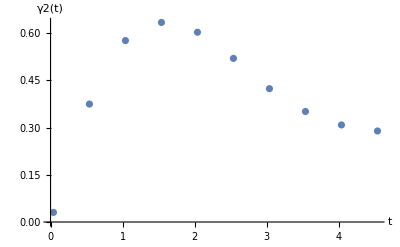

```mathematica
TABLEγ2direct=Table[{t,γ2direct[t, βp, λp,γp,0,3]},{t,0.04,5,0.5}]
ListPlot[TABLEγ2direct,AxesLabel->{"t","γ2(t)"}]
```

NIntegrate::inumr: The integrand (0.031831 ω Cos[(0.04-t1) ω] Coth[ω/2])/(0.25+ω^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3}}.

NIntegrate::inumr: The integrand -(0.031831 ω Sin[(0.04-t1) ω])/(0.25+ω^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3}}.

NIntegrate::inumr: The integrand (0.031831 ω Cos[(0.04-t1) ω] Coth[ω/2])/(0.25+ω^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0.04,0.0152287},{0.54,0.180692},{1.04,0.25468},{1.54,0.252837},{2.04,0.219533},{2.54,0.168829},{3.04,0.116095},{3.54,0.0814646},{4.04,0.0640145},{4.54,0.057796}}

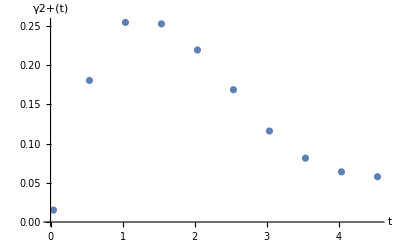

```mathematica
TABLEγ2plusdirect=Table[{t,γ2plusdirect[t, βp, λp,γp,0,3]},{t,0.04,5,0.5}]
ListPlot[TABLEγ2plusdirect,AxesLabel->{"t","γ2+(t)"}]
```

#### TCL 4

```mathematica
Clear[alpha1direct]
alpha1directInt1[t_?NumericQ,t1_?NumericQ,t2_?NumericQ, β_?NumericQ, λ_?NumericQ,γ_?NumericQ,minf_?NumericQ,Msup_?NumericQ]:=NIntegrate[νdirect[t-t2,β, λ,γ,minf,Msup]νdirect[t1-t3,β, λ,γ,minf,Msup]Sin[t1-t2]Sin[t-t3],{t3,0,t2}]
alpha1directInt2[t_?NumericQ,t1_?NumericQ, β_?NumericQ, λ_?NumericQ,γ_?NumericQ,minf_?NumericQ,Msup_?NumericQ]:=NIntegrate[alpha1directInt2[t,t1,t2, β, λ,γ,minf,Msup],{t2,0,t1}]
alpha1direct[t_?NumericQ,β_?NumericQ, λ_?NumericQ,γ_?NumericQ,minf_?NumericQ,Msup_?NumericQ]:=NIntegrate[alpha1directInt2[t,t1, β, λ,γ,minf,Msup],{t1,0,t}]

alpha1direct[t_, β_, λ_,γ_,minf_,Msup_]:=16  NIntegrate[NIntegrate[NIntegrate[νdirect[t-t2,β, λ,γ,minf,Msup]νdirect[t1-t3,β, λ,γ,minf,Msup]Sin[t1-t2]Sin[t-t3],{t3,0,t2}],{t2,0,t1}],{t1,0,t}]

(*alpha1direct[1,βp, λp,γp,0,1]*)
alpha1direct[3,1/Tp, λp,γp,0.1,3]
```

NIntegrate::inumr: The integrand alpha1directInt2[3,3,t2,1,0.1,0.5,0.1,3] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate[alpha1directInt2[3,t1,1,0.1,0.5,0.1,3],{t1,0,3}]

```mathematica
TABLEγ2direct=Table[{t,γ2direct[t, βp, λp,γp,0,3]},{t,0.04,5,0.5}]
ListPlot[TABLEγ2direct,AxesLabel->{"t","γ2(t)"}]
```

### Manually get rho11

Como se tarda demasiado el sacar los puntos para gamma tcl4 la idea es hacer puntos de la grafica de gamma tcl 2 y tcl 4 y aproximar una curva polinomial, para asi poder obtener int1 que es la ∫_0^t ⅆt1 γ[t1] e int2 que es la grafica de ∫_0^t ⅆt1 γ[t1]Exp[-γ[t1]]
For the parameters Tp=1, gamma=0.5, and lambda=0.1

0.544527

0.544527

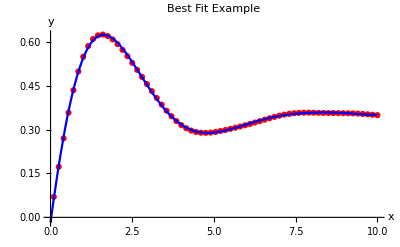

1.81712

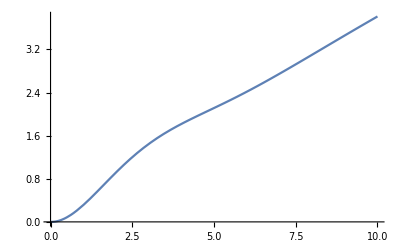

```mathematica
Clear[BestFitFunction,int1fun,data,bestFitLine,fittedFunction,int1GammaTCL2,GammaTCL2,data, f]
BestFitFunction[data_List]:=Module[{model,fitParams,bestFitLine},(*Define the model you want to fit,here a linear model y=a x+b*)model=a x^8+b x^7+c x^6 +d x^5 + e x^4+f x^3 +g x^2+h x+l;
(*Perform the fitting to find the best parameters a and b*)fitParams=FindFit[data,model,{a,b,c,d,e,f,g,h,l},x];
(*Define bestFitLine as a function of x using the fitted parameters*)bestFitLine[x_]:=(a x^8+b x^7+c x^6 +d x^5 + e x^4+f x^3 +g x^2+h x+l)/. fitParams;
(*Return the function bestFitLine*)bestFitLine]
GammaTCL2indirectPlot={0.0701,0.1729,0.2698,0.3578,0.4346,0.4984,0.5487,0.5855,0.6095,0.6220,0.6247,0.6194,0.6079,0.5918,0.5724,0.5509,0.5279,0.5041,0.4798,0.4554,0.4313,0.4078,0.3853,0.3644,0.3455,0.3290,0.3153,0.3045,0.2967,0.2917,0.2892,0.2887,0.2898,0.2921,0.2952,0.2987,0.3024,0.3063,0.3104,0.3147,0.3192,0.3239,0.3288,0.3338,0.3387,0.3434,0.3476,0.3511,0.3539,0.3559,0.3571,0.3577,0.3578,0.3576,0.3572,0.3568,0.3566,0.3564,0.3562,0.3561,0.3558,0.3553,0.3546,0.3535,0.3522,0.3507,0.3492};
data=Transpose[{Range[0.1,10,0.15],GammaTCL2indirectPlot}];
GammaTCL2=BestFitFunction[data];
GammaTCL2eva[t_?NumericQ]:=-0.016708466839370942+0.8271438700848256 t-0.20250843521311684 t^2-0.11950902747978931 t^3+0.06917577334216812 t^4-0.01453307487444239 t^5+0.0015480605065005262 t^6-0.00008392277297013213 t^7+1.845731583640409*^-6 t^8;
GammaTCL2[1]
GammaTCL2eva[1]
Show[ListPlot[data,PlotStyle->Red],Plot[GammaTCL2[x],{x,0,10},PlotStyle->Blue],PlotRange->All,AxesLabel->{"x","y"},PlotLabel->"Best Fit Example"]
int1GammaTCL2[t_?NumericQ]:=NIntegrate[GammaTCL2eva[tp],{tp,0,t}]
int1GammaTCL2[4]
Plot[int1GammaTCL2[x],{x,0,10}]
```

-Graphics-

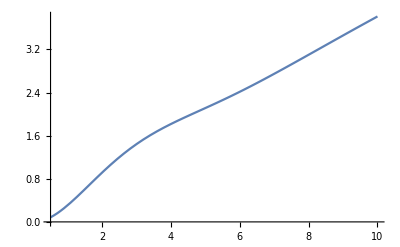

```mathematica
Clear[BestFitFunction,int1fun,data,bestFitLine,fittedFunction,data, f]
BestFitFunction[data_List]:=Module[{model,fitParams,bestFitLine},(*Define the model you want to fit,here a linear model y=a x+b*)model=a x^8+b x^7+c x^6 +d x^5 + e x^4+f x^3 +g x^2+h x+l;
(*Perform the fitting to find the best parameters a and b*)fitParams=FindFit[data,model,{a,b,c,d,e,f,g,h,l},x];
(*Define bestFitLine as a function of x using the fitted parameters*)bestFitLine[x_]:=(a x^8+b x^7+c x^6 +d x^5 + e x^4+f x^3 +g x^2+h x+l)/. fitParams;
(*Return the function bestFitLine*)bestFitLine]
GammaTCL2plusindirectPlot={0.0350,0.0860,0.1332,0.1746,0.2088,0.2349,0.2527,0.2626,0.2652,0.2618,0.2536,0.2420,0.2283,0.2135,0.1983,0.1834,0.1690,0.1551,0.1417,0.1289,0.1166,0.1049,0.0939,0.0840,0.0753,0.0681,0.0627,0.0590,0.0572,0.0569,0.0580,0.0602,0.0630,0.0661,0.0693,0.0723,0.0751,0.0776,0.0800,0.0822,0.0845,0.0869,0.0893,0.0918,0.0943,0.0966,0.0985,0.1000,0.1009,0.1013,0.1012,0.1006,0.0998,0.0989,0.0980,0.0972,0.0967,0.0964,0.0962,0.0962,0.0961,0.0959,0.0955,0.0950,0.0943,0.0935,0.0926};
data=Transpose[{Range[0.1,10,0.15],GammaTCL2indirectPlot}];
GammaplusTCL2=BestFitFunction[data];
Show[ListPlot[data,PlotStyle->Red],Plot[GammaplusTCL2[x],{x,0,10},PlotStyle->Blue],PlotRange->All,AxesLabel->{"x","y"},PlotLabel->"Best Fit Example"]
int2GammaTCL2plusExpon[t_]:=NIntegrate[GammaplusTCL2[tp]Exp[int1GammaTCL2[tp]],{tp,0,t}]
Plot[int1GammaTCL2[x],{x,0.5,10}]
```

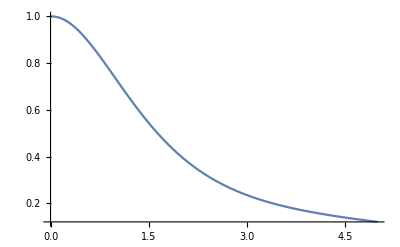

```mathematica
(*NIntegrate[γPlusBRDL[tp,β,λ,γ]Exp[int1BRDL[tp,β,λ,γ]]*)
ρ11BRDL[t_,ρ0_]:=Exp[-int1GammaTCL2[t]](ρ0+int2GammaTCL2plusExpon[t])
Plot[1-ρ11BRDL[t,0],{t,0,5}]
```

```mathematica
Range[0,5,0.125]
```

Empezamos con los datos de matlab, primero los

{{0,1},{0.0005,0.9999},{0.0011,0.9999},{0.0016,0.9998},{0.0022,0.9998},{0.0049,0.9995},{0.0076,0.9993},{0.0103,0.999},{0.0129,0.9988},{0.0264,0.9975},{0.0399,0.9963},{0.0534,0.9951},{0.0669,0.9938},{0.1343,0.9878},{0.2018,0.9819},{0.2692,0.9761},{0.3367,0.9704},{0.4617,0.9603},{0.5867,0.9506},{0.7117,0.9413},{0.8367,0.9324},{0.9617,0.9238},{1.0867,0.9157},{1.2117,0.9079},{1.3367,0.9004},{1.4617,0.8932},{1.5867,0.8863},{1.7117,0.8797},{1.8367,0.8735},{1.9617,0.8674},{2.0867,0.8616},{2.2117,0.8561},{2.3367,0.8508},{2.4617,0.8457},{2.5867,0.8409},{2.7117,0.8362},{2.8367,0.8318},{2.9617,0.8275},{3.0867,0.8234},{3.2117,0.8195},{3.3367,0.8158},{3.4617,0.8122},{3.5867,0.8087},{3.7117,0.8055},{3.8367,0.8023},{3.9617,0.7993},{4.0867,0.7964},{4.2117,0.7936},{4.3367,0.791},{4.4617,0.7884},{4.5867,0.786},{4.7117,0.7837},{4.8367,0.7815},{4.8775,0.7807},{4.9183,0.78},{4.9592,0.7794},{5.,0.7787}}

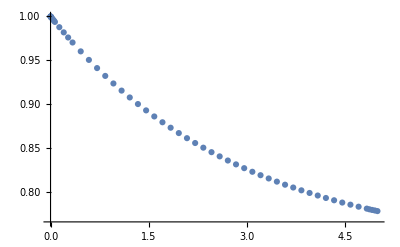

```mathematica
T1={0,0.0005,0.0011,0.0016,0.0022,0.0049,0.0076,0.0103,0.0129,0.0264,0.0399,0.0534,0.0669,0.1343,0.2018,0.2692,0.3367,0.4617,0.5867,0.7117,0.8367,0.9617,1.0867,1.2117,1.3367,1.4617,1.5867,1.7117,1.8367,1.9617,2.0867,2.2117,2.3367,2.4617,2.5867,2.7117,2.8367,2.9617,3.0867,3.2117,3.3367,3.4617,3.5867,3.7117,3.8367,3.9617,4.0867,4.2117,4.3367,4.4617,4.5867,4.7117,4.8367,4.8775,4.9183,4.9592,5.0000};
Y1={1,0.9999,0.9999,0.9998,0.9998,0.9995,0.9993,0.9990,0.9988,0.9975,0.9963,0.9951,0.9938,0.9878,0.9819,0.9761,0.9704,0.9603,0.9506,0.9413,0.9324,0.9238,0.9157,0.9079,0.9004,0.8932,0.8863,0.8797,0.8735,0.8674,0.8616,0.8561,0.8508,0.8457,0.8409,0.8362,0.8318,0.8275,0.8234,0.8195,0.8158,0.8122,0.8087,0.8055,0.8023,0.7993,0.7964,0.7936,0.7910,0.7884,0.7860,0.7837,0.7815,0.7807,0.7800,0.7794,0.7787};
Transpose[{T1,Y1}]
ListPlot[Transpose[{T1,Y1}]]
```

{0,0.125,0.25,0.375,0.5,0.625,0.75,0.875,1.,1.125,1.25,1.375,1.5,1.625,1.75,1.875,2.,2.125,2.25,2.375,2.5,2.625,2.75,2.875,3.,3.125,3.25,3.375,3.5,3.625,3.75,3.875,4.,4.125,4.25,4.375,4.5,4.625,4.75,4.875,5.}

{1.,0.9978,0.9912,0.9806,0.9664,0.9493,0.93,0.9092,0.8877,0.866,0.8449,0.8248,0.806,0.7888,0.7734,0.7599,0.7483,0.7385,0.7305,0.7242,0.7194,0.7159,0.7137,0.7126,0.7124,0.713,0.7141,0.7157,0.7176,0.7198,0.722,0.7243,0.7264,0.7285,0.7303,0.732,0.7335,0.7347,0.7357,0.7366,0.7373}

{{0,1.},{0.125,0.9978},{0.25,0.9912},{0.375,0.9806},{0.5,0.9664},{0.625,0.9493},{0.75,0.93},{0.875,0.9092},{1.,0.8877},{1.125,0.866},{1.25,0.8449},{1.375,0.8248},{1.5,0.806},{1.625,0.7888},{1.75,0.7734},{1.875,0.7599},{2.,0.7483},{2.125,0.7385},{2.25,0.7305},{2.375,0.7242},{2.5,0.7194},{2.625,0.7159},{2.75,0.7137},{2.875,0.7126},{3.,0.7124},{3.125,0.713},{3.25,0.7141},{3.375,0.7157},{3.5,0.7176},{3.625,0.7198},{3.75,0.722},{3.875,0.7243},{4.,0.7264},{4.125,0.7285},{4.25,0.7303},{4.375,0.732},{4.5,0.7335},{4.625,0.7347},{4.75,0.7357},{4.875,0.7366},{5.,0.7373}}

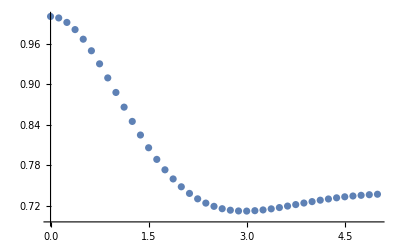

```mathematica
T2={0,0.1250,0.2500,0.3750,0.5000,0.6250,0.7500,0.8750,1.0000,1.1250,1.2500,1.3750,1.5000,1.6250,1.7500,1.8750,2.0000,2.1250,2.2500,2.3750,2.5000,2.6250,2.7500,2.8750,3.0000,3.1250,3.2500,3.3750,3.5000,3.6250,3.7500,3.8750,4.0000,4.1250,4.2500,4.3750,4.5000,4.6250,4.7500,4.8750,5.0000}
Y2={1.0000,0.9978,0.9912,0.9806,0.9664,0.9493,0.9300,0.9092,0.8877,0.8660,0.8449,0.8248,0.8060,0.7888,0.7734,0.7599,0.7483,0.7385,0.7305,0.7242,0.7194,0.7159,0.7137,0.7126,0.7124,0.7130,0.7141,0.7157,0.7176,0.7198,0.7220,0.7243,0.7264,0.7285,0.7303,0.7320,0.7335,0.7347,0.7357,0.7366,0.7373}
Transpose[{T2,Y2}]
ListPlot[Transpose[{T2,Y2}]]
```

TCL 4 matlab data
ts4
4short represents gammaplus incorrecta, por lo que gamma total esta bien mientras que gamma plus fue cambiada para

```mathematica
T4short={0,0.1250,0.2500,0.3750,0.5000,0.6250,0.7500,0.8750,1.0000,1.1250,1.2500,1.3750,1.5000,1.6250,1.7500,1.8750,2.0000,2.1250,2.2500,2.3750,2.5000,2.6250,2.7500,2.8750,3.0000,3.1250,3.2500,3.3750,3.5000,3.6250,3.7500,3.8750,4.0000,4.1250,4.2500,4.3750,4.5000,4.6250,4.7500,4.8750,5.0000};
Y4short={1.0000,0.9978,0.9912,0.9806,0.9664,0.9493,0.9300,0.9093,0.8879,0.8667,0.8463,0.8273,0.8104,0.7961,0.7846,0.7764,0.7715,0.7699,0.7715,0.7761,0.7832,0.7924,0.8032,0.8151,0.8276,0.8403,0.8528,0.8648,0.8761,0.8865,0.8959,0.9042,0.9115,0.9177,0.9230,0.9273,0.9308,0.9336,0.9357,0.9372,0.9382};

T4={0,0.1250,0.2500,0.3750,0.5000,0.6250,0.7500,0.8750,1.0000,1.1250,1.2500,1.3750,1.5000,1.6250,1.7500,1.8750,2.0000,2.1250,2.2500,2.3750,2.5000,2.6250,2.7500,2.8750,3.0000,3.1250,3.2500,3.3750,3.5000,3.6250,3.7500,3.8750,4.0000,4.1250,4.2500,4.3750,4.5000,4.6250,4.7500,4.8750,5.0000};

Y4={1.0000,0.9978,0.9912,0.9806,0.9664,0.9494,0.9303,0.9101,0.8896,0.8698,0.8516,0.8361,0.8240,0.8161,0.8130,0.8150,0.8222,0.8345,0.8515,0.8727,0.8973,0.9242,0.9526,0.9814,1.0099,1.0372,1.0626,1.0858,1.1064,1.1241,1.1391,1.1512,1.1607,1.1677,1.1724,1.1751,1.1760,1.1754,1.1736,1.1708,1.1673};
```

```mathematica
Transpose[{T4,Y4}]
```

{{0,1.},{0.125,0.9978},{0.25,0.9912},{0.375,0.9806},{0.5,0.9664},{0.625,0.9494},{0.75,0.9303},{0.875,0.9101},{1.,0.8896},{1.125,0.8698},{1.25,0.8516},{1.375,0.8361},{1.5,0.824},{1.625,0.8161},{1.75,0.813},{1.875,0.815},{2.,0.8222},{2.125,0.8345},{2.25,0.8515},{2.375,0.8727},{2.5,0.8973},{2.625,0.9242},{2.75,0.9526},{2.875,0.9814},{3.,1.0099},{3.125,1.0372},{3.25,1.0626},{3.375,1.0858},{3.5,1.1064},{3.625,1.1241},{3.75,1.1391},{3.875,1.1512},{4.,1.1607},{4.125,1.1677},{4.25,1.1724},{4.375,1.1751},{4.5,1.176},{4.625,1.1754},{4.75,1.1736},{4.875,1.1708},{5.,1.1673}}

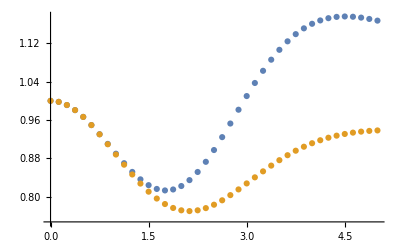

```mathematica
ListPlot[{Transpose[{T4,Y4}],Transpose[{T4short,Y4short}]}]
```

Again lets check details of K4

```mathematica
rho
```

{{1-ρ11,ρ01},{ρ10,ρ11}}

For tcl2

```mathematica
FullSimplify[-(ν01 Commut[SΩt[t],Commut[SΩt[t1],rho]]+I η01 Commut[SΩt[t],Anticommut[SΩt[t1],rho]])]//MatrixForm
```

(2 ν01 (-1+2 ρ11) Cos[(t-t1) Ω]-2 η01 Sin[(t-t1) Ω] | 2 ⅇ^(-ⅈ (t+t1) Ω) ν01 (-ⅇ^(2 ⅈ t1 Ω) ρ01+ρ10)
2 ⅇ^(ⅈ (t-t1) Ω) ν01 (ⅇ^(2 ⅈ t1 Ω) ρ01-ρ10) | 2 ν01 (1-2 ρ11) Cos[(t-t1) Ω]+2 η01 Sin[(t-t1) Ω])

For tcl4

```mathematica
FullSimplify[ν02 ν13 Commut[SΩt[t],Commut[Commut[SΩt[t1],SΩt[t2]],Commut[SΩt[t3],rho]]]+I ν02 η13  Commut[SΩt[t],Commut[Commut[SΩt[t1],SΩt[t2]],Anticommut[SΩt[t3],rho]]]]//MatrixForm
```

(-8 ν02 Sin[(t1-t2) Ω] (η13 Cos[(t-t3) Ω]+ν13 (-1+2 ρ11) Sin[(t-t3) Ω]) | 0
0 | 8 ν02 Sin[(t1-t2) Ω] (η13 Cos[(t-t3) Ω]+ν13 (-1+2 ρ11) Sin[(t-t3) Ω]))

```mathematica
FullSimplify[I η02 ν13  Commut[SΩt[t],Anticommut[Commut[SΩt[t1],SΩt[t2]],Commut[SΩt[t3],rho]]]-η02 η13  Commut[SΩt[t],Anticommut[Commut[SΩt[t1],SΩt[t2]],Anticommut[SΩt[t3],rho]]]]//MatrixForm
```

(0 | 4 ⅇ^(-ⅈ (t+t1+t2+t3) Ω) (-ⅇ^(2 ⅈ t1 Ω)+ⅇ^(2 ⅈ t2 Ω)) η02 η13 (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10)
4 ⅇ^(ⅈ (t-t1-t2-t3) Ω) (ⅇ^(2 ⅈ t1 Ω)-ⅇ^(2 ⅈ t2 Ω)) η02 η13 (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10) | 0)

```mathematica
FullSimplify[ ν03 ν12 Commut[SΩt[t],Commut[Commut[SΩt[t1],SΩt[t3]],Commut[SΩt[t2],rho]]]+I ν03 η12  Commut[SΩt[t],Commut[Commut[SΩt[t1],SΩt[t3]],Anticommut[SΩt[t2],rho]]]]//MatrixForm
```

(-8 ν03 (η12 Cos[(t-t2) Ω]+ν12 (-1+2 ρ11) Sin[(t-t2) Ω]) Sin[(t1-t3) Ω] | 0
0 | 8 ν03 (η12 Cos[(t-t2) Ω]+ν12 (-1+2 ρ11) Sin[(t-t2) Ω]) Sin[(t1-t3) Ω])

```mathematica
FullSimplify[ I η03 ν12 Commut[SΩt[t],Anticommut[Commut[SΩt[t1],SΩt[t3]],Commut[SΩt[t2],rho]]]-η03 η12 Commut[SΩt[t],Anticommut[Commut[SΩt[t1],SΩt[t3]],Anticommut[SΩt[t2],rho]]] ]//MatrixForm
```

(0 | 4 ⅇ^(-ⅈ (t+t1+t2+t3) Ω) (-ⅇ^(2 ⅈ t1 Ω)+ⅇ^(2 ⅈ t3 Ω)) η03 η12 (ⅇ^(2 ⅈ t2 Ω) ρ01+ρ10)
4 ⅇ^(ⅈ (t-t1-t2-t3) Ω) (ⅇ^(2 ⅈ t1 Ω)-ⅇ^(2 ⅈ t3 Ω)) η03 η12 (ⅇ^(2 ⅈ t2 Ω) ρ01+ρ10) | 0)

```mathematica
FullSimplify[( ν03 ν12- η03 η12)Commut[SΩt[t],Commut[SΩt[t1],Commut[Commut[SΩt[t2],SΩt[t3]],rho]]] ]//MatrixForm
FullSimplify[I( ν03  η12+ η03ν12)Commut[SΩt[t],Commut[SΩt[t1],Anticommut[Commut[SΩt[t2],SΩt[t3]],rho]]] ]//MatrixForm
```

(0 | 4 ⅇ^(-ⅈ (t+t1+t2+t3) Ω) (ⅇ^(2 ⅈ t2 Ω)-ⅇ^(2 ⅈ t3 Ω)) (η03 η12-ν03 ν12) (ⅇ^(2 ⅈ t1 Ω) ρ01+ρ10)
4 ⅇ^(ⅈ (t-t1-t2-t3) Ω) (-ⅇ^(2 ⅈ t2 Ω)+ⅇ^(2 ⅈ t3 Ω)) (η03 η12-ν03 ν12) (ⅇ^(2 ⅈ t1 Ω) ρ01+ρ10) | 0)

(8 (η03ν12+η12 ν03) Cos[(t-t1) Ω] Sin[(t2-t3) Ω] | 0
0 | -8 (η03ν12+η12 ν03) Cos[(t-t1) Ω] Sin[(t2-t3) Ω])

```mathematica
FullSimplify[ExpToTrig[ν02 ν13 Commut[SΩt[t],Commut[Commut[SΩt[t1],SΩt[t2]],Commut[SΩt[t3],rho]]]+I ν02 η13  Commut[SΩt[t],Commut[Commut[SΩt[t1],SΩt[t2]],Anticommut[SΩt[t3],rho]]]+
I η02 ν13  Commut[SΩt[t],Anticommut[Commut[SΩt[t1],SΩt[t2]],Commut[SΩt[t3],rho]]]-η02 η13  Commut[SΩt[t],Anticommut[Commut[SΩt[t1],SΩt[t2]],Anticommut[SΩt[t3],rho]]]+ ν03 ν12 Commut[SΩt[t],Commut[Commut[SΩt[t1],SΩt[t3]],Commut[SΩt[t2],rho]]]+I ν03 η12  Commut[SΩt[t],Commut[Commut[SΩt[t1],SΩt[t3]],Anticommut[SΩt[t2],rho]]]+I η03 ν12 Commut[SΩt[t],Anticommut[Commut[SΩt[t1],SΩt[t3]],Commut[SΩt[t2],rho]]]-η03 η12 Commut[SΩt[t],Anticommut[Commut[SΩt[t1],SΩt[t3]],Anticommut[SΩt[t2],rho]]] +( ν03 ν12- η03 η12)Commut[SΩt[t],Commut[SΩt[t1],Commut[Commut[SΩt[t2],SΩt[t3]],rho]]] +I( ν03  η12+ η03ν12)Commut[SΩt[t],Commut[SΩt[t1],Anticommut[Commut[SΩt[t2],SΩt[t3]],rho]]] ]]//MatrixForm
```

(4 ((ν03 ν12+ν02 ν13) (-1+2 ρ11) Cos[(t+t1-t2-t3) Ω]+ν02 ν13 (1-2 ρ11) Cos[(t-t1+t2-t3) Ω]+ν03 ν12 (1-2 ρ11) Cos[(t-t1-t2+t3) Ω]-(η13 ν02+η12 ν03) (Sin[(t+t1-t2-t3) Ω]-Sin[(t-t1+t2-t3) Ω])+η03ν12 (Sin[(t-t1+t2-t3) Ω]-Sin[(t-t1-t2+t3) Ω])) | 8 ⅇ^(-ⅈ t Ω) (η03 η12 (-ⅈ (ρ01+ρ10) Cos[t2 Ω]+(ρ01-ρ10) Sin[t2 Ω]) Sin[(t1-t3) Ω]+(η03 η12-ν03 ν12) (ⅈ (ρ01+ρ10) Cos[t1 Ω]+(-ρ01+ρ10) Sin[t1 Ω]) Sin[(t2-t3) Ω]+η02 η13 Sin[(t1-t2) Ω] (-ⅈ (ρ01+ρ10) Cos[t3 Ω]+(ρ01-ρ10) Sin[t3 Ω]))
8 ⅇ^(ⅈ t Ω) (η03 η12 (ⅈ (ρ01+ρ10) Cos[t2 Ω]+(-ρ01+ρ10) Sin[t2 Ω]) Sin[(t1-t3) Ω]+(η03 η12-ν03 ν12) (-ⅈ (ρ01+ρ10) Cos[t1 Ω]+(ρ01-ρ10) Sin[t1 Ω]) Sin[(t2-t3) Ω]+η02 η13 Sin[(t1-t2) Ω] (ⅈ (ρ01+ρ10) Cos[t3 Ω]+(-ρ01+ρ10) Sin[t3 Ω])) | 4 (-((ν03 ν12+ν02 ν13) (-1+2 ρ11) Cos[(t+t1-t2-t3) Ω])+ν02 ν13 (-1+2 ρ11) Cos[(t-t1+t2-t3) Ω]+ν03 ν12 (-1+2 ρ11) Cos[(t-t1-t2+t3) Ω]+(η13 ν02+η12 ν03) (Sin[(t+t1-t2-t3) Ω]-Sin[(t-t1+t2-t3) Ω])+η03ν12 (-Sin[(t-t1+t2-t3) Ω]+Sin[(t-t1-t2+t3) Ω])))

```mathematica
Integrate[η ω Exp[-ω/ωc]Coth[β ω/2]Cos[ω τ],{ω,0,Infinity}]
```

$Aborted

```mathematica
Integrate[η ω Exp[-ω/ωc]Sin[ω τ],{ω,0,Infinity}]
```

ConditionalExpression[(2 η τ ωc^3)/((1+τ^2 ωc^2)^2), Re[1/ωc]>Abs[Im[τ]]]

```mathematica
Integrate[η ω Exp[-ω/ωc],{ω,0,Infinity}]
```

ConditionalExpression[η ωc^2, Re[ωc]>0]

```mathematica
Integrate[ Exp[-x]Sin[x a],{x,0,Infinity}]
```

ConditionalExpression[a/(1+a^2), Abs[Im[a]]<1]

```mathematica
Integrate[ x Exp[-x]Sin[x a],{x,0,Infinity}]
```

ConditionalExpression[(2 a)/((1+a^2)^2), Abs[Im[a]]<1]

```mathematica
Integrate[ x Exp[-x]Cot[β x/2]Cos[x a],{x,0,Infinity}]
```

∫_0^∞ ⅇ^-x x Cos[a x] Cot[(x β)/2]ⅆx

```mathematica
FullSimplify[Integrate[ x Cot[β x/2]Cos[x a],{x,0,xc}]]
```

1/(2 a^2 β^2)ⅇ^(-ⅈ a xc) (2 ⅈ a^2 ⅇ^(ⅈ a xc) π^2 Csc[(a π)/β]^2-2 ⅈ a^2 HurwitzLerchPhi[ⅇ^(ⅈ xc β),2,-a/β]+β^2 (ⅈ-a xc+2 a xc Hypergeometric2F1[1,-a/β,1-a/β,ⅇ^(ⅈ xc β)])+ⅇ^(2 ⅈ a xc) (-2 ⅈ a^2 HurwitzLerchPhi[ⅇ^(ⅈ xc β),2,a/β]+β^2 (ⅈ+a xc-2 a xc Hypergeometric2F1[1,a/β,(a+β)/β,ⅇ^(ⅈ xc β)])))

```mathematica
FullSimplify[Integrate[ x Sin[x a],{x,0,xc}]]
```

(-a xc Cos[a xc]+Sin[a xc])/a^2

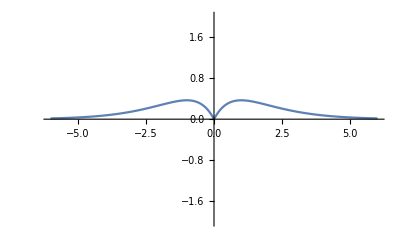

```mathematica
Clear[function]
function1[ω_,α_,β_,t_]:=Abs[ω] Exp[-Abs[ω]/α] Coth[(β ω)/2](Sin[(1+ω)t]/(1+ω)+Sin[(1-ω)t]/(1-ω))
function2[ω_,α_,β_,t_]:=ω Exp[-ω/α] Coth[(β Abs[ω])/2](Sin[(1+ω)t]/(1+ω))
function3[ω_,α_,β_,t_]:=Abs[ω] Exp[-Abs[ω]/α] Coth[(β ω)/2](Sin[(1-ω)t]/(1-ω))
Plot[{Abs[ω] Exp[-Abs[ω]/1] },{ω,-6,6},PlotRange->{-2,2}]
```

```mathematica
γtcl2Ohm02Inf[α_,β_,t_]:=NIntegrate[Abs[ω] Exp[-Abs[ω]/α]  Coth[(β ω)/2](Sin[(1+ω)t]/(1+ω)+Sin[(1-ω)t]/(1-ω)),{ω,0,Infinity}]
γtcl2OhmInf2Inf[α_,β_,t_]:=NIntegrate[Abs[ω] Exp[-Abs[ω]/α]  Coth[(β ω)/2](Sin[(1+ω)t]/(1+ω)),{ω,-Infinity,Infinity}]
(*γtcl2AbsOhmInf2Inf[α_,β_,t_]:=NIntegrate[Abs[ω] Exp[-Abs[ω]/α] Coth[(β ω)/2](Sin[(1+ω)t]/(1+ω)),{ω,-Infinity,Infinity}]
γtcl2AbsOhmInf2Inf[1,1,1]*)
γtcl2Ohm02Inf[1,1,1]
γtcl2OhmInf2Inf[1,1,1]
```

2.90355

NIntegrate::deorel: The relative error 1.13196 is larger than expected for the integrand -(ⅇ^(-Abs[ω]) Abs[ω] Cos[ω] Coth[Abs[ω]/2] Sin[1])/(1-Abs[ω]) over {0,∞} with DoubleExponentialOscillatory method and tuning parameters, TuningParameters -> {10,5}.

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand -(ⅇ^(-Abs[ω]) Abs[ω] Cos[ω] Coth[Abs[ω]/2] Sin[1])/(1-Abs[ω]) over {0,∞}. DoubleExponentialOscillatory obtained -29.729 and 11.3196 for the integral and error estimates.

-0.926682

```mathematica
Eigenvalues[{{-2b,0,0,2a},{0,-(a+b),0,0},{0,0,-(a+b),0},{2b,0,0,-2a}}]
Eigenvectors[{{-2b,0,0,2a},{0,-(a+b),0,0},{0,0,-(a+b),0},{2b,0,0,-2a}}]
```

{0,-a-b,-a-b,-2 (a+b)}

{{a/b,0,0,1},{0,0,1,0},{0,1,0,0},{-1,0,0,1}}

```mathematica
Eigenvalues[Transpose[{{-2b,0,0,2a},{0,-(a+b),0,0},{0,0,-(a+b),0},{2b,0,0,-2a}}]]
```

{0,-a-b,-a-b,-2 (a+b)}

```mathematica
Eigenvectors[Transpose[{{-2b,0,0,2a},{0,-(a+b),0,0},{0,0,-(a+b),0},{2b,0,0,-2a}}]]
```

{{1,0,0,1},{0,0,1,0},{0,1,0,0},{-b/a,0,0,1}}

```mathematica
ts2Temp5={0,0.0000,0.0001,0.0001,0.0001,0.0003,0.0004,0.0005,0.0007,0.0014,0.0021,0.0028,0.0034,0.0069,0.0104,0.0139,0.0174,0.0347,0.0521,0.0695,0.0869,0.1273,0.1677,0.2080,0.2484,0.2968,0.3452,0.3936,0.4420,0.4996,0.5573,0.6149,0.6726,0.7408,0.8090,0.8772,0.9454,1.0272,1.1091,1.1909,1.2728,1.3735,1.4742,1.5748,1.6755,1.8005,1.9255,2.0505,2.1755,2.3005,2.4255,2.5505,2.6755,2.8005,2.9255,3.0505,3.1755,3.3005,3.4255,3.5505,3.6755,3.8005,3.9255,4.0505,4.1755,4.3005,4.4255,4.5505,4.6755,4.7566,4.8378,4.9189,5.0000}

ys2Temp5={1.0000,0.9945,0.9784,0.9530,0.9198,0.8811,0.8391,0.7961,0.7540,0.7143,0.6782,0.6464,0.6190,0.5962,0.5775,0.5626,0.5511,0.5431,0.5370,0.5325,0.5294,0.5273,0.5261,0.5255,0.5255,0.5260,0.5267,0.5277,0.5289,0.5302,0.5315,0.5330,0.5344,0.5359,0.5374,0.5388,0.5401,0.5413,0.5424,0.5435,0.5444,0.5452,0.5459,0.5465,0.5470,0.5475,0.5478,0.5481,0.5484,0.5486,0.5488,0.5490,0.5492,0.5494,0.5496,0.5498,0.5500,0.5503,0.5506,0.5508,0.5511,0.5514,0.5517,0.5520,0.5523,0.5525,0.5527,0.5529,0.5531,0.5532,0.5532,0.5532,0.5532,0.5530,0.5529,0.5527,0.5525,0.5522,0.5519,0.5516,0.5513,0.5512,0.5511,0.5511,0.5510,0.5510,0.5509,0.5509,0.5508}
Dimensions[ys2Temp5]
```

{0,0.,0.0001,0.0001,0.0001,0.0003,0.0004,0.0005,0.0007,0.0014,0.0021,0.0028,0.0034,0.0069,0.0104,0.0139,0.0174,0.0347,0.0521,0.0695,0.0869,0.1273,0.1677,0.208,0.2484,0.2968,0.3452,0.3936,0.442,0.4996,0.5573,0.6149,0.6726,0.7408,0.809,0.8772,0.9454,1.0272,1.1091,1.1909,1.2728,1.3735,1.4742,1.5748,1.6755,1.8005,1.9255,2.0505,2.1755,2.3005,2.4255,2.5505,2.6755,2.8005,2.9255,3.0505,3.1755,3.3005,3.4255,3.5505,3.6755,3.8005,3.9255,4.0505,4.1755,4.3005,4.4255,4.5505,4.6755,4.7566,4.8378,4.9189,5.}

{1.,0.9945,0.9784,0.953,0.9198,0.8811,0.8391,0.7961,0.754,0.7143,0.6782,0.6464,0.619,0.5962,0.5775,0.5626,0.5511,0.5431,0.537,0.5325,0.5294,0.5273,0.5261,0.5255,0.5255,0.526,0.5267,0.5277,0.5289,0.5302,0.5315,0.533,0.5344,0.5359,0.5374,0.5388,0.5401,0.5413,0.5424,0.5435,0.5444,0.5452,0.5459,0.5465,0.547,0.5475,0.5478,0.5481,0.5484,0.5486,0.5488,0.549,0.5492,0.5494,0.5496,0.5498,0.55,0.5503,0.5506,0.5508,0.5511,0.5514,0.5517,0.552,0.5523,0.5525,0.5527,0.5529,0.5531,0.5532,0.5532,0.5532,0.5532,0.553,0.5529,0.5527,0.5525,0.5522,0.5519,0.5516,0.5513,0.5512,0.5511,0.5511,0.551,0.551,0.5509,0.5509,0.5508}

{89}

Nueva expresion
< 02 > < 13 > [0, [1, 2] 3 ρ]
-< 02 > < 31 > [0, [1, 2] ρ3] - < 20 > < 13 > [0, 3 ρ[1, 2]]
+< 20 > < 31 > [0, ρ3[1, 2]] 
+ < 03 > < 12 > ([0, [3, 2] ρ1]+ [0, [12, 3] ρ])
      + < 30 > < 21 > ([0, 1 ρ[3, 2]]   + [0, ρ[21, 3]]) 
      - < 03 > < 21 > [0, [1, 3] ρ2]
-< 30 > < 12 > [0, 2 ρ[1, 3]]

< 02 > < 13 > [0, [1, 2] 3 ρ]

Ahora si, porque manana vamos al spartan

< 02 > < 13 > [0, [1, 2] 3 ρ]

```mathematica
FullSimplify[ Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t2]].SΩt[t3].rho]]//MatrixForm
FullSimplify[ (ν02+I η02) (ν13+I η13)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t2]].SΩt[t3].rho]]//MatrixForm
```

(2 Sin[(t1-t2) Ω] (ⅈ Cos[(t0-t3) Ω]+(1-2 ρ11) Sin[(t0-t3) Ω]) | ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (ⅇ^(2 ⅈ t1 Ω)-ⅇ^(2 ⅈ t2 Ω)) (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10)
ⅇ^(ⅈ (t0-t1-t2-t3) Ω) (-ⅇ^(2 ⅈ t1 Ω)+ⅇ^(2 ⅈ t2 Ω)) (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10) | -2 Sin[(t1-t2) Ω] (ⅈ Cos[(t0-t3) Ω]+(1-2 ρ11) Sin[(t0-t3) Ω]))

(-2 (η02-ⅈ ν02) (η13-ⅈ ν13) Sin[(t1-t2) Ω] (ⅈ Cos[(t0-t3) Ω]+(1-2 ρ11) Sin[(t0-t3) Ω]) | ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (-ⅇ^(2 ⅈ t1 Ω)+ⅇ^(2 ⅈ t2 Ω)) (η02-ⅈ ν02) (η13-ⅈ ν13) (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10)
ⅇ^(ⅈ (t0-t1-t2-t3) Ω) (ⅇ^(2 ⅈ t1 Ω)-ⅇ^(2 ⅈ t2 Ω)) (η02-ⅈ ν02) (η13-ⅈ ν13) (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10) | 2 (η02-ⅈ ν02) (η13-ⅈ ν13) Sin[(t1-t2) Ω] (ⅈ Cos[(t0-t3) Ω]+(1-2 ρ11) Sin[(t0-t3) Ω]))

-< 02 > < 31 > [0, [1, 2] ρ3] - < 20 > < 13 > [0, 3 ρ[1, 2]]

```mathematica
FullSimplify[ (ν02+I η02) (ν13+I η13)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t2]].SΩt[t3].rho]-(ν02+I η02)(ν13-I η13)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t2]].rho.SΩt[t3]]-(ν02-I η02)(ν13+I η13)Commut[SΩt[t0],SΩt[t3].rho.Commut[SΩt[t1],SΩt[t2]]]]//MatrixForm
```

(ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (-ⅇ^(2 ⅈ t1 Ω)+ⅇ^(2 ⅈ t2 Ω)) (ⅇ^(2 ⅈ t3 Ω) (ⅈ η13 ν02 (-2+ρ11)+η02 η13 ρ11+ⅈ η02 ν13 ρ11+ν02 ν13 (-2+3 ρ11))+ⅇ^(2 ⅈ t0 Ω) (-η02 (η13+ⅈ ν13) (-1+ρ11)+ν02 (ν13-3 ν13 ρ11-ⅈ η13 (1+ρ11)))) | ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (-ⅇ^(2 ⅈ t1 Ω)+ⅇ^(2 ⅈ t2 Ω)) (3 η02 η13-ⅈ η13 ν02-ⅈ η02 ν13+ν02 ν13) (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10)
ⅇ^(ⅈ (t0-t1-t2-t3) Ω) (ⅇ^(2 ⅈ t1 Ω)-ⅇ^(2 ⅈ t2 Ω)) (3 η02 η13-ⅈ η13 ν02-ⅈ η02 ν13+ν02 ν13) (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10) | ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (ⅇ^(2 ⅈ t1 Ω)-ⅇ^(2 ⅈ t2 Ω)) (ⅇ^(2 ⅈ t3 Ω) (ⅈ η13 ν02 (-2+ρ11)+η02 η13 ρ11+ⅈ η02 ν13 ρ11+ν02 ν13 (-2+3 ρ11))+ⅇ^(2 ⅈ t0 Ω) (-η02 (η13+ⅈ ν13) (-1+ρ11)+ν02 (ν13-3 ν13 ρ11-ⅈ η13 (1+ρ11)))))

```mathematica
FullSimplify[ Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t2]].rho.SΩt[t3]]]//MatrixForm
FullSimplify[ Commut[SΩt[t0],SΩt[t3].rho.Commut[SΩt[t1],SΩt[t2]]]]//MatrixForm

FullSimplify[ -(ν02+I η02)(ν13-I η13)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t2]].rho.SΩt[t3]]-(ν02-I η02)(ν13+I η13)Commut[SΩt[t0],SΩt[t3].rho.Commut[SΩt[t1],SΩt[t2]]]]//MatrixForm
```

(2 Sin[(t1-t2) Ω] (ⅈ Cos[(t0-t3) Ω]+(-1+2 ρ11) Sin[(t0-t3) Ω]) | ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (ⅇ^(2 ⅈ t1 Ω)-ⅇ^(2 ⅈ t2 Ω)) (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10)
ⅇ^(ⅈ (t0-t1-t2-t3) Ω) (-ⅇ^(2 ⅈ t1 Ω)+ⅇ^(2 ⅈ t2 Ω)) (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10) | 2 Sin[(t1-t2) Ω] (-ⅈ Cos[(t0-t3) Ω]+(1-2 ρ11) Sin[(t0-t3) Ω]))

(-2 Sin[(t1-t2) Ω] (ⅈ Cos[(t0-t3) Ω]+(1-2 ρ11) Sin[(t0-t3) Ω]) | ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (ⅇ^(2 ⅈ t1 Ω)-ⅇ^(2 ⅈ t2 Ω)) (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10)
ⅇ^(ⅈ (t0-t1-t2-t3) Ω) (-ⅇ^(2 ⅈ t1 Ω)+ⅇ^(2 ⅈ t2 Ω)) (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10) | 2 Sin[(t1-t2) Ω] (ⅈ Cos[(t0-t3) Ω]+(1-2 ρ11) Sin[(t0-t3) Ω]))

(4 Sin[(t1-t2) Ω] ((-η13 ν02+η02 ν13) Cos[(t0-t3) Ω]-(η02 η13+ν02 ν13) (-1+2 ρ11) Sin[(t0-t3) Ω]) | 2 ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (-ⅇ^(2 ⅈ t1 Ω)+ⅇ^(2 ⅈ t2 Ω)) (η02 η13+ν02 ν13) (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10)
2 ⅇ^(ⅈ (t0-t1-t2-t3) Ω) (ⅇ^(2 ⅈ t1 Ω)-ⅇ^(2 ⅈ t2 Ω)) (η02 η13+ν02 ν13) (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10) | 4 Sin[(t1-t2) Ω] ((η13 ν02-η02 ν13) Cos[(t0-t3) Ω]+(η02 η13+ν02 ν13) (-1+2 ρ11) Sin[(t0-t3) Ω]))

+< 20 > < 31 > [0, ρ3[1, 2]]

```mathematica
FullSimplify[ (ν02-I η02)(ν13-I η13)Commut[SΩt[t0],rho.SΩt[t3].Commut[SΩt[t1],SΩt[t2]]]]//MatrixForm
```

(2 (η02+ⅈ ν02) (η13+ⅈ ν13) Sin[(t1-t2) Ω] (ⅈ Cos[(t0-t3) Ω]+(-1+2 ρ11) Sin[(t0-t3) Ω]) | ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (-ⅇ^(2 ⅈ t1 Ω)+ⅇ^(2 ⅈ t2 Ω)) (η02+ⅈ ν02) (η13+ⅈ ν13) (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10)
ⅇ^(ⅈ (t0-t1-t2-t3) Ω) (ⅇ^(2 ⅈ t1 Ω)-ⅇ^(2 ⅈ t2 Ω)) (η02+ⅈ ν02) (η13+ⅈ ν13) (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10) | 2 (η02+ⅈ ν02) (η13+ⅈ ν13) Sin[(t1-t2) Ω] (-ⅈ Cos[(t0-t3) Ω]+(1-2 ρ11) Sin[(t0-t3) Ω]))

+ < 03 > < 12 > ([0, [3, 2] ρ1] + [0, [12, 3] ρ])

```mathematica
(*( Commut[SΩt[t0],Commut[SΩt[t3],SΩt[t2]].rho.SΩt[t1]]+Commut[SΩt[t0],Commut[SΩt[t1].SΩt[t2],SΩt[t3]].rho] )//MatrixForm*)
FullSimplify[(ν03+I η03)(ν12+I η12)( Commut[SΩt[t0],Commut[SΩt[t3],SΩt[t2]].rho.SΩt[t1]]+Commut[SΩt[t0],Commut[SΩt[t1].SΩt[t2],SΩt[t3]].rho] )]//MatrixForm
```

(ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (η03-ⅈ ν03) (η12-ⅈ ν12) (ⅇ^(2 ⅈ (t0+t2) Ω)-ⅇ^(2 ⅈ (t1+t3) Ω)+ⅇ^(2 ⅈ (t0+t3) Ω) (-1+ρ11)-ⅇ^(2 ⅈ (t2+t3) Ω) (-1+ρ11)-ⅇ^(2 ⅈ (t0+t1) Ω) ρ11+ⅇ^(2 ⅈ (t1+t2) Ω) ρ11) | ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (η03-ⅈ ν03) (η12-ⅈ ν12) (ⅇ^(2 ⅈ (t1+t2) Ω) ρ01-2 ⅇ^(2 ⅈ (t1+t3) Ω) ρ01+ⅇ^(2 ⅈ (t2+t3) Ω) ρ01-ⅇ^(2 ⅈ t1 Ω) ρ10+2 ⅇ^(2 ⅈ t2 Ω) ρ10-ⅇ^(2 ⅈ t3 Ω) ρ10)
ⅇ^(ⅈ (t0-t1-t2-t3) Ω) (η03-ⅈ ν03) (η12-ⅈ ν12) (-ⅇ^(2 ⅈ (t1+t2) Ω) ρ01+2 ⅇ^(2 ⅈ (t1+t3) Ω) ρ01-ⅇ^(2 ⅈ (t2+t3) Ω) ρ01+ⅇ^(2 ⅈ t1 Ω) ρ10-2 ⅇ^(2 ⅈ t2 Ω) ρ10+ⅇ^(2 ⅈ t3 Ω) ρ10) | ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (η03-ⅈ ν03) (η12-ⅈ ν12) (-ⅇ^(2 ⅈ (t0+t2) Ω)+ⅇ^(2 ⅈ (t1+t3) Ω)-ⅇ^(2 ⅈ (t0+t3) Ω) (-1+ρ11)+ⅇ^(2 ⅈ (t2+t3) Ω) (-1+ρ11)+ⅇ^(2 ⅈ (t0+t1) Ω) ρ11-ⅇ^(2 ⅈ (t1+t2) Ω) ρ11))

+ < 30 > < 21 > ([0, 1 ρ[3, 2]]   + [0, ρ[21, 3]])

```mathematica
(*FullSimplify[Commut[SΩt[t0],SΩt[t1].rho.Commut[SΩt[t3],SΩt[t2]]]+Commut[SΩt[t0],rho.Commut[SΩt[t2].SΩt[t1],SΩt[t3]]]]*)
FullSimplify[(ν03-I η03)(ν12-I η12)Commut[SΩt[t0],SΩt[t1].rho.Commut[SΩt[t3],SΩt[t2]]]+Commut[SΩt[t0],rho.Commut[SΩt[t2].SΩt[t1],SΩt[t3]]]]//MatrixForm
```

(ⅇ^(-ⅈ (t0+t1+t2-t3) Ω) (-ⅇ^(2 ⅈ t1 Ω)+ⅇ^(2 ⅈ t2 Ω)) ρ11+2 ⅈ ⅇ^(ⅈ (t0-t3) Ω) (-1+ρ11) Sin[(t1-t2) Ω]+2 (η03+ⅈ ν03) (η12+ⅈ ν12) (-ⅈ Cos[(t0-t1) Ω]+(-1+2 ρ11) Sin[(t0-t1) Ω]) Sin[(t2-t3) Ω] | ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (-ⅇ^(2 ⅈ (t2+t3) Ω) ρ01-ⅇ^(2 ⅈ (t1+t3) Ω) (-1+(η03+ⅈ ν03) (η12+ⅈ ν12)) ρ01+ⅇ^(2 ⅈ (t1+t2) Ω) (η03+ⅈ ν03) (η12+ⅈ ν12) ρ01+ⅇ^(2 ⅈ t1 Ω) ρ10+ⅇ^(2 ⅈ t2 Ω) (-1+(η03+ⅈ ν03) (η12+ⅈ ν12)) ρ10-ⅇ^(2 ⅈ t3 Ω) (η03+ⅈ ν03) (η12+ⅈ ν12) ρ10)
-ⅇ^(ⅈ (t0-t1-t2-t3) Ω) (ⅇ^(2 ⅈ t2 Ω)-ⅇ^(2 ⅈ t3 Ω)) (η03+ⅈ ν03) (η12+ⅈ ν12) (ⅇ^(2 ⅈ t1 Ω) ρ01+ρ10)-2 ⅈ (ⅇ^(ⅈ (t0+t3) Ω) ρ01+ⅇ^(ⅈ (t0-t3) Ω) ρ10) Sin[(t1-t2) Ω] | 2 Sin[(t1-t2) Ω] (ⅈ Cos[(t0-t3) Ω]+(-1+2 ρ11) Sin[(t0-t3) Ω])+(η03+ⅈ ν03) (η12+ⅈ ν12) (2-4 ρ11+2 ⅈ Cot[(t0-t1) Ω]) Sin[(t0-t1) Ω] Sin[(t2-t3) Ω])

- < 03 > < 21 > [0, [1, 3] ρ2]

```mathematica
(*FullSimplify[Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t3]].rho.SΩt[t2]]]//MatrixForm*)
FullSimplify[-(ν03+I η03)(ν12-I η12)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t3]].rho.SΩt[t2]]]//MatrixForm
```

(2 (η03-ⅈ ν03) (η12+ⅈ ν12) (-ⅈ Cos[(t0-t2) Ω]+(1-2 ρ11) Sin[(t0-t2) Ω]) Sin[(t1-t3) Ω] | ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (-ⅇ^(2 ⅈ t1 Ω)+ⅇ^(2 ⅈ t3 Ω)) (η03-ⅈ ν03) (η12+ⅈ ν12) (ⅇ^(2 ⅈ t2 Ω) ρ01+ρ10)
ⅇ^(ⅈ (t0-t1-t2-t3) Ω) (ⅇ^(2 ⅈ t1 Ω)-ⅇ^(2 ⅈ t3 Ω)) (η03-ⅈ ν03) (η12+ⅈ ν12) (ⅇ^(2 ⅈ t2 Ω) ρ01+ρ10) | 2 (ⅈ η03+ν03) (η12+ⅈ ν12) (Cos[(t0-t2) Ω]+ⅈ (1-2 ρ11) Sin[(t0-t2) Ω]) Sin[(t1-t3) Ω])

-< 30 > < 12 > [0, 2 ρ[1, 3]]

```mathematica
FullSimplify[-(ν03-I η03)(ν12+I η12)Commut[SΩt[t0],SΩt[t2].rho.Commut[SΩt[t1],SΩt[t3]]]]//MatrixForm
```

(2 (η03+ⅈ ν03) (η12-ⅈ ν12) (ⅈ Cos[(t0-t2) Ω]+(1-2 ρ11) Sin[(t0-t2) Ω]) Sin[(t1-t3) Ω] | ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (-ⅇ^(2 ⅈ t1 Ω)+ⅇ^(2 ⅈ t3 Ω)) (η03+ⅈ ν03) (η12-ⅈ ν12) (ⅇ^(2 ⅈ t2 Ω) ρ01+ρ10)
ⅇ^(ⅈ (t0-t1-t2-t3) Ω) (ⅇ^(2 ⅈ t1 Ω)-ⅇ^(2 ⅈ t3 Ω)) (η03+ⅈ ν03) (η12-ⅈ ν12) (ⅇ^(2 ⅈ t2 Ω) ρ01+ρ10) | -2 (η03+ⅈ ν03) (η12-ⅈ ν12) (ⅈ Cos[(t0-t2) Ω]+(1-2 ρ11) Sin[(t0-t2) Ω]) Sin[(t1-t3) Ω])

```mathematica
FullSimplify[ (ν02+I η02) (ν13+I η13)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t2]].SΩt[t3].rho]-(ν02+I η02)(ν13-I η13)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t2]].rho.SΩt[t3]]-(ν02-I η02)(ν13+I η13)Commut[SΩt[t0],SΩt[t3].rho.Commut[SΩt[t1],SΩt[t2]]]+(ν02-I η02)(ν13-I η13)Commut[SΩt[t0],rho.SΩt[t3].Commut[SΩt[t1],SΩt[t2]]]+(ν03+I η03)(ν12+I η12)(Commut[SΩt[t0],Commut[SΩt[t3],SΩt[t2]].rho.SΩt[t1]]+Commut[SΩt[t0],Commut[SΩt[t1].SΩt[t2],SΩt[t3]].rho])+(ν03-I η03)(ν12-I η12)(Commut[SΩt[t0],SΩt[t1].rho.Commut[SΩt[t3],SΩt[t2]]]+Commut[SΩt[t0],rho.Commut[SΩt[t2].SΩt[t1],SΩt[t3]]])-(ν03+I η03)(ν12-I η12)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t3]].rho.SΩt[t2]]-(ν03-I η03)(ν12+I η12)Commut[SΩt[t0],SΩt[t2].rho.Commut[SΩt[t1],SΩt[t3]]]]//MatrixForm
```

(2 ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (-ⅈ ⅇ^(2 ⅈ (t0+t2) Ω) (η13 ν02+η12 ν03+η03 ν12+ⅈ ν02 ν13 (1-2 ρ11))+ⅇ^(2 ⅈ (t1+t2) Ω) ν12 (-ⅈ η03+ν03-2 ν03 ρ11)+ⅇ^(2 ⅈ (t0+t3) Ω) ν12 (ⅈ η03+ν03-2 ν03 ρ11)+ⅇ^(2 ⅈ (t2+t3) Ω) (-ⅈ η13 ν02-ⅈ η12 ν03+(ν03 ν12+ν02 ν13) (-1+2 ρ11))+ⅇ^(2 ⅈ (t0+t1) Ω) (ⅈ η13 ν02+ⅈ η12 ν03+(ν03 ν12+ν02 ν13) (-1+2 ρ11))+ⅇ^(2 ⅈ (t1+t3) Ω) (ⅈ (η12 ν03+η03 ν12)+ν02 (ⅈ η13+ν13-2 ν13 ρ11))) | 4 ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (ⅇ^(2 ⅈ (t2+t3) Ω) (η03 η12+η02 η13) ρ01-ⅇ^(2 ⅈ (t1+t2) Ω) ν03 ν12 ρ01-ⅇ^(2 ⅈ (t1+t3) Ω) (η03 η12+η02 η13-ν03 ν12) ρ01-ⅇ^(2 ⅈ t1 Ω) (η03 η12+η02 η13) ρ10+ⅇ^(2 ⅈ t3 Ω) ν03 ν12 ρ10+ⅇ^(2 ⅈ t2 Ω) (η03 η12+η02 η13-ν03 ν12) ρ10)
-4 ⅇ^(ⅈ (t0-t1-t2-t3) Ω) (ⅇ^(2 ⅈ (t2+t3) Ω) (η03 η12+η02 η13) ρ01-ⅇ^(2 ⅈ (t1+t2) Ω) ν03 ν12 ρ01-ⅇ^(2 ⅈ (t1+t3) Ω) (η03 η12+η02 η13-ν03 ν12) ρ01-ⅇ^(2 ⅈ t1 Ω) (η03 η12+η02 η13) ρ10+ⅇ^(2 ⅈ t3 Ω) ν03 ν12 ρ10+ⅇ^(2 ⅈ t2 Ω) (η03 η12+η02 η13-ν03 ν12) ρ10) | 2 ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (ⅈ ⅇ^(2 ⅈ (t0+t2) Ω) (η13 ν02+η12 ν03+η03 ν12+ⅈ ν02 ν13 (1-2 ρ11))+ⅇ^(2 ⅈ (t0+t3) Ω) ν12 (-ⅈ η03+ν03 (-1+2 ρ11))+ⅇ^(2 ⅈ (t1+t2) Ω) ν12 (ⅈ η03+ν03 (-1+2 ρ11))-ⅈ ⅇ^(2 ⅈ (t1+t3) Ω) (η13 ν02+η12 ν03+η03 ν12+ⅈ ν02 ν13 (-1+2 ρ11))+ⅇ^(2 ⅈ (t0+t1) Ω) (ν03 (-ⅈ η12+ν12-2 ν12 ρ11)+ν02 (-ⅈ η13+ν13-2 ν13 ρ11))+ⅇ^(2 ⅈ (t2+t3) Ω) (ν03 (ⅈ η12+ν12-2 ν12 ρ11)+ν02 (ⅈ η13+ν13-2 ν13 ρ11))))

```mathematica
FullSimplify[2 ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (ⅈ ⅇ^(2 ⅈ (t0+t2) Ω) (η13 ν02+η12 ν03+η03 ν12+ⅈ ν02 ν13 (1-2 ρ11))+ⅇ^(2 ⅈ (t0+t3) Ω) ν12 (-ⅈ η03+ν03 (-1+2 ρ11))+ⅇ^(2 ⅈ (t1+t2) Ω) ν12 (ⅈ η03+ν03 (-1+2 ρ11))-ⅈ ⅇ^(2 ⅈ (t1+t3) Ω) (η13 ν02+η12 ν03+η03 ν12+ⅈ ν02 ν13 (-1+2 ρ11))+ⅇ^(2 ⅈ (t0+t1) Ω) (ν03 (-ⅈ η12+ν12-2 ν12 ρ11)+ν02 (-ⅈ η13+ν13-2 ν13 ρ11))+ⅇ^(2 ⅈ (t2+t3) Ω) (ν03 (ⅈ η12+ν12-2 ν12 ρ11)+ν02 (ⅈ η13+ν13-2 ν13 ρ11)))]
```

2 ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (ⅈ ⅇ^(2 ⅈ (t0+t2) Ω) (η13 ν02+η12 ν03+η03 ν12+ⅈ ν02 ν13 (1-2 ρ11))+ⅇ^(2 ⅈ (t0+t3) Ω) ν12 (-ⅈ η03+ν03 (-1+2 ρ11))+ⅇ^(2 ⅈ (t1+t2) Ω) ν12 (ⅈ η03+ν03 (-1+2 ρ11))-ⅈ ⅇ^(2 ⅈ (t1+t3) Ω) (η13 ν02+η12 ν03+η03 ν12+ⅈ ν02 ν13 (-1+2 ρ11))+ⅇ^(2 ⅈ (t0+t1) Ω) (ν03 (-ⅈ η12+ν12-2 ν12 ρ11)+ν02 (-ⅈ η13+ν13-2 ν13 ρ11))+ⅇ^(2 ⅈ (t2+t3) Ω) (ν03 (ⅈ η12+ν12-2 ν12 ρ11)+ν02 (ⅈ η13+ν13-2 ν13 ρ11)))

```mathematica
Func[ρ11_]:=2 ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (ⅈ ⅇ^(2 ⅈ (t0+t2) Ω) (η13 ν02+η12 ν03+η03 ν12+ⅈ ν02 ν13 (1-2 ρ11))+ⅇ^(2 ⅈ (t0+t3) Ω) ν12 (-ⅈ η03+ν03 (-1+2 ρ11))+ⅇ^(2 ⅈ (t1+t2) Ω) ν12 (ⅈ η03+ν03 (-1+2 ρ11))-ⅈ ⅇ^(2 ⅈ (t1+t3) Ω) (η13 ν02+η12 ν03+η03 ν12+ⅈ ν02 ν13 (-1+2 ρ11))+ⅇ^(2 ⅈ (t0+t1) Ω) (ν03 (-ⅈ η12+ν12-2 ν12 ρ11)+ν02 (-ⅈ η13+ν13-2 ν13 ρ11))+ⅇ^(2 ⅈ (t2+t3) Ω) (ν03 (ⅈ η12+ν12-2 ν12 ρ11)+ν02 (ⅈ η13+ν13-2 ν13 ρ11)))
FullSimplify[Func[0]]
```

2 ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (ⅇ^(2 ⅈ (t0+t3) Ω) (-ⅈ η03-ν03) ν12+ⅈ ⅇ^(2 ⅈ (t1+t2) Ω) (η03+ⅈ ν03) ν12-ⅈ ⅇ^(2 ⅈ (t1+t3) Ω) (η13 ν02+η12 ν03+η03 ν12-ⅈ ν02 ν13)+ⅈ ⅇ^(2 ⅈ (t0+t2) Ω) (η13 ν02+η12 ν03+η03 ν12+ⅈ ν02 ν13)+ⅇ^(2 ⅈ (t0+t1) Ω) (-ⅈ η13 ν02-ⅈ η12 ν03+ν03 ν12+ν02 ν13)+ⅇ^(2 ⅈ (t2+t3) Ω) (ⅈ η13 ν02+ⅈ η12 ν03+ν03 ν12+ν02 ν13))

This is for gamma plus

```mathematica
FullSimplify[ExpToTrig[FullSimplify[Func[0]]]]
```

4 ((ν03 ν12+ν02 ν13) Cos[(t0+t1-t2-t3) Ω]-ν02 ν13 Cos[(t0-t1+t2-t3) Ω]-ν03 ν12 Cos[(t0-t1-t2+t3) Ω]+η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η13 ν02 (Sin[(t0+t1-t2-t3) Ω]-Sin[(t0-t1+t2-t3) Ω])-η12 ν03 Sin[(t0-t1+t2-t3) Ω]-η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1-t2+t3) Ω])

```mathematica
Simplify[Factor[Expand[((ν03 ν12+ν02 ν13) Cos[(t0+t1-t2-t3) Ω]-ν02 ν13 Cos[(t0-t1+t2-t3) Ω]-ν03 ν12 Cos[(t0-t1-t2+t3) Ω]+η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η13 ν02 (Sin[(t0+t1-t2-t3) Ω]-Sin[(t0-t1+t2-t3) Ω])-η12 ν03 Sin[(t0-t1+t2-t3) Ω]-η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1-t2+t3) Ω])]]]
```

(ν03 ν12+ν02 ν13) Cos[(t0+t1-t2-t3) Ω]-ν02 ν13 Cos[(t0-t1+t2-t3) Ω]-ν03 ν12 Cos[(t0-t1-t2+t3) Ω]+η13 ν02 Sin[(t0+t1-t2-t3) Ω]+η12 ν03 Sin[(t0+t1-t2-t3) Ω]-η13 ν02 Sin[(t0-t1+t2-t3) Ω]-η12 ν03 Sin[(t0-t1+t2-t3) Ω]-η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1-t2+t3) Ω]

```mathematica
FullSimplify[2 ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (ⅈ ⅇ^(2 ⅈ (t0+t2) Ω) (η13 ν02+η12 ν03+η03 ν12+ⅈ ν02 ν13 (1-2 ρ11))+ⅇ^(2 ⅈ (t0+t3) Ω) ν12 (-ⅈ η03+ν03 (-1+2 ρ11))+ⅇ^(2 ⅈ (t1+t2) Ω) ν12 (ⅈ η03+ν03 (-1+2 ρ11))-ⅈ ⅇ^(2 ⅈ (t1+t3) Ω) (η13 ν02+η12 ν03+η03 ν12+ⅈ ν02 ν13 (-1+2 ρ11))+ⅇ^(2 ⅈ (t0+t1) Ω) (ν03 (-ⅈ η12+ν12-2 ν12 ρ11)+ν02 (-ⅈ η13+ν13-2 ν13 ρ11))+ⅇ^(2 ⅈ (t2+t3) Ω) (ν03 (ⅈ η12+ν12-2 ν12 ρ11)+ν02 (ⅈ η13+ν13-2 ν13 ρ11)))-4 ((ν03 ν12+ν02 ν13) Cos[(t0+t1-t2-t3) Ω]-ν02 ν13 Cos[(t0-t1+t2-t3) Ω]-ν03 ν12 Cos[(t0-t1-t2+t3) Ω]+η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η13 ν02 (Sin[(t0+t1-t2-t3) Ω]-Sin[(t0-t1+t2-t3) Ω])-η12 ν03 Sin[(t0-t1+t2-t3) Ω]-η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1-t2+t3) Ω])]
```

8 ρ11 (-((ν03 ν12+ν02 ν13) Cos[(t0+t1-t2-t3) Ω])+ν02 ν13 Cos[(t0-t1+t2-t3) Ω]+ν03 ν12 Cos[(t0-t1-t2+t3) Ω])

FOR GAMMA TCL4
Si es diferente, esto es equivalente a  + 2ν02 ν13 c03 c12 +2ν03 ν12 s02 s13

For the second integral we already have that
∫_0^t ∫_0^t1 ∫^t2 2ν03 ν12 s02 s13=2∫_0^t ∫_0^t1 ν12 s02 ∫_0^t2 ν03 s13
=2∫_0^t ∫_0^t1 ν12 s02 ∫_0^t2 ∫_-Infty^Infty J(ω)Coth[βω/2] 1/(ω+ Ω)Sin[t ω+t1 Ω-1/2 t2 (ω+Ω)] Sin[1/2 t2 (ω+Ω)]

```mathematica
FullSimplify[Integrate[Cos[ω(t-t3)]Sin[Ω(t1-t3)],{t3,0,t2}]]
```

(Cos[t ω-t1 Ω]-Cos[t ω-t2 ω-t1 Ω+t2 Ω])/(2 ω-2 Ω)+(Sin[1/2 t2 (ω+Ω)] Sin[t ω+t1 Ω-1/2 t2 (ω+Ω)])/(ω+Ω)

For the second integral we already have that
∫_0^t ∫_0^t1 ∫^t2 2ν02 ν13 c03 c12=∫_0^t ∫_0^t 2ν02 c12 ∫^t2 ν13 c03 ==2∫_0^t ∫_0^t1 ν02 c12 ∫_0^t2 J(ω)Coth[βω/2] (Cos[t ω+t1 Ω-1/2 t2 (ω+Ω)] Sin[1/2 t2 (ω+Ω)])/(ω+ Ω)

```mathematica
FullSimplify[Integrate[Cos[ω(t-t3)]Cos[Ω(t1-t3)],{t3,0,t2}]]
```

(Cos[t ω+t1 Ω-1/2 t2 (ω+Ω)] Sin[1/2 t2 (ω+Ω)])/(ω+Ω)+(Sin[t ω-t1 Ω]-Sin[t ω-t2 ω-t1 Ω+t2 Ω])/(2 ω-2 Ω)

for gammaplus tcl 4
-\eta_{03}\nu_{12}s_{23}c_{01} -(\nu_{03}\nu_{12}+\nu_{02}\nu_{13})s_{02}s_{13}+(\eta_{12}\nu_{03}+\eta_{13}\nu_{02})s_{12}c_{03} 

For the first integral we already have that-η03 \nu_{12}s_{23}c_{01} 
∫_0^t ∫_0^t1 ∫^t2 -η03 ν12 s23 c01=-∫_0^t c01∫_0^t1 ν12 ∫_0^t2 η03s23 ==-∫_0^t c01∫_0^t1 ν12  ∫_0^Infty (-J(ω) (-Ω Cos[t2 Ω] Sin[t ω]+Ω Sin[(t-t2) ω]+ω Cos[t ω] Sin[t2 Ω])/(-ω^2+Ω^2))

```mathematica
FullSimplify[Integrate[Sin[ω(t-t3)]Sin[Ω(t2-t3)],{t3,0,t2}]]
```

1/(-ω^2+Ω^2)(-Ω Cos[t2 Ω] Sin[t ω]+Ω Sin[(t-t2) ω]+ω Cos[t ω] Sin[t2 Ω])

```mathematica
FullSimplify[Integrate[Sin[ω(t-t3)]Sin[(t2-t3)],{t3,0,t2}]]
```

-1/(-1+ω^2)(ω Cos[t ω] Sin[t2]-Cos[t2] Sin[t ω]+Sin[(t-t2) ω])

For the second integral-ν03ν12 s02 s13 its the same as negative alpha2
-∫_0^t ∫_0^t1 ν12 s02∫^t2 ν03 s13 =

-alpha2=-2∫_0^t ∫_0^t1 ν12 s02 ∫_0^t2 ∫_-Infty^Infty J(ω)Coth[βω/2] (Sin[t ω+t1 Ω-1/2 t2 (ω+Ω)] Sin[1/2 t2 (ω+Ω)])/(ω+ Ω)

```mathematica
FullSimplify[Integrate[Cos[ω(t-t3)]Sin[Ω(t1-t3)],{t3,0,t2}]]
```

(Cos[t ω-t1 Ω]-Cos[t ω-t2 ω-t1 Ω+t2 Ω])/(2 ω-2 Ω)+(Sin[1/2 t2 (ω+Ω)] Sin[t ω+t1 Ω-1/2 t2 (ω+Ω)])/(ω+Ω)

For the third integral in gamma plus
-ν02ν13 s03 s12 
-∫_0^t ∫_0^t1 ν02 s12∫^t2 ν13 s03 =-∫_0^t ∫_0^t1 ν02 s12∫_0^t2 ∫_-Infty^Infty J(ω)Coth[βω/2] (Sin[t1 ω+t Ω-1/2 t2 (ω+Ω)] Sin[1/2 t2 (ω+Ω)])/(ω+ Ω)

```mathematica
FullSimplify[Integrate[Cos[ω(t1-t3)]Sin[Ω(t-t3)],{t3,0,t2}]]
```

(Cos[t1 ω-t Ω]-Cos[t1 ω-t2 ω-t Ω+t2 Ω])/(2 ω-2 Ω)+(Sin[1/2 t2 (ω+Ω)] Sin[t1 ω+t Ω-1/2 t2 (ω+Ω)])/(ω+Ω)

For the fourth integral in gamma plus
η12ν03 s12 c03 
=∫_0^t ∫_0^t1 η12 s12∫^t2 ν03 c03 =
=∫_0^t ∫_0^t1 η12 s12∫_0^t2 ∫_-Infty^Infty J(ω)Coth[βω/2] ((Cos[t (ω+Ω)]-Cos[(t-t2) (ω+Ω)])/(-2( ω+ Ω)))

```mathematica
FullSimplify[Integrate[Cos[ω(t-t3)]Cos[Ω(t-t3)],{t3,0,t2}]]
```

1/(2 (ω-Ω) (ω+Ω))((ω+Ω) Sin[t (ω-Ω)]-(ω+Ω) Sin[(t-t2) (ω-Ω)]+(ω-Ω) (Sin[t (ω+Ω)]-Sin[(t-t2) (ω+Ω)]))

For the fifth integral in gamma plus

η13ν02 s12 c03 
=∫_0^t ∫_0^t1 ν02 s12∫^t2 η13 c03 =
∫_0^t ∫_0^t1 ν02 s12∫_-Infty^Infty -J(ω)(Sin[1/2 t2 (ω+Ω)] Sin[t1 ω+t Ω-1/2 t2 (ω+Ω)])/(ω+Ω)

```mathematica
FullSimplify[Integrate[Sin[ω(t1-t3)]Cos[Ω(t-t3)],{t3,0,t2}]]
```

(-Cos[t1 ω-t Ω]+Cos[t1 ω-t2 ω-t Ω+t2 Ω])/(2 (ω-Ω))+(Sin[1/2 t2 (ω+Ω)] Sin[t1 ω+t Ω-1/2 t2 (ω+Ω)])/(ω+Ω)

```mathematica
Anticommut[A,B]
```

A.B+B.A

```mathematica
rho
```

{{1-ρ11,ρ01},{ρ10,ρ11}}

```mathematica
-FullSimplify[ν01 Commut[SΩt[t0],Commut[SΩt[t1],rho]]+I η01 Commut[SΩt[t0],Anticommut[SΩt[t1],rho]] ]//MatrixForm
```

(-2 ν01 (1-2 ρ11) Cos[(t0-t1) Ω]-2 η01 Sin[(t0-t1) Ω] | -2 ⅇ^(-ⅈ (t0+t1) Ω) ν01 (ⅇ^(2 ⅈ t1 Ω) ρ01-ρ10)
2 ⅇ^(ⅈ (t0-t1) Ω) ν01 (ⅇ^(2 ⅈ t1 Ω) ρ01-ρ10) | -2 ν01 (-1+2 ρ11) Cos[(t0-t1) Ω]+2 η01 Sin[(t0-t1) Ω])

```mathematica
rho
```

{{1-ρ11,ρ01},{ρ10,ρ11}}

```mathematica
Functiontcl2[ρ11_]:=-2 ν01 (-1+2 ρ11) Cos[(t0-t1) Ω]+2 η01 Sin[(t0-t1) Ω]
Functiontcl2[0]
```

2 ν01 Cos[(t0-t1) Ω]+2 η01 Sin[(t0-t1) Ω]

```mathematica
FullSimplify[-2 ν01 (-1+2 ρ11) Cos[(t0-t1) Ω]+2 η01 Sin[(t0-t1) Ω]-(2 ν01 Cos[(t0-t1) Ω]+2 η01 Sin[(t0-t1) Ω])]
```

-4 ν01 ρ11 Cos[(t0-t1) Ω]

TRYING AGAIN

```mathematica
FullSimplify[ExpToTrig[ ν02  ν13 Commut[SΩt[t0],Commut[Commut[SΩt[t1],SΩt[t2]],Commut[SΩt[t3],rho]]]+I ν02 η13 Commut[SΩt[t0],Commut[Commut[SΩt[t1],SΩt[t2]],Anticommut[SΩt[t3],rho]]]+I η02  ν13 Commut[SΩt[t0],Anticommut[Commut[SΩt[t1],SΩt[t2]],Commut[SΩt[t3],rho]]]-η02  η13 Commut[SΩt[t0],Anticommut[Commut[SΩt[t1],SΩt[t2]],Anticommut[SΩt[t3],rho]]]+ν03  ν12 Commut[SΩt[t0],Commut[Commut[SΩt[t1],SΩt[t3]],Commut[SΩt[t2],rho]]]+I ν03  η12 Commut[SΩt[t0],Commut[Commut[SΩt[t1],SΩt[t3]],Anticommut[SΩt[t2],rho]]]+I η03  ν12 Commut[SΩt[t0],Anticommut[Commut[SΩt[t1],SΩt[t3]],Commut[SΩt[t2],rho]]]-η03  η12 Commut[SΩt[t0],Anticommut[Commut[SΩt[t1],SΩt[t3]],Anticommut[SΩt[t2],rho]]]+(ν03  ν12-  η03   η12)Commut[SΩt[t0],Commut[SΩt[t1],Commut[Commut[SΩt[t2],SΩt[t3]],rho]]]+I(ν03  η12+  η03   ν12) Commut[SΩt[t0],Commut[SΩt[t1],Anticommut[Commut[SΩt[t2],SΩt[t3]],rho]]]
]]//MatrixForm
```

(4 ((ν03 ν12+ν02 ν13) (-1+2 ρ11) Cos[(t0+t1-t2-t3) Ω]+ν02 ν13 (1-2 ρ11) Cos[(t0-t1+t2-t3) Ω]+ν03 ν12 (1-2 ρ11) Cos[(t0-t1-t2+t3) Ω]-η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η12 ν03 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η13 ν02 (-Sin[(t0+t1-t2-t3) Ω]+Sin[(t0-t1+t2-t3) Ω])-η03 ν12 Sin[(t0-t1-t2+t3) Ω]) | 8 ⅇ^(-ⅈ t0 Ω) (η03 η12 (-ⅈ (ρ01+ρ10) Cos[t2 Ω]+(ρ01-ρ10) Sin[t2 Ω]) Sin[(t1-t3) Ω]+(η03 η12-ν03 ν12) (ⅈ (ρ01+ρ10) Cos[t1 Ω]+(-ρ01+ρ10) Sin[t1 Ω]) Sin[(t2-t3) Ω]+η02 η13 Sin[(t1-t2) Ω] (-ⅈ (ρ01+ρ10) Cos[t3 Ω]+(ρ01-ρ10) Sin[t3 Ω]))
8 ⅇ^(ⅈ t0 Ω) (η03 η12 (ⅈ (ρ01+ρ10) Cos[t2 Ω]+(-ρ01+ρ10) Sin[t2 Ω]) Sin[(t1-t3) Ω]+(η03 η12-ν03 ν12) (-ⅈ (ρ01+ρ10) Cos[t1 Ω]+(ρ01-ρ10) Sin[t1 Ω]) Sin[(t2-t3) Ω]+η02 η13 Sin[(t1-t2) Ω] (ⅈ (ρ01+ρ10) Cos[t3 Ω]+(-ρ01+ρ10) Sin[t3 Ω])) | 4 (-((ν03 ν12+ν02 ν13) (-1+2 ρ11) Cos[(t0+t1-t2-t3) Ω])+ν02 ν13 (-1+2 ρ11) Cos[(t0-t1+t2-t3) Ω]+ν03 ν12 (-1+2 ρ11) Cos[(t0-t1-t2+t3) Ω]+η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η13 ν02 (Sin[(t0+t1-t2-t3) Ω]-Sin[(t0-t1+t2-t3) Ω])-η12 ν03 Sin[(t0-t1+t2-t3) Ω]-η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1-t2+t3) Ω]))

```mathematica
funagain[ρ11_]:=-4 (-((ν03 ν12+ν02 ν13) (-1+2 ρ11) Cos[(t0+t1-t2-t3) Ω])+ν02 ν13 (-1+2 ρ11) Cos[(t0-t1+t2-t3) Ω]+ν03 ν12 (-1+2 ρ11) Cos[(t0-t1-t2+t3) Ω]+η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η13 ν02 (Sin[(t0+t1-t2-t3) Ω]-Sin[(t0-t1+t2-t3) Ω])-η12 ν03 Sin[(t0-t1+t2-t3) Ω]-η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1-t2+t3) Ω])
funagain[0]
```

-4 ((ν03 ν12+ν02 ν13) Cos[(t0+t1-t2-t3) Ω]-ν02 ν13 Cos[(t0-t1+t2-t3) Ω]-ν03 ν12 Cos[(t0-t1-t2+t3) Ω]+η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η13 ν02 (Sin[(t0+t1-t2-t3) Ω]-Sin[(t0-t1+t2-t3) Ω])-η12 ν03 Sin[(t0-t1+t2-t3) Ω]-η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1-t2+t3) Ω])

```mathematica
FullSimplify[funagain[ρ11]-funagain[0]]
```

8 ρ11 ((ν03 ν12+ν02 ν13) Cos[(t0+t1-t2-t3) Ω]-ν02 ν13 Cos[(t0-t1+t2-t3) Ω]-ν03 ν12 Cos[(t0-t1-t2+t3) Ω])

Again lets solve with equation (29) of breuer

```mathematica
FullSimplify[ExpToTrig[

(ν02+I η02)(ν13+I η13)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t2]].SΩt[t3].rho]-(ν02+I η02)(ν13-I η13)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t2]].rho.SΩt[t3]]-(ν02-I η02)(ν13+I η13)Commut[SΩt[t0],SΩt[t3].rho.Commut[SΩt[t1],SΩt[t2]]]+(ν02-I η02)(ν13-I η13)Commut[SΩt[t0],rho.SΩt[t3].Commut[SΩt[t1],SΩt[t2]]]+(ν03+I η03)(ν12+I η12)(Commut[SΩt[t0],Commut[SΩt[t3],SΩt[t2]].rho.SΩt[t1]]+Commut[SΩt[t0],Commut[SΩt[t1].SΩt[t2],SΩt[t3]].rho])+(ν03-I η03)(ν12-I η12)(Commut[SΩt[t0],SΩt[t1].rho.Commut[SΩt[t3],SΩt[t2]]]+Commut[SΩt[t0],rho.Commut[SΩt[t2].SΩt[t1],SΩt[t3]]])-(ν03+I η03)(ν12-I η12)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t3]].rho.SΩt[t2]]-(ν03-I η03)(ν12+I η12)Commut[SΩt[t0],SΩt[t2].rho.Commut[SΩt[t1],SΩt[t3]]]

]]//MatrixForm
```

(4 ((ν03 ν12+ν02 ν13) (-1+2 ρ11) Cos[(t0+t1-t2-t3) Ω]+ν02 ν13 (1-2 ρ11) Cos[(t0-t1+t2-t3) Ω]+ν03 ν12 (1-2 ρ11) Cos[(t0-t1-t2+t3) Ω]-η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η12 ν03 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η13 ν02 (-Sin[(t0+t1-t2-t3) Ω]+Sin[(t0-t1+t2-t3) Ω])-η03 ν12 Sin[(t0-t1-t2+t3) Ω]) | -8 ⅈ ⅇ^(-ⅈ t0 Ω) (Cos[t2 Ω] ((η03 η12+η02 η13) (ρ01+ρ10) Cos[t3 Ω] Sin[t1 Ω]-(ν03 ν12 (ρ01+ρ10) Cos[t1 Ω]-ⅈ (η03 η12+η02 η13-ν03 ν12) (ρ01-ρ10) Sin[t1 Ω]) Sin[t3 Ω])+Sin[t2 Ω] (ⅈ ν03 ν12 (ρ01-ρ10) Cos[t3 Ω] Sin[t1 Ω]+Cos[t1 Ω] (-((η03 η12+η02 η13-ν03 ν12) (ρ01+ρ10) Cos[t3 Ω])-ⅈ (η03 η12+η02 η13) (ρ01-ρ10) Sin[t3 Ω])))
8 ⅈ ⅇ^(ⅈ t0 Ω) (Cos[t2 Ω] ((η03 η12+η02 η13) (ρ01+ρ10) Cos[t3 Ω] Sin[t1 Ω]-(ν03 ν12 (ρ01+ρ10) Cos[t1 Ω]-ⅈ (η03 η12+η02 η13-ν03 ν12) (ρ01-ρ10) Sin[t1 Ω]) Sin[t3 Ω])+Sin[t2 Ω] (ⅈ ν03 ν12 (ρ01-ρ10) Cos[t3 Ω] Sin[t1 Ω]+Cos[t1 Ω] (-((η03 η12+η02 η13-ν03 ν12) (ρ01+ρ10) Cos[t3 Ω])-ⅈ (η03 η12+η02 η13) (ρ01-ρ10) Sin[t3 Ω]))) | -4 ((ν03 ν12+ν02 ν13) (-1+2 ρ11) Cos[(t0+t1-t2-t3) Ω]+ν02 ν13 (1-2 ρ11) Cos[(t0-t1+t2-t3) Ω]+ν03 ν12 (1-2 ρ11) Cos[(t0-t1-t2+t3) Ω]-η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η12 ν03 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η13 ν02 (-Sin[(t0+t1-t2-t3) Ω]+Sin[(t0-t1+t2-t3) Ω])-η03 ν12 Sin[(t0-t1-t2+t3) Ω]))

```mathematica
funagain29[ρ11_]:=-4 ((ν03 ν12+ν02 ν13) (-1+2 ρ11) Cos[(t0+t1-t2-t3) Ω]+ν02 ν13 (1-2 ρ11) Cos[(t0-t1+t2-t3) Ω]+ν03 ν12 (1-2 ρ11) Cos[(t0-t1-t2+t3) Ω]-η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η12 ν03 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η13 ν02 (-Sin[(t0+t1-t2-t3) Ω]+Sin[(t0-t1+t2-t3) Ω])-η03 ν12 Sin[(t0-t1-t2+t3) Ω])
funagain29[0]
```

-4 (-((ν03 ν12+ν02 ν13) Cos[(t0+t1-t2-t3) Ω])+ν02 ν13 Cos[(t0-t1+t2-t3) Ω]+ν03 ν12 Cos[(t0-t1-t2+t3) Ω]-η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η12 ν03 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η13 ν02 (-Sin[(t0+t1-t2-t3) Ω]+Sin[(t0-t1+t2-t3) Ω])-η03 ν12 Sin[(t0-t1-t2+t3) Ω])

```mathematica
FullSimplify[-4 ((ν03 ν12+ν02 ν13) (-1+2 ρ11) Cos[(t0+t1-t2-t3) Ω]+ν02 ν13 (1-2 ρ11) Cos[(t0-t1+t2-t3) Ω]+ν03 ν12 (1-2 ρ11) Cos[(t0-t1-t2+t3) Ω]-η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η12 ν03 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η13 ν02 (-Sin[(t0+t1-t2-t3) Ω]+Sin[(t0-t1+t2-t3) Ω])-η03 ν12 Sin[(t0-t1-t2+t3) Ω])-funagain29[0]]
```

8 ρ11 (-((ν03 ν12+ν02 ν13) Cos[(t0+t1-t2-t3) Ω])+ν02 ν13 Cos[(t0-t1+t2-t3) Ω]+ν03 ν12 Cos[(t0-t1-t2+t3) Ω])

```mathematica
FullSimplify[funagain[ρ11]-funagain[0]+8 ρ11 (-((ν03 ν12+ν02 ν13) Cos[(t0+t1-t2-t3) Ω])+ν02 ν13 Cos[(t0-t1+t2-t3) Ω]+ν03 ν12 Cos[(t0-t1-t2+t3) Ω])]
```

0

they are the same expression

```mathematica
FullSimplify[funagain[0]+funagain29[0]]
```

0

```mathematica
FullSimplify[FullSimplify[

(ν02+I η02)(ν13+I η13)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t2]].SΩt[t3].rho]-(ν02+I η02)(ν13-I η13)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t2]].rho.SΩt[t3]]-(ν02-I η02)(ν13+I η13)Commut[SΩt[t0],SΩt[t3].rho.Commut[SΩt[t1],SΩt[t2]]]+(ν02-I η02)(ν13-I η13)Commut[SΩt[t0],rho.SΩt[t3].Commut[SΩt[t1],SΩt[t2]]]+(ν03+I η03)(ν12+I η12)(Commut[SΩt[t0],Commut[SΩt[t3],SΩt[t2]].rho.SΩt[t1]]+Commut[SΩt[t0],Commut[SΩt[t1].SΩt[t2],SΩt[t3]].rho])+(ν03-I η03)(ν12-I η12)(Commut[SΩt[t0],SΩt[t1].rho.Commut[SΩt[t3],SΩt[t2]]]+Commut[SΩt[t0],rho.Commut[SΩt[t2].SΩt[t1],SΩt[t3]]])-(ν03+I η03)(ν12-I η12)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t3]].rho.SΩt[t2]]-(ν03-I η03)(ν12+I η12)Commut[SΩt[t0],SΩt[t2].rho.Commut[SΩt[t1],SΩt[t3]]]]-FullSimplify[ ν02  ν13 Commut[SΩt[t0],Commut[Commut[SΩt[t1],SΩt[t2]],Commut[SΩt[t3],rho]]]+I ν02 η13 Commut[SΩt[t0],Commut[Commut[SΩt[t1],SΩt[t2]],Anticommut[SΩt[t3],rho]]]+I η02  ν13 Commut[SΩt[t0],Anticommut[Commut[SΩt[t1],SΩt[t2]],Commut[SΩt[t3],rho]]]-η02  η13 Commut[SΩt[t0],Anticommut[Commut[SΩt[t1],SΩt[t2]],Anticommut[SΩt[t3],rho]]]+ν03  ν12 Commut[SΩt[t0],Commut[Commut[SΩt[t1],SΩt[t3]],Commut[SΩt[t2],rho]]]+I ν03  η12 Commut[SΩt[t0],Commut[Commut[SΩt[t1],SΩt[t3]],Anticommut[SΩt[t2],rho]]]+I η03  ν12 Commut[SΩt[t0],Anticommut[Commut[SΩt[t1],SΩt[t3]],Commut[SΩt[t2],rho]]]-η03  η12 Commut[SΩt[t0],Anticommut[Commut[SΩt[t1],SΩt[t3]],Anticommut[SΩt[t2],rho]]]+(ν03  ν12-  η03   η12)Commut[SΩt[t0],Commut[SΩt[t1],Commut[Commut[SΩt[t2],SΩt[t3]],rho]]]+I(ν03  η12+  η03   ν12) Commut[SΩt[t0],Commut[SΩt[t1],Anticommut[Commut[SΩt[t2],SΩt[t3]],rho]]]
]]
```

{{0,0},{0,0}}

Let' s verify we are wrong

```mathematica
FullSimplify[-4 ((ν03 ν12+ν02 ν13) (-1+2 ρ11) Cos[(t0+t1-t2-t3) Ω]+ν02 ν13 (1-2 ρ11) Cos[(t0-t1+t2-t3) Ω]+ν03 ν12 (1-2 ρ11) Cos[(t0-t1-t2+t3) Ω]-η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η12 ν03 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η13 ν02 (-Sin[(t0+t1-t2-t3) Ω]+Sin[(t0-t1+t2-t3) Ω])-η03 ν12 Sin[(t0-t1-t2+t3) Ω])-(16ρ11(ν02 ν13 Sin[(t0-t3) Ω] Sin[(t1-t2) Ω]+ν03 ν12 Sin[(t0-t2) Ω] Sin[(t1-t3) Ω]))]
```

4 ((ν03 ν12+ν02 ν13) Cos[(t0+t1-t2-t3) Ω]-ν02 ν13 Cos[(t0-t1+t2-t3) Ω]-ν03 ν12 Cos[(t0-t1-t2+t3) Ω]+η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η13 ν02 (Sin[(t0+t1-t2-t3) Ω]-Sin[(t0-t1+t2-t3) Ω])-η12 ν03 Sin[(t0-t1+t2-t3) Ω]-η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1-t2+t3) Ω])

```mathematica
FullSimplify[4 ((ν03 ν12+ν02 ν13) Cos[(t0+t1-t2-t3) Ω]-ν02 ν13 Cos[(t0-t1+t2-t3) Ω]-ν03 ν12 Cos[(t0-t1-t2+t3) Ω]+η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η13 ν02 (Sin[(t0+t1-t2-t3) Ω]-Sin[(t0-t1+t2-t3) Ω])-η12 ν03 Sin[(t0-t1+t2-t3) Ω]-η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1-t2+t3) Ω])+(-8 (-η03 ν12 Sin[(t2-t3) Ω] Cos[(t0-t1) Ω]-ν03 ν12 Sin[(t0-t2) Ω] Sin[(t1-t3) Ω]-ν02 ν13  Sin[(t0-t3) Ω]Sin[(t1-t2) Ω] +η13 ν02 Cos[(t0-t3) Ω] Sin[(t1-t2) Ω]+η12 ν03 Cos[(t0-t3) Ω] Sin[(t1-t2) Ω]))]
```

0

### Now simplifying

```mathematica
MatrixBlake=FullSimplify[ExpToTrig[(ν02+I η02)(ν13+I η13)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t2]].SΩt[t3].rho]-(ν02+I η02)(ν13-I η13)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t2]].rho.SΩt[t3]]-(ν02-I η02)(ν13+I η13)Commut[SΩt[t0],SΩt[t3].rho.Commut[SΩt[t1],SΩt[t2]]]+(ν02-I η02)(ν13-I η13)Commut[SΩt[t0],rho.SΩt[t3].Commut[SΩt[t1],SΩt[t2]]]+(ν03+I η03)(ν12+I η12)(Commut[SΩt[t0],Commut[SΩt[t3],SΩt[t2]].rho.SΩt[t1]]+Commut[SΩt[t0],Commut[SΩt[t1].SΩt[t2],SΩt[t3]].rho])+(ν03-I η03)(ν12-I η12)(Commut[SΩt[t0],SΩt[t1].rho.Commut[SΩt[t3],SΩt[t2]]]+Commut[SΩt[t0],rho.Commut[SΩt[t2].SΩt[t1],SΩt[t3]]])-(ν03+I η03)(ν12-I η12)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t3]].rho.SΩt[t2]]-(ν03-I η03)(ν12+I η12)Commut[SΩt[t0],SΩt[t2].rho.Commut[SΩt[t1],SΩt[t3]]]]];
MatrixBlake//MatrixForm
MatrixBlake[[2,2]]
```

(4 ((ν03 ν12+ν02 ν13) (-1+2 ρ11) Cos[(t0+t1-t2-t3) Ω]+ν02 ν13 (1-2 ρ11) Cos[(t0-t1+t2-t3) Ω]+ν03 ν12 (1-2 ρ11) Cos[(t0-t1-t2+t3) Ω]-η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η12 ν03 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η13 ν02 (-Sin[(t0+t1-t2-t3) Ω]+Sin[(t0-t1+t2-t3) Ω])-η03 ν12 Sin[(t0-t1-t2+t3) Ω]) | -8 ⅈ ⅇ^(-ⅈ t0 Ω) (Cos[t2 Ω] ((η03 η12+η02 η13) (ρ01+ρ10) Cos[t3 Ω] Sin[t1 Ω]-(ν03 ν12 (ρ01+ρ10) Cos[t1 Ω]-ⅈ (η03 η12+η02 η13-ν03 ν12) (ρ01-ρ10) Sin[t1 Ω]) Sin[t3 Ω])+Sin[t2 Ω] (ⅈ ν03 ν12 (ρ01-ρ10) Cos[t3 Ω] Sin[t1 Ω]+Cos[t1 Ω] (-((η03 η12+η02 η13-ν03 ν12) (ρ01+ρ10) Cos[t3 Ω])-ⅈ (η03 η12+η02 η13) (ρ01-ρ10) Sin[t3 Ω])))
8 ⅈ ⅇ^(ⅈ t0 Ω) (Cos[t2 Ω] ((η03 η12+η02 η13) (ρ01+ρ10) Cos[t3 Ω] Sin[t1 Ω]-(ν03 ν12 (ρ01+ρ10) Cos[t1 Ω]-ⅈ (η03 η12+η02 η13-ν03 ν12) (ρ01-ρ10) Sin[t1 Ω]) Sin[t3 Ω])+Sin[t2 Ω] (ⅈ ν03 ν12 (ρ01-ρ10) Cos[t3 Ω] Sin[t1 Ω]+Cos[t1 Ω] (-((η03 η12+η02 η13-ν03 ν12) (ρ01+ρ10) Cos[t3 Ω])-ⅈ (η03 η12+η02 η13) (ρ01-ρ10) Sin[t3 Ω]))) | -4 ((ν03 ν12+ν02 ν13) (-1+2 ρ11) Cos[(t0+t1-t2-t3) Ω]+ν02 ν13 (1-2 ρ11) Cos[(t0-t1+t2-t3) Ω]+ν03 ν12 (1-2 ρ11) Cos[(t0-t1-t2+t3) Ω]-η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η12 ν03 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η13 ν02 (-Sin[(t0+t1-t2-t3) Ω]+Sin[(t0-t1+t2-t3) Ω])-η03 ν12 Sin[(t0-t1-t2+t3) Ω]))

-4 ((ν03 ν12+ν02 ν13) (-1+2 ρ11) Cos[(t0+t1-t2-t3) Ω]+ν02 ν13 (1-2 ρ11) Cos[(t0-t1+t2-t3) Ω]+ν03 ν12 (1-2 ρ11) Cos[(t0-t1-t2+t3) Ω]-η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η12 ν03 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η13 ν02 (-Sin[(t0+t1-t2-t3) Ω]+Sin[(t0-t1+t2-t3) Ω])-η03 ν12 Sin[(t0-t1-t2+t3) Ω])

```mathematica
FullSimplify[MatrixBlake[[2,2]]-((16ρ11(ν02 ν13 Sin[(t0-t3) Ω] Sin[(t1-t2) Ω]+ν03 ν12 Sin[(t0-t2) Ω] Sin[(t1-t3) Ω]))+(8 (-η03 ν12 Sin[(t2-t3) Ω] Cos[(t0-t1) Ω]-ν03 ν12 Sin[(t0-t2) Ω] Sin[(t1-t3) Ω]-ν02 ν13  Sin[(t0-t3) Ω]Sin[(t1-t2) Ω] +η13 ν02 Cos[(t0-t3) Ω] Sin[(t1-t2) Ω]+η12 ν03 Cos[(t0-t3) Ω] Sin[(t1-t2) Ω])))]
```

0

```mathematica
σp={{0,0},{1,0}};
σm={{0,1},{0,0}};
(κ1 Commut[σp.σm,rho]+κ2 Commut[σm.σp,rho]-κ3 σp.rho.σp-κ4 σm.rho.σm+γmin(σm.rho.σp-Anticommut[σp.σm,rho]/2)+γplu(σp.rho.σm-Anticommut[σm.σp,rho]/2))//MatrixForm
(-I Sm/2  Commut[σp.σm,rho]-I Sp/2  Commut[σm.σp,rho]+γmin(σm.rho.σp-Anticommut[σp.σm,rho]/2)+γplu(σp.rho.σm-Anticommut[σm.σp,rho]/2))//MatrixForm
```

(γmin ρ11+1/2 γplu (-2+2 ρ11) | -(γmin ρ01)/2-(γplu ρ01)/2-κ1 ρ01+κ2 ρ01-κ4 ρ10
-κ3 ρ01-(γmin ρ10)/2-(γplu ρ10)/2+κ1 ρ10-κ2 ρ10 | γplu (1-ρ11)-γmin ρ11)

(γmin ρ11+1/2 γplu (-2+2 ρ11) | (ⅈ Sm ρ01)/2-(ⅈ Sp ρ01)/2-(γmin ρ01)/2-(γplu ρ01)/2
-1/2 ⅈ Sm ρ10+(ⅈ Sp ρ10)/2-(γmin ρ10)/2-(γplu ρ10)/2 | γplu (1-ρ11)-γmin ρ11)

```mathematica
FullSimplify[-(ν Commut[SΩt[t0],Commut[SΩt[t1],rho]]+I η Commut[SΩt[t0],Anticommut[SΩt[t1],rho]])]//MatrixForm
```

(2 ν (-1+2 ρ11) Cos[(t0-t1) Ω]-2 η Sin[(t0-t1) Ω] | 2 ⅇ^(-ⅈ (t0+t1) Ω) ν (-ⅇ^(2 ⅈ t1 Ω) ρ01+ρ10)
2 ⅇ^(ⅈ (t0-t1) Ω) ν (ⅇ^(2 ⅈ t1 Ω) ρ01-ρ10) | 2 ν (1-2 ρ11) Cos[(t0-t1) Ω]+2 η Sin[(t0-t1) Ω])

```mathematica
S1
```

```mathematica
Integrate[Cos[ω τ]Sin[Ω τ],{τ,0,t}]
```

(-Ω+Ω Cos[t ω] Cos[t Ω]+ω Sin[t ω] Sin[t Ω])/(ω^2-Ω^2)

```mathematica
FullSimplify[ExpToTrig[FullSimplify[TrigToExp[(1-Cos[t(ω+Ω)])/(ω+Ω)-(1-Cos[t(ω-Ω)])/(ω-Ω)]]]]
```

(2 (-Ω+Ω Cos[t ω] Cos[t Ω]+ω Sin[t ω] Sin[t Ω]))/(ω^2-Ω^2)

```mathematica
JDLnew[ω_, λ_,γ_]:=((2ω γ λ)/(ω^2+γ^2))
gamma194b[t_,β_, λ_,γ_]:=NIntegrate[2 JDLnew[ω, λ,γ]/π Coth[β ω/2](Sin[t (1-ω)]/(1-ω)+Sin[t (1+ω)]/(1+ω)),{ω,0,Infinity}]
gamma194c[t_,β_, λ_,γ_]:=NIntegrate[2 JDLnew[ω, λ,γ]/π Coth[β ω/2](Sin[t (1+ω)]/(1+ω)),{ω,-Infinity,Infinity}]

gammaMark[ω_,β_, λ_,γ_]:=2JDLnew[ω, λ,γ]Coth[β ω/2]

gamma194b[3,1/1, 0.2,1]
gamma194c[3,1/1, 0.2,1]
```

0.906815

0.906815

```mathematica
Integrate[Cos[ω τ]Sin[ τ],{τ,0,Infinity}]
```

Integrate::idiv: Integral of Cos[τ ω] Sin[τ] does not converge on {0,∞}.

∫_0^∞ Cos[τ ω] Sin[τ]ⅆτ

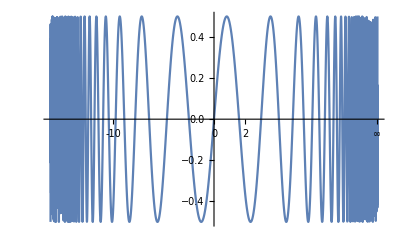

```mathematica
Plot[Cos[τ]Sin[τ],{τ,-Infinity,Infinity}]
```

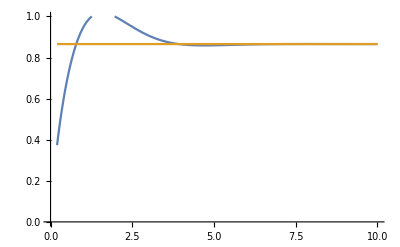

-Graphics-

```mathematica
Plot[{gamma194b[t,1/1, 0.2,1],gammaMark[1,1/1, 0.2,1]},{t,0.2,10},PlotRange->{0,1}]
Plot[{gamma194c[t,1/1, 0.2,1],gammaMark[1,1/1, 0.2,1]},{t,0.2,10},PlotRange->{0,1}]
```

```mathematica
Lamb196b[t_,β_, λ_,γ_]:=NIntegrate[2 JDLnew[ω, λ,γ]/π Coth[β ω/2]((1-Cos[t (1+ω)])/(1+ω)-(1-Cos[t (ω-1)])/(ω-1)),{ω,0,Infinity}]
Lamb196c[t_,β_, λ_,γ_]:=NIntegrate[2 JDLnew[ω, λ,γ]/π Coth[β ω/2]((1-Cos[t (ω+1)])/(ω+1)),{ω,-Infinity,Infinity}]

Lamb196b[3,1/1, 0.2,1]
Lamb196c[3,1/1, 0.2,1]
Lamb196c[973,1/1, 0.2,1]
```

0.778655

0.778655

0.747711

```mathematica
Lamb1CLE[t_,β_, λ_,γ_]:=NIntegrate[2/t JDLnew[ω, λ,γ]/π Coth[β ω/2]((Sin[t (ω-1)]-t (ω-1))/(ω-1)^2),{ω,-Infinity,Infinity}]
Lamb1CLE[989,1/1, 0.2,1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.746966

```mathematica
i1[t_?NumericQ,β_?NumericQ, λ_?NumericQ,γ_?NumericQ,Msup_?NumericQ]:=NIntegrate[4 JDLnew[ω, λ,γ]/π Coth[β ω/2]Cos[t ω],{ω,0,Msup}]
i2[β_?NumericQ, λ_?NumericQ,γ_?NumericQ,Msup_?NumericQ]:=NIntegrate[ i1[t,β, λ,γ,Msup]Sin[t],{t,0,Msup}]
Plot[i2[1/1, 0.2,1,ms],{ms,1,6}]
```

$Aborted

```mathematica
i2[1/1, 0.2,1,60]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.68657}. NIntegrate obtained 0.747782 and 1.09329×10^-6 for the integral and error estimates.

0.747782

```mathematica
Limit[Lamb196c[t,1,0.2,1],t->∞]
```

NIntegrate::inumr: The integrand (0.254648 ω (1-Cos[t (1+ω)]) Coth[ω/2])/((1+ω) (1+ω^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

lim_(t→∞) NIntegrate[(2 JDLnew[ω,0.2,1] Coth[ω/2] (1-Cos[t (ω+1)]))/(π (ω+1)),{ω,-∞,∞}]

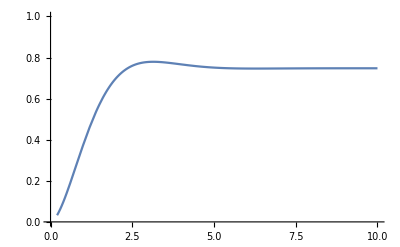

```mathematica
Plot[{Lamb196c[t,1/1, 0.2,1]},{t,0.2,10},PlotRange->{0,1}]
```

```mathematica
Lamb196c[6,1/1, 0.2,1]
Lamb196c[10,1/1, 0.2,1]
Lamb196c[900,1/1, 0.2,1]
Lamb196c[973,1/1, 0.2,1]
```

0.746475

0.747757

0.747711

0.747711

0.865581

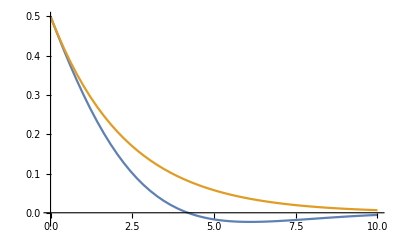

```mathematica
gammaMark[1,1/1, 0.2,1]
Plot[{0.5 Cos[Lamb196c[973,1/1, 0.2,1]t/2]Exp[-gammaMark[1,1/1, 0.2,1] t/2],0.5Exp[-gammaMark[1,1/1, 0.2,1] t/2]},{t,0,10}]
```

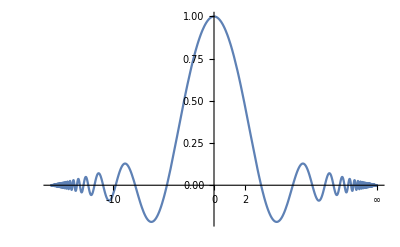

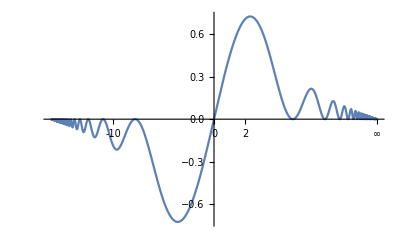

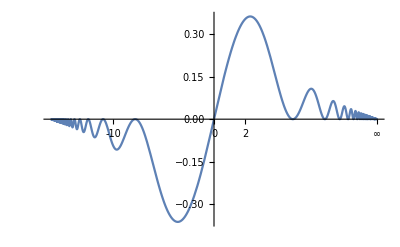

```mathematica
Plot[Sin[x]/x,{x,-Infinity,Infinity}]
Plot[(1-Cos[x])/x,{x,-Infinity,Infinity}]
Plot[(Sin[x/2])^2/x,{x,-Infinity,Infinity}]
```

```mathematica
NIntegrate[(1-Cos[x])/x,{x,-Infinity,Infinity}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.81037×10^7}. NIntegrate obtained 14.2805 and 2.20927 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (1-Cos[x])/x is being considered as zero over the specified region, but may actually be divergent.

0.

For TCL 2 we have 
dot(ρ01)=-2e^{-iΩ0 t}[α1(t)ρ01-α2(t)ρ10]
dot(ρ10)=2e^{iΩ0 t}[α1(t)ρ01-α2(t)ρ10]
α1(t)=∫_0^tdt1 ν01e^(i Ω t1)
α2(t)=∫_0^tdt1 ν01e^(-i Ω t1)

```mathematica
Integrate[Cos[u (t-t1)]Exp[I Ω t1],{t1,0,t}]
Integrate[Cos[u (t-t1)]Exp[-I Ω t1],{t1,0,t}]
```

(ⅈ ⅇ^(ⅈ t Ω) Ω-ⅈ Ω Cos[t u]+u Sin[t u])/(u^2-Ω^2)

(ⅈ ⅇ^(-ⅈ t Ω) Ω-ⅈ Ω Cos[t u]-u Sin[t u])/(-u^2+Ω^2)

```mathematica
Integrate[Cos[u (t-t1)]Exp[I Ω (-t1)],{t1,0,t}]
```

(ⅈ ⅇ^(-ⅈ t Ω) Ω-ⅈ Ω Cos[t u]-u Sin[t u])/(-u^2+Ω^2)

Now lets compare TCL 4 for the coherences

```mathematica
FullSimplify[ExpToTrig[

(ν02+I η02)(ν13+I η13)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t2]].SΩt[t3].rho]-(ν02+I η02)(ν13-I η13)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t2]].rho.SΩt[t3]]-(ν02-I η02)(ν13+I η13)Commut[SΩt[t0],SΩt[t3].rho.Commut[SΩt[t1],SΩt[t2]]]+(ν02-I η02)(ν13-I η13)Commut[SΩt[t0],rho.SΩt[t3].Commut[SΩt[t1],SΩt[t2]]]+(ν03+I η03)(ν12+I η12)(Commut[SΩt[t0],Commut[SΩt[t3],SΩt[t2]].rho.SΩt[t1]]+Commut[SΩt[t0],Commut[SΩt[t1].SΩt[t2],SΩt[t3]].rho])+(ν03-I η03)(ν12-I η12)(Commut[SΩt[t0],SΩt[t1].rho.Commut[SΩt[t3],SΩt[t2]]]+Commut[SΩt[t0],rho.Commut[SΩt[t2].SΩt[t1],SΩt[t3]]])-(ν03+I η03)(ν12-I η12)Commut[SΩt[t0],Commut[SΩt[t1],SΩt[t3]].rho.SΩt[t2]]-(ν03-I η03)(ν12+I η12)Commut[SΩt[t0],SΩt[t2].rho.Commut[SΩt[t1],SΩt[t3]]]

]]//MatrixForm
```

(4 ((ν03 ν12+ν02 ν13) (-1+2 ρ11) Cos[(t0+t1-t2-t3) Ω]+ν02 ν13 (1-2 ρ11) Cos[(t0-t1+t2-t3) Ω]+ν03 ν12 (1-2 ρ11) Cos[(t0-t1-t2+t3) Ω]-η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η12 ν03 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η13 ν02 (-Sin[(t0+t1-t2-t3) Ω]+Sin[(t0-t1+t2-t3) Ω])-η03 ν12 Sin[(t0-t1-t2+t3) Ω]) | -8 ⅈ ⅇ^(-ⅈ t0 Ω) (Cos[t2 Ω] ((η03 η12+η02 η13) (ρ01+ρ10) Cos[t3 Ω] Sin[t1 Ω]-(ν03 ν12 (ρ01+ρ10) Cos[t1 Ω]-ⅈ (η03 η12+η02 η13-ν03 ν12) (ρ01-ρ10) Sin[t1 Ω]) Sin[t3 Ω])+Sin[t2 Ω] (ⅈ ν03 ν12 (ρ01-ρ10) Cos[t3 Ω] Sin[t1 Ω]+Cos[t1 Ω] (-((η03 η12+η02 η13-ν03 ν12) (ρ01+ρ10) Cos[t3 Ω])-ⅈ (η03 η12+η02 η13) (ρ01-ρ10) Sin[t3 Ω])))
8 ⅈ ⅇ^(ⅈ t0 Ω) (Cos[t2 Ω] ((η03 η12+η02 η13) (ρ01+ρ10) Cos[t3 Ω] Sin[t1 Ω]-(ν03 ν12 (ρ01+ρ10) Cos[t1 Ω]-ⅈ (η03 η12+η02 η13-ν03 ν12) (ρ01-ρ10) Sin[t1 Ω]) Sin[t3 Ω])+Sin[t2 Ω] (ⅈ ν03 ν12 (ρ01-ρ10) Cos[t3 Ω] Sin[t1 Ω]+Cos[t1 Ω] (-((η03 η12+η02 η13-ν03 ν12) (ρ01+ρ10) Cos[t3 Ω])-ⅈ (η03 η12+η02 η13) (ρ01-ρ10) Sin[t3 Ω]))) | -4 ((ν03 ν12+ν02 ν13) (-1+2 ρ11) Cos[(t0+t1-t2-t3) Ω]+ν02 ν13 (1-2 ρ11) Cos[(t0-t1+t2-t3) Ω]+ν03 ν12 (1-2 ρ11) Cos[(t0-t1-t2+t3) Ω]-η12 ν03 Sin[(t0+t1-t2-t3) Ω]+η12 ν03 Sin[(t0-t1+t2-t3) Ω]+η03 ν12 Sin[(t0-t1+t2-t3) Ω]+η13 ν02 (-Sin[(t0+t1-t2-t3) Ω]+Sin[(t0-t1+t2-t3) Ω])-η03 ν12 Sin[(t0-t1-t2+t3) Ω]))

```mathematica
FullSimplify[-8 ⅈ ⅇ^(-ⅈ t0 Ω) (Cos[t2 Ω] ((η03 η12+η02 η13) (ρ01+ρ10) Cos[t3 Ω] Sin[t1 Ω]-(ν03 ν12 (ρ01+ρ10) Cos[t1 Ω]-ⅈ (η03 η12+η02 η13-ν03 ν12) (ρ01-ρ10) Sin[t1 Ω]) Sin[t3 Ω])+Sin[t2 Ω] (ⅈ ν03 ν12 (ρ01-ρ10) Cos[t3 Ω] Sin[t1 Ω]+Cos[t1 Ω] (-((η03 η12+η02 η13-ν03 ν12) (ρ01+ρ10) Cos[t3 Ω])-ⅈ (η03 η12+η02 η13) (ρ01-ρ10) Sin[t3 Ω])))]
```

-8 ⅈ ⅇ^(-ⅈ t0 Ω) (Cos[t2 Ω] ((η03 η12+η02 η13) (ρ01+ρ10) Cos[t3 Ω] Sin[t1 Ω]-(ν03 ν12 (ρ01+ρ10) Cos[t1 Ω]-ⅈ (η03 η12+η02 η13-ν03 ν12) (ρ01-ρ10) Sin[t1 Ω]) Sin[t3 Ω])+Sin[t2 Ω] (ⅈ ν03 ν12 (ρ01-ρ10) Cos[t3 Ω] Sin[t1 Ω]+Cos[t1 Ω] (-((η03 η12+η02 η13-ν03 ν12) (ρ01+ρ10) Cos[t3 Ω])-ⅈ (η03 η12+η02 η13) (ρ01-ρ10) Sin[t3 Ω])))

```mathematica
getridρ01[ρ01_,ρ10_]:=-8 ⅈ ⅇ^(-ⅈ t0 Ω) (Cos[t2 Ω] ((η03 η12+η02 η13) (ρ01+ρ10) Cos[t3 Ω] Sin[t1 Ω]-(ν03 ν12 (ρ01+ρ10) Cos[t1 Ω]-ⅈ (η03 η12+η02 η13-ν03 ν12) (ρ01-ρ10) Sin[t1 Ω]) Sin[t3 Ω])+Sin[t2 Ω] (ⅈ ν03 ν12 (ρ01-ρ10) Cos[t3 Ω] Sin[t1 Ω]+Cos[t1 Ω] (-((η03 η12+η02 η13-ν03 ν12) (ρ01+ρ10) Cos[t3 Ω])-ⅈ (η03 η12+η02 η13) (ρ01-ρ10) Sin[t3 Ω])))
FullSimplify[getridρ01[ρ01,0]]
FullSimplify[getridρ01[0,ρ10]]
```

4 ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (ⅇ^(2 ⅈ (t2+t3) Ω) (η03 η12+η02 η13)-ⅇ^(2 ⅈ (t1+t2) Ω) ν03 ν12-ⅇ^(2 ⅈ (t1+t3) Ω) (η03 η12+η02 η13-ν03 ν12)) ρ01

4 ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (-ⅇ^(2 ⅈ t1 Ω) (η03 η12+η02 η13)+ⅇ^(2 ⅈ t3 Ω) ν03 ν12+ⅇ^(2 ⅈ t2 Ω) (η03 η12+η02 η13-ν03 ν12)) ρ10

```mathematica
FullSimplify[Expand[ExpToTrig[4 ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (ⅇ^(2 ⅈ (t2+t3) Ω) (η03 η12+η02 η13)-ⅇ^(2 ⅈ (t1+t3) Ω) (η03 η12+η02 η13)) ρ01-(4 (ⅇ^(ⅈ (-t0+t3) Ω) (-2 ⅈ Sin[ Ω(t1-t2)])(η03 η12+η02 η13)) ρ01)]]]
```

0

```mathematica
FullSimplify[Expand[ExpToTrig[4 ⅇ^(-ⅈ (t0+t1+t2+t3) Ω) (-ⅇ^(2 ⅈ t1 Ω) (η03 η12+η02 η13)+ⅇ^(2 ⅈ t3 Ω) ν03 ν12+ⅇ^(2 ⅈ t2 Ω) (η03 η12+η02 η13-ν03 ν12)) ρ10-(4 (ⅇ^(- ⅈ (t0+t3) Ω) (-2 ⅈ Sin[Ω(t1-t2)])(η03 η12+η02 η13)+ⅇ^(-ⅈ (t0+t1) Ω) (-2 ⅈ Sin[Ω(t2-t3)])ν03 ν12) ρ10)]]]
```

0

```mathematica
FullSimplify[getridρ01[ρ01,ρ10]-(-8 ⅈ ⅇ^(-ⅈ t0 Ω)(Sin[Ω(t1-t2)](ⅇ^(ⅈ t3 Ω)ρ01+ⅇ^(-ⅈ t3 Ω)ρ10)(η03 η12+η02 η13)+Sin[Ω(t2-t3)](ⅇ^(ⅈ t1 Ω)ρ01+ⅇ^(-ⅈ t1 Ω)ρ10)ν03 ν12) )]
```

0

For TCL4 
for alpha1
∫_0^t dt1∫_0^t1 dt2  {s12[η12∫^t2 dt3 exp(iΩt3) η03+η02∫^t2 dt3 exp(iΩt3) η13 ]+ exp(iΩt1)ν12∫^t2 dt3 s23 ν03}
where ∫^t2 dt3 exp(iΩt3) η03= ∫^inf J(ω)dω ∫^t2 dt3 exp(iΩt3)(-sin(ω(t-t3))) =∫^inf J(ω)dω1/((ω-Ω) (ω+Ω))(ω Cos[t ω]+ⅈ Ω Sin[t ω]-ⅇ^(ⅈ t2 Ω) (ω Cos[(t-t2) ω]+ⅈ Ω Sin[(t-t2) ω]))
∫^t2 dt3 s23 ν03= ∫^inf J(ω)dω Cot[β ω/2]∫^t2 cos((t-t3)ω) sin(t2-t3)Ω = ∫^inf J(ω)dω(-Ω Cos[(t-t2) ω]+Ω Cos[t ω] Cos[t2 Ω]+ω Sin[t ω] Sin[t2 Ω])/(ω^2-Ω^2)

```mathematica
FullSimplify[Integrate[-Sin[ω(t-t3)]Exp[I Ω t3],{t3,0,t2}]]
FullSimplify[Integrate[-Sin[ω(t1-t3)]Exp[I Ω t3],{t3,0,t2}]]
FullSimplify[Integrate[Cos[ω(t-t3)]Sin[Ω(t2-t3)],{t3,0,t2}]]
```

(ω Cos[t ω]+ⅈ Ω Sin[t ω]-ⅇ^(ⅈ t2 Ω) (ω Cos[(t-t2) ω]+ⅈ Ω Sin[(t-t2) ω]))/((ω-Ω) (ω+Ω))

1/((ω-Ω) (ω+Ω))(ω Cos[t1 ω]+ⅈ Ω Sin[t1 ω]-ⅇ^(ⅈ t2 Ω) (ω Cos[(t1-t2) ω]+ⅈ Ω Sin[(t1-t2) ω]))

(-Ω Cos[(t-t2) ω]+Ω Cos[t ω] Cos[t2 Ω]+ω Sin[t ω] Sin[t2 Ω])/(ω^2-Ω^2)

For TCL4  alpha2
∫_0^t dt1∫_0^t1 dt2  {s12[η12∫^t2 dt3 exp(-iΩt3) η03+η02∫^t2 dt3 exp(-iΩt3) η13 ]+ exp(-iΩt1)ν12∫^t2 dt3 s23 ν03}

where ∫^t2 dt3 exp(-iΩt3) η03= ∫^inf J(ω)dω ∫^t2 dt3 exp(-iΩt3)(-sin(ω(t-t3))) =∫^inf J(ω)dω1/(-ω^2+Ω^2)(-ω Cos[t ω]+ⅈ Ω Sin[t ω]+ⅇ^(-ⅈ t2 Ω) (ω Cos[(t-t2) ω]-ⅈ Ω Sin[(t-t2) ω]))
∫^t2 dt3 s23 ν03= ∫^inf J(ω)dω Cot[β ω/2]∫^t2 cos((t-t3)ω) sin(t2-t3)Ω = ∫^inf J(ω)dω1/(ω^2-Ω^2)(-Ω Cos[(t-t2) ω]+Ω Cos[t ω] Cos[t2 Ω]+ω Sin[t ω] Sin[t2 Ω])

```mathematica
FullSimplify[Integrate[-Sin[ω(t-t3)]Exp[-I Ω t3],{t3,0,t2}]]
FullSimplify[Integrate[-Sin[ω(t1-t3)]Exp[-I Ω t3],{t3,0,t2}]]
(*FullSimplify[Integrate[Cos[ω(t-t3)]Sin[Ω(t2-t3)],{t3,0,t2}]]*)
```

1/(-ω^2+Ω^2)(-ω Cos[t ω]+ⅈ Ω Sin[t ω]+ⅇ^(-ⅈ t2 Ω) (ω Cos[(t-t2) ω]-ⅈ Ω Sin[(t-t2) ω]))

1/(-ω^2+Ω^2)(-ω Cos[t1 ω]+ⅈ Ω Sin[t1 ω]+ⅇ^(-ⅈ t2 Ω) (ω Cos[(t1-t2) ω]-ⅈ Ω Sin[(t1-t2) ω]))

```mathematica
{{4 ()}, {8 ⅈ ⅇ^(ⅈ t0 Ω) (Cos[t2 Ω] ((η03 η12+η02 η13) (ρ01+ρ10) Cos[t3 Ω] Sin[t1 Ω]-(ν03 ν12 (ρ01+ρ10) Cos[t1 Ω]-ⅈ (η03 η12+η02 η13-ν03 ν12) (ρ01-ρ10) Sin[t1 Ω]) Sin[t3 Ω])+Sin[t2 Ω] (ⅈ ν03 ν12 (ρ01-ρ10) Cos[t3 Ω] Sin[t1 Ω]+Cos[t1 Ω] (-((η03 η12+η02 η13-ν03 ν12) (ρ01+ρ10) Cos[t3 Ω])-ⅈ (η03 η12+η02 η13) (ρ01-ρ10) Sin[t3 Ω])))}}
```

Now for rho10 dot 8 ⅈ ⅇ^(ⅈ t0 Ω) (Cos[t2 Ω] ((η03 η12+η02 η13) (ρ01+ρ10) Cos[t3 Ω] Sin[t1 Ω]-(ν03 ν12 (ρ01+ρ10) Cos[t1 Ω]-ⅈ (η03 η12+η02 η13-ν03 ν12) (ρ01-ρ10) Sin[t1 Ω]) Sin[t3 Ω])+Sin[t2 Ω] (ⅈ ν03 ν12 (ρ01-ρ10) Cos[t3 Ω] Sin[t1 Ω]+Cos[t1 Ω] (-((η03 η12+η02 η13-ν03 ν12) (ρ01+ρ10) Cos[t3 Ω])-ⅈ (η03 η12+η02 η13) (ρ01-ρ10) Sin[t3 Ω])))

```mathematica
rho10dot[ρ01_,ρ10_]:=8 ⅈ ⅇ^(ⅈ t0 Ω) (Cos[t2 Ω] ((η03 η12+η02 η13) (ρ01+ρ10) Cos[t3 Ω] Sin[t1 Ω]-(ν03 ν12 (ρ01+ρ10) Cos[t1 Ω]-ⅈ (η03 η12+η02 η13-ν03 ν12) (ρ01-ρ10) Sin[t1 Ω]) Sin[t3 Ω])+Sin[t2 Ω] (ⅈ ν03 ν12 (ρ01-ρ10) Cos[t3 Ω] Sin[t1 Ω]+Cos[t1 Ω] (-((η03 η12+η02 η13-ν03 ν12) (ρ01+ρ10) Cos[t3 Ω])-ⅈ (η03 η12+η02 η13) (ρ01-ρ10) Sin[t3 Ω])))
rho10dot[ρ01,0]
rho10dot[0,ρ10]
```

8 ⅈ ⅇ^(ⅈ t0 Ω) (Cos[t2 Ω] ((η03 η12+η02 η13) ρ01 Cos[t3 Ω] Sin[t1 Ω]-(ν03 ν12 ρ01 Cos[t1 Ω]-ⅈ (η03 η12+η02 η13-ν03 ν12) ρ01 Sin[t1 Ω]) Sin[t3 Ω])+Sin[t2 Ω] (ⅈ ν03 ν12 ρ01 Cos[t3 Ω] Sin[t1 Ω]+Cos[t1 Ω] (-((η03 η12+η02 η13-ν03 ν12) ρ01 Cos[t3 Ω])-ⅈ (η03 η12+η02 η13) ρ01 Sin[t3 Ω])))

8 ⅈ ⅇ^(ⅈ t0 Ω) (Cos[t2 Ω] ((η03 η12+η02 η13) ρ10 Cos[t3 Ω] Sin[t1 Ω]-(ν03 ν12 ρ10 Cos[t1 Ω]+ⅈ (η03 η12+η02 η13-ν03 ν12) ρ10 Sin[t1 Ω]) Sin[t3 Ω])+Sin[t2 Ω] (-ⅈ ν03 ν12 ρ10 Cos[t3 Ω] Sin[t1 Ω]+Cos[t1 Ω] (-((η03 η12+η02 η13-ν03 ν12) ρ10 Cos[t3 Ω])+ⅈ (η03 η12+η02 η13) ρ10 Sin[t3 Ω])))

```mathematica
TrigToExp[rho10dot[ρ01,0]]
```

4 ⅇ^(ⅈ t0 Ω+ⅈ t1 Ω-ⅈ t2 Ω+ⅈ t3 Ω) η03 η12 ρ01-4 ⅇ^(ⅈ t0 Ω-ⅈ t1 Ω+ⅈ t2 Ω+ⅈ t3 Ω) η03 η12 ρ01+4 ⅇ^(ⅈ t0 Ω+ⅈ t1 Ω-ⅈ t2 Ω+ⅈ t3 Ω) η02 η13 ρ01-4 ⅇ^(ⅈ t0 Ω-ⅈ t1 Ω+ⅈ t2 Ω+ⅈ t3 Ω) η02 η13 ρ01+4 ⅇ^(ⅈ t0 Ω+ⅈ t1 Ω+ⅈ t2 Ω-ⅈ t3 Ω) ν03 ν12 ρ01-4 ⅇ^(ⅈ t0 Ω+ⅈ t1 Ω-ⅈ t2 Ω+ⅈ t3 Ω) ν03 ν12 ρ01

```mathematica
TrigToExp[rho10dot[0,ρ10]]
```

4 ⅇ^(ⅈ t0 Ω+ⅈ t1 Ω-ⅈ t2 Ω-ⅈ t3 Ω) η03 η12 ρ10-4 ⅇ^(ⅈ t0 Ω-ⅈ t1 Ω+ⅈ t2 Ω-ⅈ t3 Ω) η03 η12 ρ10+4 ⅇ^(ⅈ t0 Ω+ⅈ t1 Ω-ⅈ t2 Ω-ⅈ t3 Ω) η02 η13 ρ10-4 ⅇ^(ⅈ t0 Ω-ⅈ t1 Ω+ⅈ t2 Ω-ⅈ t3 Ω) η02 η13 ρ10+4 ⅇ^(ⅈ t0 Ω-ⅈ t1 Ω+ⅈ t2 Ω-ⅈ t3 Ω) ν03 ν12 ρ10-4 ⅇ^(ⅈ t0 Ω-ⅈ t1 Ω-ⅈ t2 Ω+ⅈ t3 Ω) ν03 ν12 ρ10

```mathematica
FullSimplify[Expand[ExpToTrig[rho10dot[ρ01,ρ10]-(8  ⅈ ⅇ^(ⅈ t0  Ω)( Sin[Ω(t1-t2)](η03 η12+η02 η13)(ⅇ^(ⅈ t3 Ω)ρ01+ⅇ^(- ⅈ t3 Ω)ρ10)+ Sin[Ω(t2-t3)]ν03 ν12(ⅇ^(ⅈ t1 Ω)ρ01+ⅇ^(- ⅈ t1 Ω)ρ10) ) )]]]
```

0

```mathematica
-FullSimplify[ν01 Commut[SΩt[t0],Commut[SΩt[t1],rho]]+I η01 Commut[SΩt[t0],Anticommut[SΩt[t1],rho]]]//MatrixForm
```

(-2 ν01 (1-2 ρ11) Cos[(t0-t1) Ω]-2 η01 Sin[(t0-t1) Ω] | -2 ⅇ^(-ⅈ (t0+t1) Ω) ν01 (ⅇ^(2 ⅈ t1 Ω) ρ01-ρ10)
2 ⅇ^(ⅈ (t0-t1) Ω) ν01 (ⅇ^(2 ⅈ t1 Ω) ρ01-ρ10) | -2 ν01 (-1+2 ρ11) Cos[(t0-t1) Ω]+2 η01 Sin[(t0-t1) Ω])

```mathematica
FullSimplify[-2 ⅇ^(-ⅈ (t0+t1) Ω) ν01 (ⅇ^(2 ⅈ t1 Ω) ρ01-ρ10)-(-2 ⅇ^(-ⅈ t0  Ω) ν01 (ⅇ^(ⅈ t1 Ω) ρ01-ⅇ^(-ⅈ t1 Ω) ρ10))]
FullSimplify[2 ⅇ^(ⅈ (t0-t1) Ω) ν01 (ⅇ^(2 ⅈ t1 Ω) ρ01-ρ10)-(2 ⅇ^(ⅈ t0  Ω) ν01 (ⅇ^(ⅈ t1 Ω) ρ01-ⅇ^(-ⅈ t1 Ω) ρ10))]
```

0

0

```mathematica
rho
```

{{1-ρ11,ρ01},{ρ10,ρ11}}

```mathematica
FullSimplify[({{1,1},{1,-1}}/Sqrt[2]).rho.({{1,1},{1,-1}}/Sqrt[2])]
```

{{1/2 (1+ρ01+ρ10),1/2 (1-ρ01+ρ10-2 ρ11)},{1/2 (1+ρ01-ρ10-2 ρ11),1/2 (1-ρ01-ρ10)}}

```mathematica
Clear[γp]
```

```mathematica
(-I (Sm/2)Commut[σp.σm,rho]-I (Sp/2)Commut[σm.σp,rho]+γm(σm.rho.σp-Anticommut[σp.σm,rho])+γp(σp.rho.σm-Anticommut[σm.σp,rho]))//MatrixForm
```

(γm ρ11+γp (-2+2 ρ11) | (ⅈ Sm ρ01)/2-(ⅈ Sp ρ01)/2-γm ρ01-γp ρ01
-1/2 ⅈ Sm ρ10+(ⅈ Sp ρ10)/2-γm ρ10-γp ρ10 | γp (1-ρ11)-2 γm ρ11)

## Now for the Ohmic bath spectral density

```mathematica
Johm[ω_,η_,ωc_]:=η ω Exp[-ω/ωc]
Integrate[Johm[ω,η,ωc]Sin[ω τ],{ω,0,Infinity}]
```

ConditionalExpression[(2 η τ ωc^3)/((1+τ^2 ωc^2)^2), Re[1/ωc]>Abs[Im[τ]]]

```mathematica
Integrate[Johm[ω,η,ωc]Coth[β ω/2]Cos[ω τ],{ω,0,Infinity}]
```

ConditionalExpression[η ((ωc^2 (-1+τ^2 ωc^2))/((1+τ^2 ωc^2)^2)+(PolyGamma[1,(1-ⅈ τ ωc)/(β ωc)]+PolyGamma[1,(1+ⅈ τ ωc)/(β ωc)])/β^2), Re[β]>0]

```mathematica
Integrate[Johm[ω,1,1]Coth[ω/2]Cos[ω],{ω,0,Infinity}]
Integrate[Johm[ω,1,1]Coth[β ω/2]Cos[ω],{ω,0,Infinity}]
```

1-π^2 Csch[π]^2

ConditionalExpression[(PolyGamma[1,(1-ⅈ)/β]+PolyGamma[1,(1+ⅈ)/β])/β^2, Re[β]>0]

```mathematica
Integrate[Johm[ω,η,ωc][Coth[β ω/2]Cos[ω τ]-I Sin[ω τ]],{ω,0,Infinity}]
```

∫_0^∞ (ⅇ^(-ω/ωc) η ω)[Cos[τ ω] Coth[(β ω)/2]-ⅈ Sin[τ ω]]ⅆω

```mathematica
NIntegrate[Johm[ω,1,1][Coth[ ω/2]Cos[ω]-I Sin[ω]],{ω,0.001,2}]
```

NIntegrate::inumr: The integrand (ⅇ^-ω ω)[Cos[ω] Coth[ω/2]-ⅈ Sin[ω]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.001,2}}.

NIntegrate[Johm[ω,1,1][Coth[ω/2] Cos[ω]-ⅈ Sin[ω]],{ω,0.001,2}]

```mathematica
Integrate[Integrate[Exp[I(Ω+ω)(s-s')-β ω]+Exp[I(Ω-ω)(s-s')],{s',0,s}],{s,0,t}]
```

(1-ⅇ^(-ⅈ t (ω-Ω)))/(ω-Ω)^2-(ⅈ t)/(ω-Ω)-(ⅇ^(-β ω) (-1+ⅇ^(ⅈ t (ω+Ω))))/(ω+Ω)^2+(ⅈ ⅇ^(-β ω) t)/(ω+Ω)

```mathematica
Integrate[Johm[ω,η,ωc]Coth[β ω/2](1-Cos[(ω+1) τ])/(ω+1),{ω,0,Infinity}]
```

$Aborted

```mathematica
Integrate[Johm[ω,η,ωc]Coth[β ω/2](Sinc[(ω+1) τ])^2,{ω,0,Infinity}]
```

$Aborted

```mathematica
Integrate[Johm[ω,η,ωc]Coth[β ω/2]Sin[(ω+1) τ],{ω,0,Infinity}]
```

ConditionalExpression[0, Re[β]>0]

```mathematica
Integrate[Johm[ω,η,ωc]Coth[β ω/2]Sin[(ω+1) τ]/(ω+1),{ω,0,Infinity}]
```

∫_0^∞ (ⅇ^(-ω/ωc) η ω Coth[(β ω)/2] Sin[τ (1+ω)])/(1+ω)ⅆω

```mathematica
Integrate[Johm[ω,η,ωc]Coth[β ω/2]Cos[ω τ],{ω,0,Infinity}]
```

ConditionalExpression[0, Re[β]>0]

```mathematica
Integrate[Johm[ω,η,ωc]Coth[β ω/2]Sin[ω τ],{ω,0,Infinity}]
```

ConditionalExpression[0, Re[β]>0]

```mathematica
Johm[ω,η,ωc]
```

ⅇ^(-ω/ωc) η ω

```mathematica
Integrate[ⅇ^(-ω/ωc) η ωCoth[β ω/2]Sin[ω τ],{ω,0,Infinity}]
```

ConditionalExpression[0, Re[β]>0]

```mathematica
Johm[ω_,η_,ωc_]:=η ω Exp[-ω/ωc]
Integrate[Johm[ω,η,ωc]Sin[ω τ],{ω,0,Infinity}]
Integrate[Johm[ω,η,ωc]Coth[β ω/2]Cos[ω τ],{ω,0,Infinity}]
```

ConditionalExpression[(2 η τ ωc^3)/((1+τ^2 ωc^2)^2), Re[1/ωc]>Abs[Im[τ]]]

$Aborted

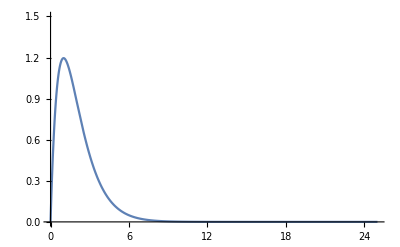

```mathematica
Plot[Johm[ω,3.25,1],{ω,0,25},PlotRange->{0,1.5}]
```

```mathematica
GammaMinusNoabsOhmTCL2[t_,β_,η_,ωc_]:= 2 NIntegrate[1/π (η ω Exp[-ω/ωc])/(1-Exp[-β ω])(Sin[(1-ω)t]/(1-ω)+Exp[-β ω] Sin[(1+ω)t]/(1+ω)),{ω,0,Infinity}]
GammaMinusAbsOhmTCL2[t_,β_,η_,ωc_]:= 2NIntegrate[1/π (η Abs[ω] Exp[-Abs[ω]/ωc])/(1-Exp[-β ω])(Sin[(1-ω)t]/(1-ω)),{ω,-Infinity,Infinity}]
GammaMinusNoabsOhmTCL2[1,1/0.5,3.25,1]
GammaMinusAbsOhmTCL2[1,1/0.5,3.25,1]
```

2.27968

NIntegrate::deorel: The relative error 1.16808 is larger than expected for the integrand -(58261326 ⅇ^ω ω Cos[ω] Sin[1])/(56317955 (-1+ⅇ^(2 ω)) (-1+ω)) over {0,∞} with DoubleExponentialOscillatory method and tuning parameters, TuningParameters -> {10,5}.

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand -(58261326 ⅇ^ω ω Cos[ω] Sin[1])/(56317955 (-1+ⅇ^(2 ω)) (-1+ω)) over {0,∞}. DoubleExponentialOscillatory obtained 16.1807 and 11.6808 for the integral and error estimates.

1.62305

```mathematica
1/2
```

1/2

```mathematica
Johm[ω_,η_,ωc_]:=η ω Exp[-ω/ωc]
Integrate[Johm[ω,η,ωc]Sin[ω τ],{ω,0,Infinity}]
```

ConditionalExpression[(2 η τ ωc^3)/((1+τ^2 ωc^2)^2), Re[1/ωc]>Abs[Im[τ]]]

```mathematica
N[1/(Exp[1/0.5]+1)]
```

0.119203

```mathematica
N[1/(Exp[1]-1)]
```

0.581977

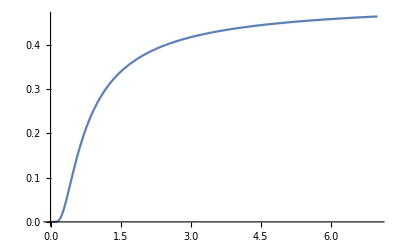

```mathematica
Plot[1/(Exp[1/x]+1),{x,0,7}]
```

```mathematica
Commut[A_,B_]:=A.B-B.A
Anticommut[A_,B_]:=A.B+B.A
rho={{ρ00,ρ01},{ρ10,ρ11}}
c
```

{{ρ00,ρ01},{ρ10,ρ11}}

{{0,0},{0,ρ00}}

{{0,0},{0,1}}

{{1,0},{0,0}}

{{1,0},{0,0}}

```mathematica
Lindb[A_,ρ_]:=A.ρ.ConjugateTranspose[A]-Anticommut[ConjugateTranspose[A].A,rho]/2
```

```mathematica
Lindb[c00,rho]
```

{{0,-ρ01/2},{-ρ10/2,0}}

```mathematica
c00.rho.c00-Anticommut[c00,rho]/2
```

{{0,-ρ01/2},{-ρ10/2,0}}

```mathematica
c00.rho.c00-Anticommut[c00,rho]/2
```

```mathematica
Lindb[σm,rho]
```

{{ρ11,-ρ01/2},{-ρ10/2,-ρ11}}

```mathematica
Lindb[σm,rho]+Lindb[c00,rho]
```

{{ρ11,-ρ01},{-ρ10,-ρ11}}

```mathematica
σm
```

{{0,1},{0,0}}

```mathematica
(c00.rho.c00+σm.rho.σp-rho)-(Lindb[σm,rho]+Lindb[c00,rho])
```

{{0,0},{0,0}}

```mathematica
Lindb[PauliMatrix[3],rho]
Lindb[c00,rho]
```

{{0,-2 ρ01},{-2 ρ10,0}}

{{0,-ρ01/2},{-ρ10/2,0}}

```mathematica
(c00.rho.c00+σm.rho.σp-rho)-(Lindb[σm,rho]+Lindb[PauliMatrix[3]/2,rho])
```

{{0,0},{0,0}}

```mathematica
(Lindb[σm,rho]+Lindb[PauliMatrix[3],rho])
```

{{ρ11,-(5 ρ01)/2},{-(5 ρ10)/2,-ρ11}}

```mathematica
St[plus_,minus_]:={{0,minus},{plus, 0}}
St[Exp[I c t],Exp[-I d t]]//MatrixForm
Clear[SΩt,rho,ρ11,ρ01,ρ10,t0]
SΩt[t_]:=St[Exp[I Ω t],Exp[-I Ω t]]
rho={{1-ρ11,ρ01},{ρ10,ρ11}};
SΩt[t0]//MatrixForm
```

(0 | ⅇ^(-ⅈ d t)
ⅇ^(ⅈ c t) | 0)

(0 | ⅇ^(-ⅈ t0 Ω)
ⅇ^(ⅈ t0 Ω) | 0)

```mathematica
FullSimplify[Commut[SΩt[t],rho.SΩt[t-τ]]]
FullSimplify[Commut[SΩt[t],SΩt[t-τ].rho]]
```

{{(-1+2 ρ11) Cos[τ Ω]-ⅈ Sin[τ Ω],ⅇ^(-ⅈ (2 t-τ) Ω) (-ⅇ^(2 ⅈ (t-τ) Ω) ρ01+ρ10)},{ⅇ^(ⅈ τ Ω) (ⅇ^(2 ⅈ (t-τ) Ω) ρ01-ρ10),(1-2 ρ11) Cos[τ Ω]+ⅈ Sin[τ Ω]}}

{{(1-2 ρ11) Cos[τ Ω]-ⅈ Sin[τ Ω],ⅇ^(-ⅈ (2 t-τ) Ω) (ⅇ^(2 ⅈ (t-τ) Ω) ρ01-ρ10)},{ⅇ^(ⅈ τ Ω) (-ⅇ^(2 ⅈ (t-τ) Ω) ρ01+ρ10),(-1+2 ρ11) Cos[τ Ω]+ⅈ Sin[τ Ω]}}

```mathematica
FullSimplify[Commut[SΩt[t],rho.SΩt[t-τ]]Bτ-Commut[SΩt[t],SΩt[t-τ].rho]Bmτ]//MatrixForm
```

(ⅇ^(-ⅈ τ Ω) (-Bmτ+Bmτ ρ11+Bτ ρ11+ⅇ^(2 ⅈ τ Ω) (Bτ (-1+ρ11)+Bmτ ρ11)) | -((Bmτ+Bτ) ⅇ^(-ⅈ (2 t-τ) Ω) (ⅇ^(2 ⅈ (t-τ) Ω) ρ01-ρ10))
(Bmτ+Bτ) ⅇ^(ⅈ τ Ω) (ⅇ^(2 ⅈ (t-τ) Ω) ρ01-ρ10) | ⅇ^(-ⅈ τ Ω) (Bmτ-Bmτ ρ11-Bτ ρ11+ⅇ^(2 ⅈ τ Ω) (Bτ-(Bmτ+Bτ) ρ11)))

```mathematica
FullSimplify[ ⅇ^(-ⅈ τ Ω) (Bmτ-Bmτ ρ11-Bτ ρ11+ⅇ^(2 ⅈ τ Ω) (Bτ-(Bmτ+Bτ) ρ11))]
```

ⅇ^(-ⅈ τ Ω) (Bmτ-Bmτ ρ11-Bτ ρ11+ⅇ^(2 ⅈ τ Ω) (Bτ-(Bmτ+Bτ) ρ11))

```mathematica
NewSΩt[t_]:=SΩt[t]+IdentityMatrix[2]/2
FullSimplify[Commut[NewSΩt[t],rho.NewSΩt[t-τ]]]
FullSimplify[Commut[NewSΩt[t],NewSΩt[t-τ].rho]]
```

{{1/2 ((-ρ01+ρ10) Cos[t Ω]+(-2+4 ρ11) Cos[τ Ω]-ⅈ ((ρ01+ρ10) Sin[t Ω]+2 Sin[τ Ω])),1/2 ⅇ^(-ⅈ (2 t-τ) Ω) (-2 ⅇ^(2 ⅈ (t-τ) Ω) ρ01+2 ρ10+ⅇ^(ⅈ (t-τ) Ω) (-1+2 ρ11))},{1/2 ⅇ^(ⅈ t Ω) (1+2 ⅇ^(ⅈ (t-τ) Ω) ρ01-2 ⅇ^(-ⅈ (t-τ) Ω) ρ10-2 ρ11),1/2 ((ρ01-ρ10) Cos[t Ω]+(2-4 ρ11) Cos[τ Ω]+ⅈ ((ρ01+ρ10) Sin[t Ω]+2 Sin[τ Ω]))}}

{{1/2 ((-ρ01+ρ10) Cos[t Ω]+(2-4 ρ11) Cos[τ Ω]-ⅈ ((ρ01+ρ10) Sin[t Ω]+2 Sin[τ Ω])),1/2 ⅇ^(-ⅈ (2 t-τ) Ω) (2 ⅇ^(2 ⅈ (t-τ) Ω) ρ01-2 ρ10+ⅇ^(ⅈ (t-τ) Ω) (-1+2 ρ11))},{1/2 ⅇ^(ⅈ t Ω) (1-2 ⅇ^(ⅈ (t-τ) Ω) ρ01+2 ⅇ^(-ⅈ (t-τ) Ω) ρ10-2 ρ11),1/2 ((ρ01-ρ10) Cos[t Ω]+(-2+4 ρ11) Cos[τ Ω]+ⅈ ((ρ01+ρ10) Sin[t Ω]+2 Sin[τ Ω]))}}

```mathematica
FullSimplify[Commut[NewSΩt[t],rho.NewSΩt[t-τ]]Bτ-Commut[NewSΩt[t],NewSΩt[t-τ].rho]Bmτ]//MatrixForm
```

(1/2 ((Bmτ-Bτ) (ρ01-ρ10) Cos[t Ω]+2 (Bmτ+Bτ) (-1+2 ρ11) Cos[τ Ω]+ⅈ (Bmτ-Bτ) ((ρ01+ρ10) Sin[t Ω]+2 Sin[τ Ω])) | 1/2 ⅇ^(-ⅈ (2 t-τ) Ω) (-2 (Bmτ+Bτ) ⅇ^(2 ⅈ (t-τ) Ω) ρ01+2 (Bmτ+Bτ) ρ10-(Bmτ-Bτ) ⅇ^(ⅈ (t-τ) Ω) (-1+2 ρ11))
1/2 ⅇ^(ⅈ τ Ω) (2 (Bmτ+Bτ) ⅇ^(2 ⅈ (t-τ) Ω) ρ01-2 (Bmτ+Bτ) ρ10+(Bmτ-Bτ) ⅇ^(ⅈ (t-τ) Ω) (-1+2 ρ11)) | 1/2 (Bmτ-Bτ) (-ⅇ^(ⅈ t Ω) ρ01+ⅇ^(-ⅈ t Ω) ρ10)-(Bmτ+Bτ) (-1+2 ρ11) Cos[τ Ω]-ⅈ (Bmτ-Bτ) Sin[τ Ω])

```mathematica
FullSimplify[1/2 ((Bmτ-Bτ) (ρ01-ρ10) Cos[t Ω]+2 (Bmτ+Bτ) (-1+2 ρ11) Cos[τ Ω]+ⅈ (Bmτ-Bτ) ((ρ01+ρ10) Sin[t Ω]+2 Sin[τ Ω]))]
FullSimplify[1/2 (Bmτ-Bτ) (-ⅇ^(ⅈ t Ω) ρ01+ⅇ^(-ⅈ t Ω) ρ10)-(Bmτ+Bτ) (-1+2 ρ11) Cos[τ Ω]-ⅈ (Bmτ-Bτ) Sin[τ Ω]]
```

1/2 ((Bmτ-Bτ) (ρ01-ρ10) Cos[t Ω]+2 (Bmτ+Bτ) (-1+2 ρ11) Cos[τ Ω]+ⅈ (Bmτ-Bτ) ((ρ01+ρ10) Sin[t Ω]+2 Sin[τ Ω]))

1/2 (Bmτ-Bτ) (-ⅇ^(ⅈ t Ω) ρ01+ⅇ^(-ⅈ t Ω) ρ10)-(Bmτ+Bτ) (-1+2 ρ11) Cos[τ Ω]-ⅈ (Bmτ-Bτ) Sin[τ Ω]

```mathematica
Lindb[σm,rho]
FullSimplify[Lindb[σm,rho]+Lindb[c00,rho]]
(c00.rho.c00+σm.rho.σp-rho)
```

{{ρ11,-ρ01/2},{-ρ10/2,-ρ11}}

{{ρ11,-ρ01},{-ρ10,-ρ11}}

{{ρ11,-ρ01},{-ρ10,-ρ11}}

```mathematica
FullSimplify[Lindb[PauliMatrix[1],rho]]
```

{{-1+2 ρ11,-ρ01+ρ10},{ρ01-ρ10,1-2 ρ11}}

```mathematica
New2SΩt[t_]:=SΩt[t]+PauliMatrix[3]/2
FullSimplify[Commut[NewSΩt[t],rho.New2SΩt[t-τ]]Bτ-Commut[New2SΩt[t],New2SΩt[t-τ].rho]Bmτ]//MatrixForm
```

(1/2 (Bmτ+Bτ) ((ρ01+ρ10) Cos[t Ω]+(-2+4 ρ11) Cos[τ Ω]+ⅈ (ρ01-ρ10) Sin[t Ω])+ⅈ (Bmτ-Bτ) Sin[τ Ω] | 1/2 (-Bmτ ρ01+ⅇ^(-ⅈ (2 t-τ) Ω) ((Bmτ-Bτ) ⅇ^(ⅈ (t-τ) Ω)-2 (Bmτ+Bτ) ⅇ^(2 ⅈ (t-τ) Ω) ρ01+2 (Bmτ+Bτ) ρ10-2 Bmτ ⅇ^(ⅈ t Ω) ρ11))
1/2 ⅇ^(-ⅈ τ Ω) (Bτ (ⅇ^(ⅈ (t+τ) Ω)+2 ⅇ^(2 ⅈ t Ω) ρ01-2 ⅇ^(2 ⅈ τ Ω) ρ10)-Bmτ (ⅇ^(ⅈ (t+τ) Ω)-2 ⅇ^(2 ⅈ t Ω) ρ01+ⅇ^(ⅈ τ Ω) ρ10+2 ⅇ^(2 ⅈ τ Ω) ρ10+2 ⅇ^(ⅈ t Ω) (-1+ρ11))) | -1/2 (Bmτ+Bτ) ((ρ01+ρ10) Cos[t Ω]+(-2+4 ρ11) Cos[τ Ω]+ⅈ (ρ01-ρ10) Sin[t Ω])-ⅈ (Bmτ-Bτ) Sin[τ Ω])

```mathematica
FullSimplify[-1/2 (Bmτ+Bτ) ((ρ01+ρ10) Cos[t Ω]+(-2+4 ρ11) Cos[τ Ω]+ⅈ (ρ01-ρ10) Sin[t Ω])-ⅈ (Bmτ-Bτ) Sin[τ Ω]]
```

-1/2 (Bmτ+Bτ) ((ρ01+ρ10) Cos[t Ω]+(-2+4 ρ11) Cos[τ Ω]+ⅈ (ρ01-ρ10) Sin[t Ω])-ⅈ (Bmτ-Bτ) Sin[τ Ω]

```mathematica
New2SΩt[t_]:=SΩt[t]+c00;FullSimplify[Commut[NewSΩt[t],rho.New2SΩt[t-τ]]Bτ-Commut[New2SΩt[t],New2SΩt[t-τ].rho]Bmτ]//MatrixForm
```

((Bmτ ρ01+Bτ ρ10) Cos[t Ω]+(Bmτ+Bτ) (-1+2 ρ11) Cos[τ Ω]+ⅈ ((Bmτ ρ01-Bτ ρ10) Sin[t Ω]+(Bmτ-Bτ) Sin[τ Ω]) | ⅇ^(-ⅈ (2 t-τ) Ω) (Bτ (-ⅇ^(2 ⅈ (t-τ) Ω) ρ01+ρ10+ⅇ^(ⅈ (t-τ) Ω) (-1+ρ11))-Bmτ (ⅇ^(2 ⅈ (t-τ) Ω) ρ01+ⅇ^(ⅈ (2 t-τ) Ω) ρ01-ρ10+ⅇ^(ⅈ (t-τ) Ω) (-1+ρ11)+ⅇ^(ⅈ t Ω) ρ11))
ⅇ^(-ⅈ τ Ω) (Bmτ ⅇ^(ⅈ t Ω)+Bmτ ⅇ^(2 ⅈ t Ω) ρ01+Bτ ⅇ^(2 ⅈ t Ω) ρ01-Bmτ ⅇ^(2 ⅈ τ Ω) ρ10-Bτ ⅇ^(2 ⅈ τ Ω) ρ10+(Bmτ-Bτ) ⅇ^(ⅈ (t+τ) Ω) (-1+ρ11)-Bmτ ⅇ^(ⅈ t Ω) ρ11) | -((Bmτ ρ01+Bτ ρ10) Cos[t Ω])-(Bmτ+Bτ) (-1+2 ρ11) Cos[τ Ω]-ⅈ ((Bmτ ρ01-Bτ ρ10) Sin[t Ω]+(Bmτ-Bτ) Sin[τ Ω]))

```mathematica
γ1*Lindb[σm,rho]+γ2*Lindb[σp,rho]
```

{{γ1 ρ11+1/2 γ2 (-2+2 ρ11),-(γ1 ρ01)/2-(γ2 ρ01)/2},{-(γ1 ρ10)/2-(γ2 ρ10)/2,γ2 (1-ρ11)-γ1 ρ11}}

```mathematica
FullSimplify[γ1*Lindb[σm,rho]+γ2*Lindb[σp,rho]+γ3*Lindb[σm,rho]+γ4*Lindb[σp,rho]]
```

{{-γ2-γ4+(γ1+γ2+γ3+γ4) ρ11,-1/2 (γ1+γ2+γ3+γ4) ρ01},{-1/2 (γ1+γ2+γ3+γ4) ρ10,γ2+γ4-(γ1+γ2+γ3+γ4) ρ11}}

```mathematica
FullSimplify[(1/2){{1,1},{1,-1}}.rho.{{1,1},{1,-1}}]
```

{{1/2 (1+ρ01+ρ10),1/2 (1-ρ01+ρ10-2 ρ11)},{1/2 (1+ρ01-ρ10-2 ρ11),1/2 (1-ρ01-ρ10)}}

```mathematica
N[1/(Exp[1]+1)]
```

0.268941

```mathematica
FullSimplify[2Lindb[A,B]]
```

2 A.B.ConjugateTranspose[A]-ConjugateTranspose[A].A.{{1-ρ11,ρ01},{ρ10,ρ11}}-{{1-ρ11,ρ01},{ρ10,ρ11}}.ConjugateTranspose[A].A

```mathematica
LinQOptical[A_]:=γ1(2σm.A.σp-σp.σm.A-A.σp.σm)+γ2(2σp.A.σm-σm.σp.A-A.σm.σp)
LinQOptical[IdentityMatrix[2]]
LinQOptical[PauliMatrix[1]]
LinQOptical[PauliMatrix[2]]
LinQOptical[PauliMatrix[3]]
```

{{2 γ1-2 γ2,0},{0,-2 γ1+2 γ2}}

{{0,-γ1-γ2},{-γ1-γ2,0}}

{{0,ⅈ γ1+ⅈ γ2},{-ⅈ γ1-ⅈ γ2,0}}

{{-2 γ1-2 γ2,0},{0,2 γ1+2 γ2}}

```mathematica
LinQOptical[{{1,0},{0,0}}]
LinQOptical[{{0,1},{0,0}}]
LinQOptical[{{0,0},{1,0}}]
LinQOptical[{{0,0},{0,1}}]
```

{{-2 γ2,0},{0,2 γ2}}

{{0,-γ1-γ2},{0,0}}

{{0,0},{-γ1-γ2,0}}

{{2 γ1,0},{0,-2 γ1}}

```mathematica
FullSimplify[{{-2β,0,0,2α},{0,-(α+β),0,0},{0,0,-(α+β),0},{2β,0,0,-2α}}]
```

{{-2 β,0,0,2 α},{0,-α-β,0,0},{0,0,-α-β,0},{2 β,0,0,-2 α}}

```mathematica
Eigenvalues[{{-2β,0,0,2α},{0,-(α+β),0,0},{0,0,-(α+β),0},{2β,0,0,-2α}}]
```

{0,-α-β,-α-β,-2 (α+β)}

```mathematica
Eigenvectors[{{-2β,0,0,2α},{0,-(α+β),0,0},{0,0,-(α+β),0},{2β,0,0,-2α}}]
```

{{α/β,0,0,1},{0,0,1,0},{0,1,0,0},{-1,0,0,1}}

```mathematica
LinQOptical[A_]:=-I Sm/2 Commut[σp.σm,A]-I Sp/2 Commut[σm.σp,A]+ γm(2 σm.A.σp-σp.σm.A-A.σp.σm)/2+γp(2σp.A.σm-σm.σp.A-A.σm.σp)/2
LinQOptical[{{1,0},{0,0}}]
LinQOptical[{{0,1},{0,0}}]
LinQOptical[{{0,0},{1,0}}]
LinQOptical[{{0,0},{0,1}}]
```

{{-γp,0},{0,γp}}

{{0,(ⅈ Sm)/2-(ⅈ Sp)/2-γm/2-γp/2},{0,0}}

{{0,0},{-(ⅈ Sm)/2+(ⅈ Sp)/2-γm/2-γp/2,0}}

{{γm,0},{0,-γm}}

```mathematica
Eigenvalues[{{-γp,0,0,γm},{0,1/2(I S -γ),0,0},{0,0,1/2(-I S -γ),0},{γp,0,0,-γm}}]
Eigenvectors[{{-γp,0,0,γm},{0,1/2(I S -γ),0,0},{0,0,1/2(-I S -γ),0},{γp,0,0,-γm}}]
```

{0,-1/2 ⅈ (S-ⅈ γ),1/2 ⅈ (S+ⅈ γ),-γm-γp}

{{γm/γp,0,0,1},{0,0,1,0},{0,1,0,0},{-1,0,0,1}}

```mathematica
Eigenvalues[ConjugateTranspose[{{-γp,0,0,γm},{0,1/2(I S -γ),0,0},{0,0,1/2(-I S -γ),0},{γp,0,0,-γm}}]]
Eigenvectors[ConjugateTranspose[{{-γp,0,0,γm},{0,1/2(I S -γ),0,0},{0,0,1/2(-I S -γ),0},{γp,0,0,-γm}}]]
```

{0,-1/2 ⅈ (Conjugate[S]-ⅈ Conjugate[γ]),1/2 ⅈ (Conjugate[S]+ⅈ Conjugate[γ]),-Conjugate[γm]-Conjugate[γp]}

{{1,0,0,1},{0,1,0,0},{0,0,1,0},{-Conjugate[γp]/Conjugate[γm],0,0,1}}

```mathematica
InverseLaplaceTransform[(s+a)/(s^2+c s+b),s,t]
```

1/(2 √(-4 b+c^2))(-2 a ⅇ^((-c/2-1/2 √(-4 b+c^2)) t)+c ⅇ^((-c/2-1/2 √(-4 b+c^2)) t)+√(-4 b+c^2) ⅇ^((-c/2-1/2 √(-4 b+c^2)) t)+2 a ⅇ^((-c/2+1/2 √(-4 b+c^2)) t)-c ⅇ^((-c/2+1/2 √(-4 b+c^2)) t)+√(-4 b+c^2) ⅇ^((-c/2+1/2 √(-4 b+c^2)) t))

```mathematica
FullSimplify[InverseLaplaceTransform[1/(s+2a 1/(s+b+a)),s,t]]
```

ⅇ^(-1/2 (a+b) t) (Cosh[1/2 √(-8 a+(a+b)^2) t]+((a+b) Sinh[1/2 √(-8 a+(a+b)^2) t])/(√(-8 a+(a+b)^2)))

```mathematica
FullSimplify[InverseLaplaceTransform[(s+a-1/2(I S-γ))/(s^2+s(a-1/2(I S-γ))-1/2(I S-γ)A),s,t]]
```

ⅇ^(-1/4 t (2 a-ⅈ S+γ)) (Cosh[1/4 t √(8 ⅈ A S-8 A γ+(2 a-ⅈ S+γ)^2)]+((2 a-ⅈ S+γ) Sinh[1/4 t √(8 ⅈ A S-8 A γ+(2 a-ⅈ S+γ)^2)])/(√(8 ⅈ A S-8 A γ+(2 a-ⅈ S+γ)^2)))

```mathematica
FullSimplify[InverseLaplaceTransform[(s+a-1/2(I S-γ))/(s^2+s(a-1/2(I S-γ))-1/2(I S-γ)A),s,t]]
```

ⅇ^(-1/4 t (2 a-ⅈ S+γ)) (Cosh[1/4 t √(8 ⅈ A S-8 A γ+(2 a-ⅈ S+γ)^2)]+((2 a-ⅈ S+γ) Sinh[1/4 t √(8 ⅈ A S-8 A γ+(2 a-ⅈ S+γ)^2)])/(√(8 ⅈ A S-8 A γ+(2 a-ⅈ S+γ)^2)))

```mathematica
FullSimplify[InverseLaplaceTransform[(s+a-1/2(I S-γ))/(s^2+s(a-1/2(I S-γ))-1/2(I S-γ)a),s,t]]
```

(ⅇ^(-a t) (2 a ⅇ^(1/2 t (2 a+ⅈ S-γ))+ⅈ S-γ))/(2 a+ⅈ S-γ)

```mathematica
FullSimplify[InverseLaplaceTransform[1/(s+γ a/(s+a+γ)),s,t]]
FullSimplify[InverseLaplaceTransform[1/(s+γ A/(s+a+γ)),s,t]]
```

(a ⅇ^(-t γ)-ⅇ^(-a t) γ)/(a-γ)

ⅇ^(-1/2 t (a+γ)) (Cosh[1/2 t √(-4 A γ+(a+γ)^2)]+((a+γ) Sinh[1/2 t √(-4 A γ+(a+γ)^2)])/(√(-4 A γ+(a+γ)^2)))